## Helper functions

```mathematica
(*The expectation calculations for beta distributions with non-whole number parameters is slow. This allows for caching*)
ClearAll[BaCalc, BbCalc];
BaCalc[alpha_, beta_]:=BaCalc[alpha, beta]=NExpectation[ x \[Conditioned] x>=1/2, x \[Distributed]BetaDistribution[alpha,beta]];
BbCalc[alpha_, beta_]:=BbCalc[alpha, beta]=1-NExpectation[ x \[Conditioned] x<=1/2, x \[Distributed]BetaDistribution[alpha,beta]];
bwFunc = Blend[{RGBColor["#FFFFFF"], RGBColor["#969696"], RGBColor["#000000"]}, #] &; 
colorFunc = Blend[{RGBColor["#67001F"],RGBColor["#FFFFFF"],RGBColor["#1A1A1A"]}, #] &;
```

## Insensitive Norm

### Functions

```mathematica
AlphaLowerBoundary[alpha_, beta_, chat_] := Module[{wa}, 
wa = alpha/(alpha + beta);
Max[{0, wa-chat +(wa*chat)}]
];
AlphaUpperBoundary[alpha_, beta_, chat_] :=Module[{wa}, 
wa = alpha/(alpha+beta);
Min[{1, wa(1+chat)}]
];
AlphaAreaFailure[alpha_, beta_, chat_] := Module[{total, x},
total = 0;
total = total +CDF[BetaDistribution[alpha, beta],AlphaLowerBoundary[alpha, beta, chat]];
 total = total + 1 - CDF[BetaDistribution[alpha, beta], AlphaUpperBoundary[alpha, beta, chat]];
total
];
AlphaAdamsPayoff[alpha_, beta_, chat_, ca_] := Module[{wa},
wa = alpha/(alpha+beta);
Switch[ca, _?NumericQ, Which[
ca < AlphaLowerBoundary[alpha, beta, chat], ca,
ca < AlphaUpperBoundary[alpha, beta, chat], wa*(1+chat),
ca <= 1, ca
 ], 
_,0]
]
AlphaBabbishPayoff[alpha_, beta_, chat_, ca_] := Module[{wa,x},
wa =  alpha / (alpha + beta);
Switch[ca, _?NumericQ, Which[
ca < AlphaLowerBoundary[alpha, beta, chat], (1-ca),
ca < AlphaUpperBoundary[alpha, beta, chat], (1-wa)(1+chat),
ca <= 1,(1-ca)
 ], 
_,0]
]

AlphaAdamsExAnte[alpha_, beta_, chat_] :=Module[{wa},
wa = alpha/(alpha + beta);
∫_0^AlphaLowerBoundary[alpha, beta, chat] x*PDF[BetaDistribution[alpha, beta], x]ⅆx +
∫_AlphaLowerBoundary[alpha,beta,chat]^AlphaUpperBoundary[alpha, beta, chat] wa(1+chat)*PDF[BetaDistribution[alpha, beta], x]ⅆx +
∫_AlphaUpperBoundary[alpha, beta,chat]^1 x*PDF[BetaDistribution[alpha, beta], x]ⅆx 
];
AlphaBabbishExAnte[alpha_, beta_, chat_] := Module[{wa},
wa = alpha/(alpha + beta);
∫_0^AlphaLowerBoundary[alpha, beta, chat] (1-x)*PDF[BetaDistribution[alpha, beta], x]ⅆx +
∫_AlphaLowerBoundary[alpha,beta,chat]^AlphaUpperBoundary[alpha, beta, chat] (1-wa)(1+chat)*PDF[BetaDistribution[alpha, beta], x]ⅆx +
∫_AlphaUpperBoundary[alpha, beta,chat]^1 (1-x)*PDF[BetaDistribution[alpha, beta], x]ⅆx 
];
NumAlphaAdamsExAnte[alpha_, beta_, chat_] :=Module[{wa},
wa = alpha/(alpha + beta);
NIntegrate[x*PDF[BetaDistribution[alpha, beta], x], {x, 0, AlphaLowerBoundary[alpha, beta, chat]}] +
NIntegrate[wa(1+chat)*PDF[BetaDistribution[alpha, beta], x], {x,AlphaLowerBoundary[alpha,beta,chat],AlphaUpperBoundary[alpha, beta, chat]}] +
NIntegrate[x*PDF[BetaDistribution[alpha, beta], x], {x, AlphaUpperBoundary[alpha, beta,chat], 1}] 
];
NumAlphaBabbishExAnte[alpha_, beta_, chat_] := Module[{wa},
wa = alpha/(alpha + beta);
NIntegrate[(1-x)*PDF[BetaDistribution[alpha, beta], x], {x, 0, AlphaLowerBoundary[alpha, beta, chat]}] +
NIntegrate[(1-wa)(1+chat)*PDF[BetaDistribution[alpha, beta], x], {x,AlphaLowerBoundary[alpha,beta,chat],AlphaUpperBoundary[alpha, beta, chat]}] +
NIntegrate[(1-x)*PDF[BetaDistribution[alpha, beta], x], {x, AlphaUpperBoundary[alpha, beta,chat], 1}]
];
```

### Plots

```mathematica
Manipulate[
Module[ {pdf, plotlist},
pdf = PDF[BetaDistribution[alpha, beta], x];
plotlist = {Plot[pdf, {x, 0, 1},PlotRange->{{0,1}, {0, Automatic}}]};
If[AlphaLowerBoundary[alpha, beta, chat] != 0,
plotlist = Append[plotlist, Plot[pdf, {x, 0,AlphaLowerBoundary[alpha, beta, chat]}, Filling -> Axis,FillingStyle->LightRed, PlotRange->{{0,1}, {0, Automatic}}]];
];
 If[AlphaUpperBoundary[alpha, beta, chat] !=1,plotlist = Append[plotlist, Plot[pdf, {x, AlphaUpperBoundary[alpha, beta, chat],1}, Filling -> Axis, PlotRange->{{0,1}, {0, Automatic}}]];
];

Show[plotlist]
]
,{alpha, 1, 10}, {beta, 1, 10}, {chat, 0, 1}]
```

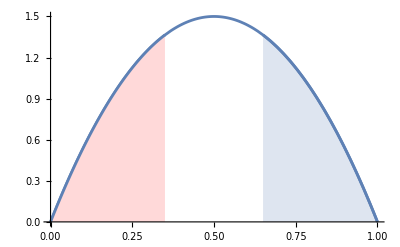

```mathematica
chat = 0.3;
pdf = PDF[BetaDistribution[2, 2], x];
plotlist = {Plot[pdf, {x, 0, 1},PlotRange->{{0,1}, {0, Automatic}}, AxesLabel->{"", ""}]};
plotlist = Append[plotlist, Plot[pdf, {x, 0, AlphaLowerBoundary[2, 2, chat]}, Filling -> Axis,FillingStyle->LightRed, PlotRange->{{0,1}, {0, Automatic}}]];
plotlist = Append[plotlist, Plot[pdf, {x, AlphaUpperBoundary[2,2,chat],1}, Filling -> Axis, PlotRange->{{0,1}, {0, Automatic}}]];

Show[plotlist]
```

```mathematica
(* A quick note on plots.  In all of the math, we have a parameter ca which represents the propotion of the final project that is due to Adams.  For radability, in the paper we are plotting against db=(1-ca) - ca, which is the difference in collaboration between Babbage and Adams. *)
```

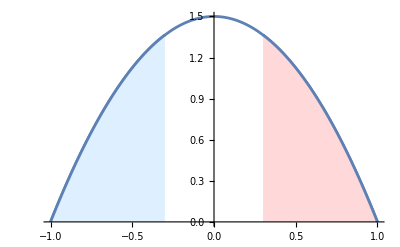

```mathematica
chat = 0.3;
pdf[x_] :=PDF[BetaDistribution[2, 2], (1-x)/2]
plotlist = {Plot[pdf[x], {x, -1, 1},PlotRange->{{-1,1}, {0, Automatic}}, AxesLabel->{"", ""}]};
plotlist = Append[plotlist, Plot[pdf[x], {x, -1, 1-2*AlphaUpperBoundary[2,2,chat]}, Filling -> Axis,FillingStyle->LightBlue, PlotRange->{{-1,1}, {0, Automatic}}]];
plotlist = Append[plotlist, Plot[pdf[x], {x, 1-2*AlphaLowerBoundary[2, 2, chat],1}, Filling -> Axis, FillingStyle -> LightRed, PlotRange->{{-1,1}, {0, Automatic}}]];
Show[plotlist]
```

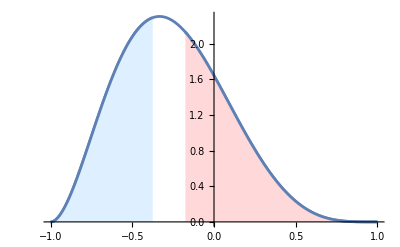

```mathematica
chat = 0.1;
alpha = 5;
beta = 3;
pdf[x_] :=PDF[BetaDistribution[alpha, beta], (1-x)/2]
plotlist1 = {Plot[pdf[x], {x, -1, 1},PlotRange->{{-1,1}, {0, Automatic}}, AxesLabel->{"", ""}]};
plotlist1 = Append[plotlist1, Plot[pdf[x], {x, -1, 1-2*AlphaUpperBoundary[alpha,beta,chat]}, Filling -> Axis,FillingStyle->LightBlue, PlotRange->{{-1,1}, {0, Automatic}}]];
plotlist1 = Append[plotlist1, Plot[pdf[x], {x, 1-2*AlphaLowerBoundary[alpha, beta, chat],1}, Filling -> Axis, FillingStyle -> LightRed, PlotRange->{{-1,1}, {0, Automatic}}]];
Show[plotlist1]
```

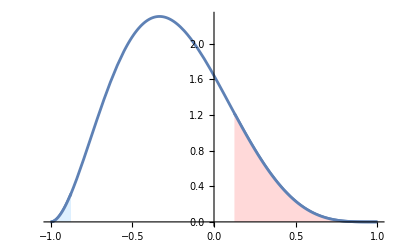

```mathematica
chat = 0.5;
alpha = 5;
beta = 3;
pdf[x_] :=PDF[BetaDistribution[alpha, beta], (1-x)/2]
plotlist2 = {Plot[pdf[x], {x, -1, 1},PlotRange->{{-1,1}, {0, Automatic}}, AxesLabel->{"", ""}]};
plotlist2 = Append[plotlist2, Plot[pdf[x], {x, -1, 1-2*AlphaUpperBoundary[alpha,beta,chat]}, Filling -> Axis,FillingStyle->LightBlue, PlotRange->{{-1,1}, {0, Automatic}}]];
plotlist2 = Append[plotlist2, Plot[pdf[x], {x, 1-2*AlphaLowerBoundary[alpha, beta, chat],1}, Filling -> Axis, FillingStyle -> LightRed, PlotRange->{{-1,1}, {0, Automatic}}]];
Show[plotlist2]
```

```mathematica
(* Insensitive (alpha) norm failure, unweighted by chat *)
Illustration1 = Table[{Plot[PDF[BetaDistribution[2, total- 2], x], {x,0,1}],ListDensityPlot[Flatten[Table[ {a/total, chat, AlphaAreaFailure[a, total-a, chat]},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1}], 1],Frame -> False, Axes->True, AxesOrigin->{0.1,0},AxesLabel->{"", ""}, PlotRange->{{0.1,0.9}, {0,0.9}}, InterpolationOrder->0, PlotLegends ->None, ColorFunction->(bwFunc[Rescale[#,{0,1}]]&),ColorFunctionScaling->False]}, {total, 4, 9}];
GraphicsRow[{GraphicsGrid[Partition[Flatten[Illustration1],4]], BarLegend[{bwFunc, {0,1}}]}]
```

-Graphics-

```mathematica
total = 4;
N[Flatten[Table[ {a/total, chat, AlphaAreaFailure[a, total-a, chat]},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1}], 1]]
total = 5;
N[Flatten[Table[ {a/total, chat, AlphaAreaFailure[a, total-a, chat]},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1}], 1]]
total = 6;
N[Flatten[Table[ {a/total, chat, AlphaAreaFailure[a, total-a, chat]},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1}], 1]]
total = 7;
N[Flatten[Table[ {a/total, chat, AlphaAreaFailure[a, total-a, chat]},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1}], 1]]
total = 8;
N[Flatten[Table[ {a/total, chat, AlphaAreaFailure[a, total-a, chat]},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1}], 1]]
total = 9;
N[Flatten[Table[ {a/total, chat, AlphaAreaFailure[a, total-a, chat]},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1}], 1]]
```

{{0.111111,0.1,0.662293},{0.111111,0.2,0.294542},{0.111111,0.3,0.2752},{0.111111,0.4,0.257273},{0.111111,0.5,0.240613},{0.111111,0.6,0.225098},{0.111111,0.7,0.210622},{0.111111,0.8,0.197093},{0.111111,0.9,0.184434},{0.138889,0.1,0.73691},{0.138889,0.2,0.310365},{0.138889,0.3,0.287614},{0.138889,0.4,0.266522},{0.138889,0.5,0.246932},{0.138889,0.6,0.228713},{0.138889,0.7,0.211751},{0.138889,0.8,0.195945},{0.138889,0.9,0.181207},{0.166667,0.1,0.772256},{0.166667,0.2,0.322031},{0.166667,0.3,0.296026},{0.166667,0.4,0.271908},{0.166667,0.5,0.249522},{0.166667,0.6,0.228736},{0.166667,0.7,0.20943},{0.166667,0.8,0.191499},{0.166667,0.9,0.174848},{0.194444,0.1,0.793906},{0.194444,0.2,0.51056},{0.194444,0.3,0.301706},{0.194444,0.4,0.274638},{0.194444,0.5,0.249532},{0.194444,0.6,0.22626},{0.194444,0.7,0.204705},{0.194444,0.8,0.184759},{0.194444,0.9,0.166326},{0.222222,0.1,0.808745},{0.222222,0.2,0.575251},{0.222222,0.3,0.305394},{0.222222,0.4,0.275405},{0.222222,0.5,0.247611},{0.222222,0.6,0.221897},{0.222222,0.7,0.198155},{0.222222,0.8,0.17628},{0.222222,0.9,0.156174},{0.25,0.1,0.819563},{0.25,0.2,0.614},{0.25,0.3,0.380687},{0.25,0.4,0.274625},{0.25,0.5,0.244141},{0.25,0.6,0.216},{0.25,0.7,0.190109},{0.25,0.8,0.166375},{0.25,0.9,0.144703},{0.277778,0.1,0.827741},{0.277778,0.2,0.640254},{0.277778,0.3,0.441201},{0.277778,0.4,0.272555},{0.277778,0.5,0.239347},{0.277778,0.6,0.20877},{0.277778,0.7,0.180755},{0.277778,0.8,0.155225},{0.277778,0.9,0.132096},{0.305556,0.1,0.834054},{0.305556,0.2,0.659136},{0.305556,0.3,0.480104},{0.305556,0.4,0.309193},{0.305556,0.5,0.233357},{0.305556,0.6,0.200314},{0.305556,0.7,0.170188},{0.305556,0.8,0.142927},{0.305556,0.9,0.118467},{0.333333,0.1,0.838968},{0.333333,0.2,0.673139},{0.333333,0.3,0.507283},{0.333333,0.4,0.349966},{0.333333,0.5,0.226225},{0.333333,0.6,0.190669},{0.333333,0.7,0.158439},{0.333333,0.8,0.129527},{0.333333,0.9,0.103894},{0.361111,0.1,0.842786},{0.361111,0.2,0.683644},{0.361111,0.3,0.526928},{0.361111,0.4,0.379021},{0.361111,0.5,0.251048},{0.361111,0.6,0.17982},{0.361111,0.7,0.145498},{0.361111,0.8,0.115038},{0.361111,0.9,0.0884482},{0.388889,0.1,0.845705},{0.388889,0.2,0.691479},{0.388889,0.3,0.54122},{0.388889,0.4,0.399894},{0.388889,0.5,0.274401},{0.388889,0.6,0.176622},{0.388889,0.7,0.131317},{0.388889,0.8,0.0994635},{0.388889,0.9,0.0722257},{0.416667,0.1,0.847862},{0.416667,0.2,0.697161},{0.416667,0.3,0.551413},{0.416667,0.4,0.414646},{0.416667,0.5,0.2917},{0.416667,0.6,0.188925},{0.416667,0.7,0.116965},{0.416667,0.8,0.0828159},{0.416667,0.9,0.0553976},{0.444444,0.1,0.849345},{0.444444,0.2,0.701022},{0.444444,0.3,0.558259},{0.444444,0.4,0.424494},{0.444444,0.5,0.303458},{0.444444,0.6,0.199356},{0.444444,0.7,0.117287},{0.444444,0.8,0.0651608},{0.444444,0.9,0.0383079},{0.472222,0.1,0.850214},{0.472222,0.2,0.703264},{0.472222,0.3,0.562209},{0.472222,0.4,0.430153},{0.472222,0.5,0.31027},{0.472222,0.6,0.205828},{0.472222,0.7,0.120256},{0.472222,0.8,0.0572943},{0.472222,0.9,0.0216904},{0.5,0.1,0.8505},{0.5,0.2,0.704},{0.5,0.3,0.5635},{0.5,0.4,0.432},{0.5,0.5,0.3125},{0.5,0.6,0.208},{0.5,0.7,0.1215},{0.5,0.8,0.056},{0.5,0.9,0.0145},{0.527778,0.1,0.850214},{0.527778,0.2,0.703264},{0.527778,0.3,0.562209},{0.527778,0.4,0.430153},{0.527778,0.5,0.31027},{0.527778,0.6,0.205828},{0.527778,0.7,0.120256},{0.527778,0.8,0.0572943},{0.527778,0.9,0.0216904},{0.555556,0.1,0.849345},{0.555556,0.2,0.701022},{0.555556,0.3,0.558259},{0.555556,0.4,0.424494},{0.555556,0.5,0.303458},{0.555556,0.6,0.199356},{0.555556,0.7,0.117287},{0.555556,0.8,0.0651608},{0.555556,0.9,0.0383079},{0.583333,0.1,0.847862},{0.583333,0.2,0.697161},{0.583333,0.3,0.551413},{0.583333,0.4,0.414646},{0.583333,0.5,0.2917},{0.583333,0.6,0.188925},{0.583333,0.7,0.116965},{0.583333,0.8,0.0828159},{0.583333,0.9,0.0553976},{0.611111,0.1,0.845705},{0.611111,0.2,0.691479},{0.611111,0.3,0.54122},{0.611111,0.4,0.399894},{0.611111,0.5,0.274401},{0.611111,0.6,0.176622},{0.611111,0.7,0.131317},{0.611111,0.8,0.0994635},{0.611111,0.9,0.0722257},{0.638889,0.1,0.842786},{0.638889,0.2,0.683644},{0.638889,0.3,0.526928},{0.638889,0.4,0.379021},{0.638889,0.5,0.251048},{0.638889,0.6,0.17982},{0.638889,0.7,0.145498},{0.638889,0.8,0.115038},{0.638889,0.9,0.0884482},{0.666667,0.1,0.838968},{0.666667,0.2,0.673139},{0.666667,0.3,0.507283},{0.666667,0.4,0.349966},{0.666667,0.5,0.226225},{0.666667,0.6,0.190669},{0.666667,0.7,0.158439},{0.666667,0.8,0.129527},{0.666667,0.9,0.103894},{0.694444,0.1,0.834054},{0.694444,0.2,0.659136},{0.694444,0.3,0.480104},{0.694444,0.4,0.309193},{0.694444,0.5,0.233357},{0.694444,0.6,0.200314},{0.694444,0.7,0.170188},{0.694444,0.8,0.142927},{0.694444,0.9,0.118467},{0.722222,0.1,0.827741},{0.722222,0.2,0.640254},{0.722222,0.3,0.441201},{0.722222,0.4,0.272555},{0.722222,0.5,0.239347},{0.722222,0.6,0.20877},{0.722222,0.7,0.180755},{0.722222,0.8,0.155225},{0.722222,0.9,0.132096},{0.75,0.1,0.819563},{0.75,0.2,0.614},{0.75,0.3,0.380687},{0.75,0.4,0.274625},{0.75,0.5,0.244141},{0.75,0.6,0.216},{0.75,0.7,0.190109},{0.75,0.8,0.166375},{0.75,0.9,0.144703},{0.777778,0.1,0.808745},{0.777778,0.2,0.575251},{0.777778,0.3,0.305394},{0.777778,0.4,0.275405},{0.777778,0.5,0.247611},{0.777778,0.6,0.221897},{0.777778,0.7,0.198155},{0.777778,0.8,0.17628},{0.777778,0.9,0.156174},{0.805556,0.1,0.793906},{0.805556,0.2,0.51056},{0.805556,0.3,0.301706},{0.805556,0.4,0.274638},{0.805556,0.5,0.249532},{0.805556,0.6,0.22626},{0.805556,0.7,0.204705},{0.805556,0.8,0.184759},{0.805556,0.9,0.166326},{0.833333,0.1,0.772256},{0.833333,0.2,0.322031},{0.833333,0.3,0.296026},{0.833333,0.4,0.271908},{0.833333,0.5,0.249522},{0.833333,0.6,0.228736},{0.833333,0.7,0.20943},{0.833333,0.8,0.191499},{0.833333,0.9,0.174848},{0.861111,0.1,0.73691},{0.861111,0.2,0.310365},{0.861111,0.3,0.287614},{0.861111,0.4,0.266522},{0.861111,0.5,0.246932},{0.861111,0.6,0.228713},{0.861111,0.7,0.211751},{0.861111,0.8,0.195945},{0.861111,0.9,0.181207},{0.888889,0.1,0.662293},{0.888889,0.2,0.294542},{0.888889,0.3,0.2752},{0.888889,0.4,0.257273},{0.888889,0.5,0.240613},{0.888889,0.6,0.225098},{0.888889,0.7,0.210622},{0.888889,0.8,0.197093},{0.888889,0.9,0.184434}}

{{0.111111,0.1,0.621781},{0.111111,0.2,0.303517},{0.111111,0.3,0.281291},{0.111111,0.4,0.260752},{0.111111,0.5,0.241738},{0.111111,0.6,0.224108},{0.111111,0.7,0.207742},{0.111111,0.8,0.192532},{0.111111,0.9,0.178388},{0.133333,0.1,0.691542},{0.133333,0.2,0.314417},{0.133333,0.3,0.289157},{0.133333,0.4,0.265825},{0.133333,0.5,0.244255},{0.133333,0.6,0.224299},{0.133333,0.7,0.205829},{0.133333,0.8,0.188729},{0.133333,0.9,0.172896},{0.155556,0.1,0.728921},{0.155556,0.2,0.322595},{0.155556,0.3,0.29443},{0.155556,0.4,0.268428},{0.155556,0.5,0.244425},{0.155556,0.6,0.222272},{0.155556,0.7,0.201835},{0.155556,0.8,0.182992},{0.155556,0.9,0.165632},{0.177778,0.1,0.753179},{0.177778,0.2,0.405413},{0.177778,0.3,0.297846},{0.177778,0.4,0.269257},{0.177778,0.5,0.242907},{0.177778,0.6,0.218651},{0.177778,0.7,0.196355},{0.177778,0.8,0.175893},{0.177778,0.9,0.157145},{0.2,0.1,0.770455},{0.2,0.2,0.484275},{0.2,0.3,0.299866},{0.2,0.4,0.268739},{0.2,0.5,0.2401},{0.2,0.6,0.213814},{0.2,0.7,0.189747},{0.2,0.8,0.167772},{0.2,0.9,0.147763},{0.222222,0.1,0.783452},{0.222222,0.2,0.531684},{0.222222,0.3,0.300787},{0.222222,0.4,0.267149},{0.222222,0.5,0.236259},{0.222222,0.6,0.207997},{0.222222,0.7,0.182235},{0.222222,0.8,0.158846},{0.222222,0.9,0.1377},{0.244444,0.1,0.793578},{0.244444,0.2,0.564517},{0.244444,0.3,0.334068},{0.244444,0.4,0.264668},{0.244444,0.5,0.231548},{0.244444,0.6,0.201351},{0.244444,0.7,0.173962},{0.244444,0.8,0.149256},{0.244444,0.9,0.127099},{0.266667,0.1,0.801654},{0.266667,0.2,0.588798},{0.266667,0.3,0.378641},{0.266667,0.4,0.261415},{0.266667,0.5,0.226073},{0.266667,0.6,0.193974},{0.266667,0.7,0.165022},{0.266667,0.8,0.139097},{0.266667,0.9,0.116063},{0.288889,0.1,0.808192},{0.288889,0.2,0.607445},{0.288889,0.3,0.411959},{0.288889,0.4,0.259579},{0.288889,0.5,0.219899},{0.288889,0.6,0.185926},{0.288889,0.7,0.155475},{0.288889,0.8,0.128438},{0.288889,0.9,0.104674},{0.311111,0.1,0.813532},{0.311111,0.2,0.622097},{0.311111,0.3,0.437531},{0.311111,0.4,0.282172},{0.311111,0.5,0.213065},{0.311111,0.6,0.17724},{0.311111,0.7,0.14536},{0.311111,0.8,0.11733},{0.311111,0.9,0.0930086},{0.333333,0.1,0.817908},{0.333333,0.2,0.633754},{0.333333,0.3,0.457518},{0.333333,0.4,0.304677},{0.333333,0.5,0.205587},{0.333333,0.6,0.167932},{0.333333,0.7,0.134701},{0.333333,0.8,0.105818},{0.333333,0.9,0.0811406},{0.355556,0.1,0.821484},{0.355556,0.2,0.64307},{0.355556,0.3,0.473276},{0.355556,0.4,0.323603},{0.355556,0.5,0.210734},{0.355556,0.6,0.158003},{0.355556,0.7,0.123515},{0.355556,0.8,0.0939477},{0.355556,0.9,0.0691586},{0.377778,0.1,0.824381},{0.377778,0.2,0.650485},{0.377778,0.3,0.48569},{0.377778,0.4,0.338951},{0.377778,0.5,0.221321},{0.377778,0.6,0.147658},{0.377778,0.7,0.111814},{0.377778,0.8,0.0817735},{0.377778,0.9,0.057175},{0.4,0.1,0.826687},{0.4,0.2,0.656307},{0.4,0.3,0.495359},{0.4,0.4,0.351091},{0.4,0.5,0.2315},{0.4,0.6,0.145331},{0.4,0.7,0.0996147},{0.4,0.8,0.0693683},{0.4,0.9,0.0453427},{0.422222,0.1,0.828466},{0.422222,0.2,0.660751},{0.422222,0.3,0.502696},{0.422222,0.4,0.360387},{0.422222,0.5,0.239998},{0.422222,0.6,0.147523},{0.422222,0.7,0.0881206},{0.422222,0.8,0.056839},{0.422222,0.9,0.0338786},{0.444444,0.1,0.829763},{0.444444,0.2,0.663968},{0.444444,0.3,0.507984},{0.444444,0.4,0.367123},{0.444444,0.5,0.246446},{0.444444,0.6,0.150487},{0.444444,0.7,0.0827557},{0.444444,0.8,0.0443482},{0.444444,0.9,0.0230992},{0.466667,0.1,0.830611},{0.466667,0.2,0.66606},{0.466667,0.3,0.511413},{0.466667,0.4,0.371506},{0.466667,0.5,0.250752},{0.466667,0.6,0.152899},{0.466667,0.7,0.0806759},{0.466667,0.8,0.0351481},{0.466667,0.9,0.0134768},{0.488889,0.1,0.83103},{0.488889,0.2,0.667091},{0.488889,0.3,0.5131},{0.488889,0.4,0.373665},{0.488889,0.5,0.252901},{0.488889,0.6,0.154209},{0.488889,0.7,0.079988},{0.488889,0.8,0.0312115},{0.488889,0.9,0.00665553},{0.511111,0.1,0.83103},{0.511111,0.2,0.667091},{0.511111,0.3,0.5131},{0.511111,0.4,0.373665},{0.511111,0.5,0.252901},{0.511111,0.6,0.154209},{0.511111,0.7,0.079988},{0.511111,0.8,0.0312115},{0.511111,0.9,0.00665553},{0.533333,0.1,0.830611},{0.533333,0.2,0.66606},{0.533333,0.3,0.511413},{0.533333,0.4,0.371506},{0.533333,0.5,0.250752},{0.533333,0.6,0.152899},{0.533333,0.7,0.0806759},{0.533333,0.8,0.0351481},{0.533333,0.9,0.0134768},{0.555556,0.1,0.829763},{0.555556,0.2,0.663968},{0.555556,0.3,0.507984},{0.555556,0.4,0.367123},{0.555556,0.5,0.246446},{0.555556,0.6,0.150487},{0.555556,0.7,0.0827557},{0.555556,0.8,0.0443482},{0.555556,0.9,0.0230992},{0.577778,0.1,0.828466},{0.577778,0.2,0.660751},{0.577778,0.3,0.502696},{0.577778,0.4,0.360387},{0.577778,0.5,0.239998},{0.577778,0.6,0.147523},{0.577778,0.7,0.0881206},{0.577778,0.8,0.056839},{0.577778,0.9,0.0338786},{0.6,0.1,0.826687},{0.6,0.2,0.656307},{0.6,0.3,0.495359},{0.6,0.4,0.351091},{0.6,0.5,0.2315},{0.6,0.6,0.145331},{0.6,0.7,0.0996147},{0.6,0.8,0.0693683},{0.6,0.9,0.0453427},{0.622222,0.1,0.824381},{0.622222,0.2,0.650485},{0.622222,0.3,0.48569},{0.622222,0.4,0.338951},{0.622222,0.5,0.221321},{0.622222,0.6,0.147658},{0.622222,0.7,0.111814},{0.622222,0.8,0.0817735},{0.622222,0.9,0.057175},{0.644444,0.1,0.821484},{0.644444,0.2,0.64307},{0.644444,0.3,0.473276},{0.644444,0.4,0.323603},{0.644444,0.5,0.210734},{0.644444,0.6,0.158003},{0.644444,0.7,0.123515},{0.644444,0.8,0.0939477},{0.644444,0.9,0.0691586},{0.666667,0.1,0.817908},{0.666667,0.2,0.633754},{0.666667,0.3,0.457518},{0.666667,0.4,0.304677},{0.666667,0.5,0.205587},{0.666667,0.6,0.167932},{0.666667,0.7,0.134701},{0.666667,0.8,0.105818},{0.666667,0.9,0.0811406},{0.688889,0.1,0.813532},{0.688889,0.2,0.622097},{0.688889,0.3,0.437531},{0.688889,0.4,0.282172},{0.688889,0.5,0.213065},{0.688889,0.6,0.17724},{0.688889,0.7,0.14536},{0.688889,0.8,0.11733},{0.688889,0.9,0.0930086},{0.711111,0.1,0.808192},{0.711111,0.2,0.607445},{0.711111,0.3,0.411959},{0.711111,0.4,0.259579},{0.711111,0.5,0.219899},{0.711111,0.6,0.185926},{0.711111,0.7,0.155475},{0.711111,0.8,0.128438},{0.711111,0.9,0.104674},{0.733333,0.1,0.801654},{0.733333,0.2,0.588798},{0.733333,0.3,0.378641},{0.733333,0.4,0.261415},{0.733333,0.5,0.226073},{0.733333,0.6,0.193974},{0.733333,0.7,0.165022},{0.733333,0.8,0.139097},{0.733333,0.9,0.116063},{0.755556,0.1,0.793578},{0.755556,0.2,0.564517},{0.755556,0.3,0.334068},{0.755556,0.4,0.264668},{0.755556,0.5,0.231548},{0.755556,0.6,0.201351},{0.755556,0.7,0.173962},{0.755556,0.8,0.149256},{0.755556,0.9,0.127099},{0.777778,0.1,0.783452},{0.777778,0.2,0.531684},{0.777778,0.3,0.300787},{0.777778,0.4,0.267149},{0.777778,0.5,0.236259},{0.777778,0.6,0.207997},{0.777778,0.7,0.182235},{0.777778,0.8,0.158846},{0.777778,0.9,0.1377},{0.8,0.1,0.770455},{0.8,0.2,0.484275},{0.8,0.3,0.299866},{0.8,0.4,0.268739},{0.8,0.5,0.2401},{0.8,0.6,0.213814},{0.8,0.7,0.189747},{0.8,0.8,0.167772},{0.8,0.9,0.147763},{0.822222,0.1,0.753179},{0.822222,0.2,0.405413},{0.822222,0.3,0.297846},{0.822222,0.4,0.269257},{0.822222,0.5,0.242907},{0.822222,0.6,0.218651},{0.822222,0.7,0.196355},{0.822222,0.8,0.175893},{0.822222,0.9,0.157145},{0.844444,0.1,0.728921},{0.844444,0.2,0.322595},{0.844444,0.3,0.29443},{0.844444,0.4,0.268428},{0.844444,0.5,0.244425},{0.844444,0.6,0.222272},{0.844444,0.7,0.201835},{0.844444,0.8,0.182992},{0.844444,0.9,0.165632},{0.866667,0.1,0.691542},{0.866667,0.2,0.314417},{0.866667,0.3,0.289157},{0.866667,0.4,0.265825},{0.866667,0.5,0.244255},{0.866667,0.6,0.224299},{0.866667,0.7,0.205829},{0.866667,0.8,0.188729},{0.866667,0.9,0.172896},{0.888889,0.1,0.621781},{0.888889,0.2,0.303517},{0.888889,0.3,0.281291},{0.888889,0.4,0.260752},{0.888889,0.5,0.241738},{0.888889,0.6,0.224108},{0.888889,0.7,0.207742},{0.888889,0.8,0.192532},{0.888889,0.9,0.178388}}

{{0.111111,0.1,0.588459},{0.111111,0.2,0.309536},{0.111111,0.3,0.284743},{0.111111,0.4,0.2619},{0.111111,0.5,0.240831},{0.111111,0.6,0.221383},{0.111111,0.7,0.20342},{0.111111,0.8,0.18682},{0.111111,0.9,0.171478},{0.12963,0.1,0.652557},{0.12963,0.2,0.317306},{0.12963,0.3,0.289764},{0.12963,0.4,0.264415},{0.12963,0.5,0.241078},{0.12963,0.6,0.219596},{0.12963,0.7,0.199824},{0.12963,0.8,0.181631},{0.12963,0.9,0.1649},{0.148148,0.1,0.690313},{0.148148,0.2,0.323191},{0.148148,0.3,0.293011},{0.148148,0.4,0.265262},{0.148148,0.5,0.239768},{0.148148,0.6,0.216369},{0.148148,0.7,0.194915},{0.148148,0.8,0.175267},{0.148148,0.9,0.157296},{0.166667,0.1,0.716038},{0.166667,0.2,0.32768},{0.166667,0.3,0.29494},{0.166667,0.4,0.26487},{0.166667,0.5,0.237305},{0.166667,0.6,0.212084},{0.166667,0.7,0.189054},{0.166667,0.8,0.16807},{0.166667,0.9,0.148992},{0.185185,0.1,0.734959},{0.185185,0.2,0.40913},{0.185185,0.3,0.29585},{0.185185,0.4,0.263518},{0.185185,0.5,0.233946},{0.185185,0.6,0.206982},{0.185185,0.7,0.182471},{0.185185,0.8,0.16026},{0.185185,0.9,0.140199},{0.203704,0.1,0.749553},{0.203704,0.2,0.460016},{0.203704,0.3,0.295947},{0.203704,0.4,0.261392},{0.203704,0.5,0.229866},{0.203704,0.6,0.201226},{0.203704,0.7,0.175317},{0.203704,0.8,0.151982},{0.203704,0.9,0.13106},{0.222222,0.1,0.761172},{0.222222,0.2,0.496427},{0.222222,0.3,0.295371},{0.222222,0.4,0.258621},{0.222222,0.5,0.225182},{0.222222,0.6,0.194924},{0.222222,0.7,0.167698},{0.222222,0.8,0.143339},{0.222222,0.9,0.121676},{0.240741,0.1,0.770634},{0.240741,0.2,0.52409},{0.240741,0.3,0.307867},{0.240741,0.4,0.255294},{0.240741,0.5,0.219974},{0.240741,0.6,0.188152},{0.240741,0.7,0.159685},{0.240741,0.8,0.134404},{0.240741,0.9,0.112123},{0.259259,0.1,0.778463},{0.259259,0.2,0.545878},{0.259259,0.3,0.336782},{0.259259,0.4,0.251475},{0.259259,0.5,0.214299},{0.259259,0.6,0.180963},{0.259259,0.7,0.151332},{0.259259,0.8,0.125234},{0.259259,0.9,0.102465},{0.277778,0.1,0.785013},{0.277778,0.2,0.56345},{0.277778,0.3,0.362276},{0.277778,0.4,0.247206},{0.277778,0.5,0.208194},{0.277778,0.6,0.173392},{0.277778,0.7,0.142678},{0.277778,0.8,0.115873},{0.277778,0.9,0.0927569},{0.296296,0.1,0.790535},{0.296296,0.2,0.577847},{0.296296,0.3,0.383755},{0.296296,0.4,0.247472},{0.296296,0.5,0.201684},{0.296296,0.6,0.165465},{0.296296,0.7,0.133752},{0.296296,0.8,0.106361},{0.296296,0.9,0.0830506},{0.314815,0.1,0.79521},{0.314815,0.2,0.589763},{0.314815,0.3,0.401738},{0.314815,0.4,0.25833},{0.314815,0.5,0.194783},{0.314815,0.6,0.157199},{0.314815,0.7,0.12458},{0.314815,0.8,0.0967375},{0.314815,0.9,0.0734005},{0.333333,0.1,0.799172},{0.333333,0.2,0.59968},{0.333333,0.3,0.416783},{0.333333,0.4,0.270748},{0.333333,0.5,0.1875},{0.333333,0.6,0.148605},{0.333333,0.7,0.115184},{0.333333,0.8,0.08704},{0.333333,0.9,0.0638661},{0.351852,0.1,0.802523},{0.351852,0.2,0.607945},{0.351852,0.3,0.42935},{0.351852,0.4,0.282527},{0.351852,0.5,0.184903},{0.351852,0.6,0.139691},{0.351852,0.7,0.105587},{0.351852,0.8,0.0773124},{0.351852,0.9,0.0545157},{0.37037,0.1,0.80534},{0.37037,0.2,0.614811},{0.37037,0.3,0.4398},{0.37037,0.4,0.293019},{0.37037,0.5,0.187216},{0.37037,0.6,0.130462},{0.37037,0.7,0.0958121},{0.37037,0.8,0.0676058},{0.37037,0.9,0.0454307},{0.388889,0.1,0.807684},{0.388889,0.2,0.620468},{0.388889,0.3,0.448412},{0.388889,0.4,0.302039},{0.388889,0.5,0.191176},{0.388889,0.6,0.122357},{0.388889,0.7,0.0858896},{0.388889,0.8,0.0579831},{0.388889,0.9,0.0367101},{0.407407,0.1,0.8096},{0.407407,0.2,0.625058},{0.407407,0.3,0.455398},{0.407407,0.4,0.309562},{0.407407,0.5,0.195443},{0.407407,0.6,0.118199},{0.407407,0.7,0.0758568},{0.407407,0.8,0.0485235},{0.407407,0.9,0.028476},{0.425926,0.1,0.811126},{0.425926,0.2,0.628688},{0.425926,0.3,0.460921},{0.425926,0.4,0.315623},{0.425926,0.5,0.199373},{0.425926,0.6,0.116392},{0.425926,0.7,0.066524},{0.425926,0.8,0.039329},{0.425926,0.9,0.0208792},{0.444444,0.1,0.812286},{0.444444,0.2,0.631437},{0.444444,0.3,0.465103},{0.444444,0.4,0.320272},{0.444444,0.5,0.202636},{0.444444,0.6,0.115783},{0.444444,0.7,0.0600731},{0.444444,0.8,0.0305323},{0.444444,0.9,0.0141065},{0.462963,0.1,0.813102},{0.462963,0.2,0.633362},{0.462963,0.3,0.468031},{0.462963,0.4,0.323556},{0.462963,0.5,0.205053},{0.462963,0.6,0.115709},{0.462963,0.7,0.056071},{0.462963,0.8,0.0230981},{0.462963,0.9,0.00838496},{0.481481,0.1,0.813586},{0.481481,0.2,0.634502},{0.481481,0.3,0.469765},{0.481481,0.4,0.325511},{0.481481,0.5,0.206533},{0.481481,0.6,0.115792},{0.481481,0.7,0.0539069},{0.481481,0.8,0.0186008},{0.481481,0.9,0.00403144},{0.5,0.1,0.813746},{0.5,0.2,0.63488},{0.5,0.3,0.470339},{0.5,0.4,0.32616},{0.5,0.5,0.207031},{0.5,0.6,0.11584},{0.5,0.7,0.0532237},{0.5,0.8,0.01712},{0.5,0.9,0.00231625},{0.518519,0.1,0.813586},{0.518519,0.2,0.634502},{0.518519,0.3,0.469765},{0.518519,0.4,0.325511},{0.518519,0.5,0.206533},{0.518519,0.6,0.115792},{0.518519,0.7,0.0539069},{0.518519,0.8,0.0186008},{0.518519,0.9,0.00403144},{0.537037,0.1,0.813102},{0.537037,0.2,0.633362},{0.537037,0.3,0.468031},{0.537037,0.4,0.323556},{0.537037,0.5,0.205053},{0.537037,0.6,0.115709},{0.537037,0.7,0.056071},{0.537037,0.8,0.0230981},{0.537037,0.9,0.00838496},{0.555556,0.1,0.812286},{0.555556,0.2,0.631437},{0.555556,0.3,0.465103},{0.555556,0.4,0.320272},{0.555556,0.5,0.202636},{0.555556,0.6,0.115783},{0.555556,0.7,0.0600731},{0.555556,0.8,0.0305323},{0.555556,0.9,0.0141065},{0.574074,0.1,0.811126},{0.574074,0.2,0.628688},{0.574074,0.3,0.460921},{0.574074,0.4,0.315623},{0.574074,0.5,0.199373},{0.574074,0.6,0.116392},{0.574074,0.7,0.066524},{0.574074,0.8,0.039329},{0.574074,0.9,0.0208792},{0.592593,0.1,0.8096},{0.592593,0.2,0.625058},{0.592593,0.3,0.455398},{0.592593,0.4,0.309562},{0.592593,0.5,0.195443},{0.592593,0.6,0.118199},{0.592593,0.7,0.0758568},{0.592593,0.8,0.0485235},{0.592593,0.9,0.028476},{0.611111,0.1,0.807684},{0.611111,0.2,0.620468},{0.611111,0.3,0.448412},{0.611111,0.4,0.302039},{0.611111,0.5,0.191176},{0.611111,0.6,0.122357},{0.611111,0.7,0.0858896},{0.611111,0.8,0.0579831},{0.611111,0.9,0.0367101},{0.62963,0.1,0.80534},{0.62963,0.2,0.614811},{0.62963,0.3,0.4398},{0.62963,0.4,0.293019},{0.62963,0.5,0.187216},{0.62963,0.6,0.130462},{0.62963,0.7,0.0958121},{0.62963,0.8,0.0676058},{0.62963,0.9,0.0454307},{0.648148,0.1,0.802523},{0.648148,0.2,0.607945},{0.648148,0.3,0.42935},{0.648148,0.4,0.282527},{0.648148,0.5,0.184903},{0.648148,0.6,0.139691},{0.648148,0.7,0.105587},{0.648148,0.8,0.0773124},{0.648148,0.9,0.0545157},{0.666667,0.1,0.799172},{0.666667,0.2,0.59968},{0.666667,0.3,0.416783},{0.666667,0.4,0.270748},{0.666667,0.5,0.1875},{0.666667,0.6,0.148605},{0.666667,0.7,0.115184},{0.666667,0.8,0.08704},{0.666667,0.9,0.0638661},{0.685185,0.1,0.79521},{0.685185,0.2,0.589763},{0.685185,0.3,0.401738},{0.685185,0.4,0.25833},{0.685185,0.5,0.194783},{0.685185,0.6,0.157199},{0.685185,0.7,0.12458},{0.685185,0.8,0.0967375},{0.685185,0.9,0.0734005},{0.703704,0.1,0.790535},{0.703704,0.2,0.577847},{0.703704,0.3,0.383755},{0.703704,0.4,0.247472},{0.703704,0.5,0.201684},{0.703704,0.6,0.165465},{0.703704,0.7,0.133752},{0.703704,0.8,0.106361},{0.703704,0.9,0.0830506},{0.722222,0.1,0.785013},{0.722222,0.2,0.56345},{0.722222,0.3,0.362276},{0.722222,0.4,0.247206},{0.722222,0.5,0.208194},{0.722222,0.6,0.173392},{0.722222,0.7,0.142678},{0.722222,0.8,0.115873},{0.722222,0.9,0.0927569},{0.740741,0.1,0.778463},{0.740741,0.2,0.545878},{0.740741,0.3,0.336782},{0.740741,0.4,0.251475},{0.740741,0.5,0.214299},{0.740741,0.6,0.180963},{0.740741,0.7,0.151332},{0.740741,0.8,0.125234},{0.740741,0.9,0.102465},{0.759259,0.1,0.770634},{0.759259,0.2,0.52409},{0.759259,0.3,0.307867},{0.759259,0.4,0.255294},{0.759259,0.5,0.219974},{0.759259,0.6,0.188152},{0.759259,0.7,0.159685},{0.759259,0.8,0.134404},{0.759259,0.9,0.112123},{0.777778,0.1,0.761172},{0.777778,0.2,0.496427},{0.777778,0.3,0.295371},{0.777778,0.4,0.258621},{0.777778,0.5,0.225182},{0.777778,0.6,0.194924},{0.777778,0.7,0.167698},{0.777778,0.8,0.143339},{0.777778,0.9,0.121676},{0.796296,0.1,0.749553},{0.796296,0.2,0.460016},{0.796296,0.3,0.295947},{0.796296,0.4,0.261392},{0.796296,0.5,0.229866},{0.796296,0.6,0.201226},{0.796296,0.7,0.175317},{0.796296,0.8,0.151982},{0.796296,0.9,0.13106},{0.814815,0.1,0.734959},{0.814815,0.2,0.40913},{0.814815,0.3,0.29585},{0.814815,0.4,0.263518},{0.814815,0.5,0.233946},{0.814815,0.6,0.206982},{0.814815,0.7,0.182471},{0.814815,0.8,0.16026},{0.814815,0.9,0.140199},{0.833333,0.1,0.716038},{0.833333,0.2,0.32768},{0.833333,0.3,0.29494},{0.833333,0.4,0.26487},{0.833333,0.5,0.237305},{0.833333,0.6,0.212084},{0.833333,0.7,0.189054},{0.833333,0.8,0.16807},{0.833333,0.9,0.148992},{0.851852,0.1,0.690313},{0.851852,0.2,0.323191},{0.851852,0.3,0.293011},{0.851852,0.4,0.265262},{0.851852,0.5,0.239768},{0.851852,0.6,0.216369},{0.851852,0.7,0.194915},{0.851852,0.8,0.175267},{0.851852,0.9,0.157296},{0.87037,0.1,0.652557},{0.87037,0.2,0.317306},{0.87037,0.3,0.289764},{0.87037,0.4,0.264415},{0.87037,0.5,0.241078},{0.87037,0.6,0.219596},{0.87037,0.7,0.199824},{0.87037,0.8,0.181631},{0.87037,0.9,0.1649},{0.888889,0.1,0.588459},{0.888889,0.2,0.309536},{0.888889,0.3,0.284743},{0.888889,0.4,0.2619},{0.888889,0.5,0.240831},{0.888889,0.6,0.221383},{0.888889,0.7,0.20342},{0.888889,0.8,0.18682},{0.888889,0.9,0.171478}}

{{0.111111,0.1,0.560617},{0.111111,0.2,0.313637},{0.111111,0.3,0.28652},{0.111111,0.4,0.26161},{0.111111,0.5,0.238721},{0.111111,0.6,0.217686},{0.111111,0.7,0.198355},{0.111111,0.8,0.180592},{0.111111,0.9,0.164275},{0.126984,0.1,0.618932},{0.126984,0.2,0.319288},{0.126984,0.3,0.28965},{0.126984,0.4,0.262463},{0.126984,0.5,0.237538},{0.126984,0.6,0.214703},{0.126984,0.7,0.193799},{0.126984,0.8,0.174682},{0.126984,0.9,0.157216},{0.142857,0.1,0.655982},{0.142857,0.2,0.323579},{0.142857,0.3,0.291515},{0.142857,0.4,0.262144},{0.142857,0.5,0.235282},{0.142857,0.6,0.210753},{0.142857,0.7,0.188394},{0.142857,0.8,0.168047},{0.142857,0.9,0.149566},{0.15873,0.1,0.682307},{0.15873,0.2,0.32683},{0.15873,0.3,0.292412},{0.15873,0.4,0.260932},{0.15873,0.5,0.232213},{0.15873,0.6,0.206082},{0.15873,0.7,0.182367},{0.15873,0.8,0.160904},{0.15873,0.9,0.141531},{0.174603,0.1,0.702226},{0.174603,0.2,0.3551},{0.174603,0.3,0.292546},{0.174603,0.4,0.259014},{0.174603,0.5,0.228506},{0.174603,0.6,0.20085},{0.174603,0.7,0.175873},{0.174603,0.8,0.153397},{0.174603,0.9,0.133247},{0.190476,0.1,0.717923},{0.190476,0.2,0.402326},{0.190476,0.3,0.29206},{0.190476,0.4,0.256522},{0.190476,0.5,0.224281},{0.190476,0.6,0.195171},{0.190476,0.7,0.169015},{0.190476,0.8,0.145625},{0.190476,0.9,0.124813},{0.206349,0.1,0.730648},{0.206349,0.2,0.438618},{0.206349,0.3,0.291058},{0.206349,0.4,0.253549},{0.206349,0.5,0.219623},{0.206349,0.6,0.189124},{0.206349,0.7,0.161869},{0.206349,0.8,0.137663},{0.206349,0.9,0.116297},{0.222222,0.1,0.741177},{0.222222,0.2,0.467299},{0.222222,0.3,0.289614},{0.222222,0.4,0.250163},{0.222222,0.5,0.214595},{0.222222,0.6,0.182764},{0.222222,0.7,0.15449},{0.222222,0.8,0.129563},{0.222222,0.9,0.107755},{0.238095,0.1,0.750025},{0.238095,0.2,0.490548},{0.238095,0.3,0.292758},{0.238095,0.4,0.246412},{0.238095,0.5,0.209238},{0.238095,0.6,0.176135},{0.238095,0.7,0.14692},{0.238095,0.8,0.121369},{0.238095,0.9,0.0992324},{0.253968,0.1,0.757546},{0.253968,0.2,0.509758},{0.253968,0.3,0.309287},{0.253968,0.4,0.242332},{0.253968,0.5,0.203587},{0.253968,0.6,0.169267},{0.253968,0.7,0.139189},{0.253968,0.8,0.113115},{0.253968,0.9,0.0907675},{0.269841,0.1,0.763994},{0.269841,0.2,0.525856},{0.269841,0.3,0.326965},{0.269841,0.4,0.237948},{0.269841,0.5,0.197664},{0.269841,0.6,0.162184},{0.269841,0.7,0.131325},{0.269841,0.8,0.104832},{0.269841,0.9,0.0823964},{0.285714,0.1,0.769556},{0.285714,0.2,0.539486},{0.285714,0.3,0.343434},{0.285714,0.4,0.23328},{0.285714,0.5,0.191485},{0.285714,0.6,0.154902},{0.285714,0.7,0.123349},{0.285714,0.8,0.0965487},{0.285714,0.9,0.0741541},{0.301587,0.1,0.774373},{0.301587,0.2,0.551111},{0.301587,0.3,0.35821},{0.301587,0.4,0.233202},{0.301587,0.5,0.185062},{0.301587,0.6,0.147437},{0.301587,0.7,0.115281},{0.301587,0.8,0.0882919},{0.301587,0.9,0.0660764},{0.31746,0.1,0.778555},{0.31746,0.2,0.561072},{0.31746,0.3,0.371267},{0.31746,0.4,0.23793},{0.31746,0.5,0.178403},{0.31746,0.6,0.1398},{0.31746,0.7,0.10714},{0.31746,0.8,0.0800903},{0.31746,0.9,0.0582015},{0.333333,0.1,0.782185},{0.333333,0.2,0.569627},{0.333333,0.3,0.382712},{0.333333,0.4,0.244341},{0.333333,0.5,0.171513},{0.333333,0.6,0.132002},{0.333333,0.7,0.0989462},{0.333333,0.8,0.0719746},{0.333333,0.9,0.0505709},{0.349206,0.1,0.785331},{0.349206,0.2,0.576974},{0.349206,0.3,0.392679},{0.349206,0.4,0.251161},{0.349206,0.5,0.166249},{0.349206,0.6,0.124051},{0.349206,0.7,0.0907189},{0.349206,0.8,0.0639787},{0.349206,0.9,0.0432308},{0.365079,0.1,0.788047},{0.365079,0.2,0.583265},{0.365079,0.3,0.401302},{0.365079,0.4,0.257787},{0.365079,0.5,0.164054},{0.365079,0.6,0.115957},{0.365079,0.7,0.0824818},{0.365079,0.8,0.0561413},{0.365079,0.9,0.036233},{0.380952,0.1,0.790373},{0.380952,0.2,0.588622},{0.380952,0.3,0.4087},{0.380952,0.4,0.263913},{0.380952,0.5,0.163728},{0.380952,0.6,0.107807},{0.380952,0.7,0.0742617},{0.380952,0.8,0.0485072},{0.380952,0.9,0.0296361},{0.396825,0.1,0.792346},{0.396825,0.2,0.59314},{0.396825,0.3,0.414974},{0.396825,0.4,0.269383},{0.396825,0.5,0.164428},{0.396825,0.6,0.101011},{0.396825,0.7,0.0660904},{0.396825,0.8,0.0411286},{0.396825,0.9,0.0235063},{0.412698,0.1,0.793993},{0.412698,0.2,0.596893},{0.412698,0.3,0.420208},{0.412698,0.4,0.274118},{0.412698,0.5,0.165621},{0.412698,0.6,0.0961146},{0.412698,0.7,0.0580068},{0.412698,0.8,0.0340672},{0.412698,0.9,0.0179176},{0.428571,0.1,0.795335},{0.428571,0.2,0.599941},{0.428571,0.3,0.424472},{0.428571,0.4,0.27808},{0.428571,0.5,0.166964},{0.428571,0.6,0.0927219},{0.428571,0.7,0.0504946},{0.428571,0.8,0.0273956},{0.428571,0.9,0.0129515},{0.444444,0.1,0.796389},{0.444444,0.2,0.602328},{0.444444,0.3,0.427822},{0.444444,0.4,0.281253},{0.444444,0.5,0.168234},{0.444444,0.6,0.0904369},{0.444444,0.7,0.0444913},{0.444444,0.8,0.021199},{0.444444,0.9,0.00869499},{0.460317,0.1,0.797169},{0.460317,0.2,0.604091},{0.460317,0.3,0.430298},{0.460317,0.4,0.283631},{0.460317,0.5,0.169288},{0.460317,0.6,0.0889592},{0.460317,0.7,0.0401308},{0.460317,0.8,0.0157734},{0.460317,0.9,0.00523527},{0.47619,0.1,0.797684},{0.47619,0.2,0.605252},{0.47619,0.3,0.431932},{0.47619,0.4,0.285215},{0.47619,0.5,0.170036},{0.47619,0.6,0.0880808},{0.47619,0.7,0.0373164},{0.47619,0.8,0.0118796},{0.47619,0.9,0.00264859},{0.492063,0.1,0.79794},{0.492063,0.2,0.605829},{0.492063,0.3,0.432744},{0.492063,0.4,0.286006},{0.492063,0.5,0.170422},{0.492063,0.6,0.0876724},{0.492063,0.7,0.0359401},{0.492063,0.8,0.0098798},{0.492063,0.9,0.00114341},{0.507937,0.1,0.79794},{0.507937,0.2,0.605829},{0.507937,0.3,0.432744},{0.507937,0.4,0.286006},{0.507937,0.5,0.170422},{0.507937,0.6,0.0876724},{0.507937,0.7,0.0359401},{0.507937,0.8,0.0098798},{0.507937,0.9,0.00114341},{0.52381,0.1,0.797684},{0.52381,0.2,0.605252},{0.52381,0.3,0.431932},{0.52381,0.4,0.285215},{0.52381,0.5,0.170036},{0.52381,0.6,0.0880808},{0.52381,0.7,0.0373164},{0.52381,0.8,0.0118796},{0.52381,0.9,0.00264859},{0.539683,0.1,0.797169},{0.539683,0.2,0.604091},{0.539683,0.3,0.430298},{0.539683,0.4,0.283631},{0.539683,0.5,0.169288},{0.539683,0.6,0.0889592},{0.539683,0.7,0.0401308},{0.539683,0.8,0.0157734},{0.539683,0.9,0.00523527},{0.555556,0.1,0.796389},{0.555556,0.2,0.602328},{0.555556,0.3,0.427822},{0.555556,0.4,0.281253},{0.555556,0.5,0.168234},{0.555556,0.6,0.0904369},{0.555556,0.7,0.0444913},{0.555556,0.8,0.021199},{0.555556,0.9,0.00869499},{0.571429,0.1,0.795335},{0.571429,0.2,0.599941},{0.571429,0.3,0.424472},{0.571429,0.4,0.27808},{0.571429,0.5,0.166964},{0.571429,0.6,0.0927219},{0.571429,0.7,0.0504946},{0.571429,0.8,0.0273956},{0.571429,0.9,0.0129515},{0.587302,0.1,0.793993},{0.587302,0.2,0.596893},{0.587302,0.3,0.420208},{0.587302,0.4,0.274118},{0.587302,0.5,0.165621},{0.587302,0.6,0.0961146},{0.587302,0.7,0.0580068},{0.587302,0.8,0.0340672},{0.587302,0.9,0.0179176},{0.603175,0.1,0.792346},{0.603175,0.2,0.59314},{0.603175,0.3,0.414974},{0.603175,0.4,0.269383},{0.603175,0.5,0.164428},{0.603175,0.6,0.101011},{0.603175,0.7,0.0660904},{0.603175,0.8,0.0411286},{0.603175,0.9,0.0235063},{0.619048,0.1,0.790373},{0.619048,0.2,0.588622},{0.619048,0.3,0.4087},{0.619048,0.4,0.263913},{0.619048,0.5,0.163728},{0.619048,0.6,0.107807},{0.619048,0.7,0.0742617},{0.619048,0.8,0.0485072},{0.619048,0.9,0.0296361},{0.634921,0.1,0.788047},{0.634921,0.2,0.583265},{0.634921,0.3,0.401302},{0.634921,0.4,0.257787},{0.634921,0.5,0.164054},{0.634921,0.6,0.115957},{0.634921,0.7,0.0824818},{0.634921,0.8,0.0561413},{0.634921,0.9,0.036233},{0.650794,0.1,0.785331},{0.650794,0.2,0.576974},{0.650794,0.3,0.392679},{0.650794,0.4,0.251161},{0.650794,0.5,0.166249},{0.650794,0.6,0.124051},{0.650794,0.7,0.0907189},{0.650794,0.8,0.0639787},{0.650794,0.9,0.0432308},{0.666667,0.1,0.782185},{0.666667,0.2,0.569627},{0.666667,0.3,0.382712},{0.666667,0.4,0.244341},{0.666667,0.5,0.171513},{0.666667,0.6,0.132002},{0.666667,0.7,0.0989462},{0.666667,0.8,0.0719746},{0.666667,0.9,0.0505709},{0.68254,0.1,0.778555},{0.68254,0.2,0.561072},{0.68254,0.3,0.371267},{0.68254,0.4,0.23793},{0.68254,0.5,0.178403},{0.68254,0.6,0.1398},{0.68254,0.7,0.10714},{0.68254,0.8,0.0800903},{0.68254,0.9,0.0582015},{0.698413,0.1,0.774373},{0.698413,0.2,0.551111},{0.698413,0.3,0.35821},{0.698413,0.4,0.233202},{0.698413,0.5,0.185062},{0.698413,0.6,0.147437},{0.698413,0.7,0.115281},{0.698413,0.8,0.0882919},{0.698413,0.9,0.0660764},{0.714286,0.1,0.769556},{0.714286,0.2,0.539486},{0.714286,0.3,0.343434},{0.714286,0.4,0.23328},{0.714286,0.5,0.191485},{0.714286,0.6,0.154902},{0.714286,0.7,0.123349},{0.714286,0.8,0.0965487},{0.714286,0.9,0.0741541},{0.730159,0.1,0.763994},{0.730159,0.2,0.525856},{0.730159,0.3,0.326965},{0.730159,0.4,0.237948},{0.730159,0.5,0.197664},{0.730159,0.6,0.162184},{0.730159,0.7,0.131325},{0.730159,0.8,0.104832},{0.730159,0.9,0.0823964},{0.746032,0.1,0.757546},{0.746032,0.2,0.509758},{0.746032,0.3,0.309287},{0.746032,0.4,0.242332},{0.746032,0.5,0.203587},{0.746032,0.6,0.169267},{0.746032,0.7,0.139189},{0.746032,0.8,0.113115},{0.746032,0.9,0.0907675},{0.761905,0.1,0.750025},{0.761905,0.2,0.490548},{0.761905,0.3,0.292758},{0.761905,0.4,0.246412},{0.761905,0.5,0.209238},{0.761905,0.6,0.176135},{0.761905,0.7,0.14692},{0.761905,0.8,0.121369},{0.761905,0.9,0.0992324},{0.777778,0.1,0.741177},{0.777778,0.2,0.467299},{0.777778,0.3,0.289614},{0.777778,0.4,0.250163},{0.777778,0.5,0.214595},{0.777778,0.6,0.182764},{0.777778,0.7,0.15449},{0.777778,0.8,0.129563},{0.777778,0.9,0.107755},{0.793651,0.1,0.730648},{0.793651,0.2,0.438618},{0.793651,0.3,0.291058},{0.793651,0.4,0.253549},{0.793651,0.5,0.219623},{0.793651,0.6,0.189124},{0.793651,0.7,0.161869},{0.793651,0.8,0.137663},{0.793651,0.9,0.116297},{0.809524,0.1,0.717923},{0.809524,0.2,0.402326},{0.809524,0.3,0.29206},{0.809524,0.4,0.256522},{0.809524,0.5,0.224281},{0.809524,0.6,0.195171},{0.809524,0.7,0.169015},{0.809524,0.8,0.145625},{0.809524,0.9,0.124813},{0.825397,0.1,0.702226},{0.825397,0.2,0.3551},{0.825397,0.3,0.292546},{0.825397,0.4,0.259014},{0.825397,0.5,0.228506},{0.825397,0.6,0.20085},{0.825397,0.7,0.175873},{0.825397,0.8,0.153397},{0.825397,0.9,0.133247},{0.84127,0.1,0.682307},{0.84127,0.2,0.32683},{0.84127,0.3,0.292412},{0.84127,0.4,0.260932},{0.84127,0.5,0.232213},{0.84127,0.6,0.206082},{0.84127,0.7,0.182367},{0.84127,0.8,0.160904},{0.84127,0.9,0.141531},{0.857143,0.1,0.655982},{0.857143,0.2,0.323579},{0.857143,0.3,0.291515},{0.857143,0.4,0.262144},{0.857143,0.5,0.235282},{0.857143,0.6,0.210753},{0.857143,0.7,0.188394},{0.857143,0.8,0.168047},{0.857143,0.9,0.149566},{0.873016,0.1,0.618932},{0.873016,0.2,0.319288},{0.873016,0.3,0.28965},{0.873016,0.4,0.262463},{0.873016,0.5,0.237538},{0.873016,0.6,0.214703},{0.873016,0.7,0.193799},{0.873016,0.8,0.174682},{0.873016,0.9,0.157216},{0.888889,0.1,0.560617},{0.888889,0.2,0.313637},{0.888889,0.3,0.28652},{0.888889,0.4,0.26161},{0.888889,0.5,0.238721},{0.888889,0.6,0.217686},{0.888889,0.7,0.198355},{0.888889,0.8,0.180592},{0.888889,0.9,0.164275}}

{{0.111111,0.1,0.537074},{0.111111,0.2,0.316427},{0.111111,0.3,0.28718},{0.111111,0.4,0.260394},{0.111111,0.5,0.235873},{0.111111,0.6,0.213438},{0.111111,0.7,0.192925},{0.111111,0.8,0.174181},{0.111111,0.9,0.157069},{0.125,0.1,0.589817},{0.125,0.2,0.320577},{0.125,0.3,0.288997},{0.125,0.4,0.260122},{0.125,0.5,0.233756},{0.125,0.6,0.209715},{0.125,0.7,0.187825},{0.125,0.8,0.167924},{0.125,0.9,0.149858},{0.138889,0.1,0.625473},{0.138889,0.2,0.323713},{0.138889,0.3,0.289882},{0.138889,0.4,0.259002},{0.138889,0.5,0.23088},{0.138889,0.6,0.205329},{0.138889,0.7,0.182169},{0.138889,0.8,0.161223},{0.138889,0.9,0.142324},{0.152778,0.1,0.651756},{0.152778,0.2,0.326055},{0.152778,0.3,0.290038},{0.152778,0.4,0.257221},{0.152778,0.5,0.227419},{0.152778,0.6,0.200443},{0.152778,0.7,0.176106},{0.152778,0.8,0.15422},{0.152778,0.9,0.134602},{0.166667,0.1,0.672153},{0.166667,0.2,0.327761},{0.166667,0.3,0.289609},{0.166667,0.4,0.25491},{0.166667,0.5,0.223493},{0.166667,0.6,0.195169},{0.166667,0.7,0.169743},{0.166667,0.8,0.147014},{0.166667,0.9,0.126781},{0.180556,0.1,0.68854},{0.180556,0.2,0.360613},{0.180556,0.3,0.288698},{0.180556,0.4,0.252165},{0.180556,0.5,0.21919},{0.180556,0.6,0.189587},{0.180556,0.7,0.163152},{0.180556,0.8,0.139673},{0.180556,0.9,0.118929},{0.194444,0.1,0.702035},{0.194444,0.2,0.392733},{0.194444,0.3,0.287382},{0.194444,0.4,0.249054},{0.194444,0.5,0.214572},{0.194444,0.6,0.183753},{0.194444,0.7,0.156389},{0.194444,0.8,0.13225},{0.194444,0.9,0.111095},{0.208333,0.1,0.713356},{0.208333,0.2,0.419914},{0.208333,0.3,0.285718},{0.208333,0.4,0.245628},{0.208333,0.5,0.209684},{0.208333,0.6,0.177712},{0.208333,0.7,0.149494},{0.208333,0.8,0.124784},{0.208333,0.9,0.103316},{0.222222,0.1,0.72299},{0.222222,0.2,0.442854},{0.222222,0.3,0.28375},{0.222222,0.4,0.241926},{0.222222,0.5,0.204563},{0.222222,0.6,0.171495},{0.222222,0.7,0.142499},{0.222222,0.8,0.117307},{0.222222,0.9,0.0956261},{0.236111,0.1,0.731278},{0.236111,0.2,0.462368},{0.236111,0.3,0.283081},{0.236111,0.4,0.237975},{0.236111,0.5,0.199233},{0.236111,0.6,0.165128},{0.236111,0.7,0.135428},{0.236111,0.8,0.109844},{0.236111,0.9,0.0880508},{0.25,0.1,0.73847},{0.25,0.2,0.479112},{0.25,0.3,0.291097},{0.25,0.4,0.233799},{0.25,0.5,0.193715},{0.25,0.6,0.15863},{0.25,0.7,0.128303},{0.25,0.8,0.102418},{0.25,0.9,0.0806151},{0.263889,0.1,0.744753},{0.263889,0.2,0.493586},{0.263889,0.3,0.302152},{0.263889,0.4,0.229412},{0.263889,0.5,0.188023},{0.263889,0.6,0.152017},{0.263889,0.7,0.12114},{0.263889,0.8,0.0950507},{0.263889,0.9,0.0733422},{0.277778,0.1,0.750269},{0.277778,0.2,0.506177},{0.277778,0.3,0.313728},{0.277778,0.4,0.224827},{0.277778,0.5,0.182169},{0.277778,0.6,0.145301},{0.277778,0.7,0.113957},{0.277778,0.8,0.0877603},{0.277778,0.9,0.0662547},{0.291667,0.1,0.75513},{0.291667,0.2,0.51718},{0.291667,0.3,0.324929},{0.291667,0.4,0.220415},{0.291667,0.5,0.176162},{0.291667,0.6,0.138494},{0.291667,0.7,0.106768},{0.291667,0.8,0.0805667},{0.291667,0.9,0.0593756},{0.305556,0.1,0.759424},{0.305556,0.2,0.526828},{0.305556,0.3,0.335404},{0.305556,0.4,0.21913},{0.305556,0.5,0.170008},{0.305556,0.6,0.131605},{0.305556,0.7,0.0995875},{0.305556,0.8,0.0734896},{0.305556,0.9,0.0527288},{0.319444,0.1,0.76322},{0.319444,0.2,0.535304},{0.319444,0.3,0.345021},{0.319444,0.4,0.220413},{0.319444,0.5,0.163713},{0.319444,0.6,0.124644},{0.319444,0.7,0.0924302},{0.319444,0.8,0.0665498},{0.319444,0.9,0.0463394},{0.333333,0.1,0.766576},{0.333333,0.2,0.542755},{0.333333,0.3,0.353748},{0.333333,0.4,0.223113},{0.333333,0.5,0.157279},{0.333333,0.6,0.117619},{0.333333,0.7,0.0853119},{0.333333,0.8,0.0597697},{0.333333,0.9,0.0402341},{0.347222,0.1,0.769537},{0.347222,0.2,0.549298},{0.347222,0.3,0.361597},{0.347222,0.4,0.226529},{0.347222,0.5,0.151366},{0.347222,0.6,0.110539},{0.347222,0.7,0.0782496},{0.347222,0.8,0.0531737},{0.347222,0.9,0.0344416},{0.361111,0.1,0.772144},{0.361111,0.2,0.555031},{0.361111,0.3,0.3686},{0.361111,0.4,0.230227},{0.361111,0.5,0.147083},{0.361111,0.6,0.103415},{0.361111,0.7,0.071262},{0.361111,0.8,0.0467886},{0.361111,0.9,0.0289924},{0.375,0.1,0.774425},{0.375,0.2,0.560031},{0.375,0.3,0.374795},{0.375,0.4,0.233937},{0.375,0.5,0.144239},{0.375,0.6,0.096256},{0.375,0.7,0.0643702},{0.375,0.8,0.0406442},{0.375,0.9,0.0239189},{0.388889,0.1,0.776409},{0.388889,0.2,0.564364},{0.388889,0.3,0.380224},{0.388889,0.4,0.237483},{0.388889,0.5,0.14247},{0.388889,0.6,0.089317},{0.388889,0.7,0.0575983},{0.388889,0.8,0.0347734},{0.388889,0.9,0.0192555},{0.402778,0.1,0.778115},{0.402778,0.2,0.568081},{0.402778,0.3,0.384924},{0.402778,0.4,0.240754},{0.402778,0.5,0.141456},{0.402778,0.6,0.0832981},{0.402778,0.7,0.0509737},{0.402778,0.8,0.0292128},{0.402778,0.9,0.0150375},{0.416667,0.1,0.779563},{0.416667,0.2,0.571226},{0.416667,0.3,0.388929},{0.416667,0.4,0.243675},{0.416667,0.5,0.140953},{0.416667,0.6,0.0783771},{0.416667,0.7,0.0445324},{0.416667,0.8,0.0240028},{0.416667,0.9,0.0113002},{0.430556,0.1,0.780765},{0.430556,0.2,0.573833},{0.430556,0.3,0.392268},{0.430556,0.4,0.246199},{0.430556,0.5,0.140774},{0.430556,0.6,0.0744886},{0.430556,0.7,0.0385385},{0.430556,0.8,0.0191876},{0.430556,0.9,0.00807725},{0.444444,0.1,0.781734},{0.444444,0.2,0.575931},{0.444444,0.3,0.394967},{0.444444,0.4,0.248294},{0.444444,0.5,0.140783},{0.444444,0.6,0.0715116},{0.444444,0.7,0.0334266},{0.444444,0.8,0.0148145},{0.444444,0.9,0.00539757},{0.458333,0.1,0.782478},{0.458333,0.2,0.577541},{0.458333,0.3,0.397046},{0.458333,0.4,0.249939},{0.458333,0.5,0.14088},{0.458333,0.6,0.0693272},{0.458333,0.7,0.0293954},{0.458333,0.8,0.0109801},{0.458333,0.9,0.00328088},{0.472222,0.1,0.783005},{0.472222,0.2,0.57868},{0.472222,0.3,0.398519},{0.472222,0.4,0.251122},{0.472222,0.5,0.140995},{0.472222,0.6,0.0678375},{0.472222,0.7,0.0265099},{0.472222,0.8,0.00798639},{0.472222,0.9,0.00173059},{0.486111,0.1,0.78332},{0.486111,0.2,0.579358},{0.486111,0.3,0.399399},{0.486111,0.4,0.251834},{0.486111,0.5,0.141082},{0.486111,0.6,0.0669718},{0.486111,0.7,0.0247815},{0.486111,0.8,0.00609903},{0.486111,0.9,0.000739214},{0.5,0.1,0.783424},{0.5,0.2,0.579584},{0.5,0.3,0.399691},{0.5,0.4,0.252072},{0.5,0.5,0.141113},{0.5,0.6,0.066688},{0.5,0.7,0.0242063},{0.5,0.8,0.005456},{0.5,0.9,0.000387156},{0.513889,0.1,0.78332},{0.513889,0.2,0.579358},{0.513889,0.3,0.399399},{0.513889,0.4,0.251834},{0.513889,0.5,0.141082},{0.513889,0.6,0.0669718},{0.513889,0.7,0.0247815},{0.513889,0.8,0.00609903},{0.513889,0.9,0.000739214},{0.527778,0.1,0.783005},{0.527778,0.2,0.57868},{0.527778,0.3,0.398519},{0.527778,0.4,0.251122},{0.527778,0.5,0.140995},{0.527778,0.6,0.0678375},{0.527778,0.7,0.0265099},{0.527778,0.8,0.00798639},{0.527778,0.9,0.00173059},{0.541667,0.1,0.782478},{0.541667,0.2,0.577541},{0.541667,0.3,0.397046},{0.541667,0.4,0.249939},{0.541667,0.5,0.14088},{0.541667,0.6,0.0693272},{0.541667,0.7,0.0293954},{0.541667,0.8,0.0109801},{0.541667,0.9,0.00328088},{0.555556,0.1,0.781734},{0.555556,0.2,0.575931},{0.555556,0.3,0.394967},{0.555556,0.4,0.248294},{0.555556,0.5,0.140783},{0.555556,0.6,0.0715116},{0.555556,0.7,0.0334266},{0.555556,0.8,0.0148145},{0.555556,0.9,0.00539757},{0.569444,0.1,0.780765},{0.569444,0.2,0.573833},{0.569444,0.3,0.392268},{0.569444,0.4,0.246199},{0.569444,0.5,0.140774},{0.569444,0.6,0.0744886},{0.569444,0.7,0.0385385},{0.569444,0.8,0.0191876},{0.569444,0.9,0.00807725},{0.583333,0.1,0.779563},{0.583333,0.2,0.571226},{0.583333,0.3,0.388929},{0.583333,0.4,0.243675},{0.583333,0.5,0.140953},{0.583333,0.6,0.0783771},{0.583333,0.7,0.0445324},{0.583333,0.8,0.0240028},{0.583333,0.9,0.0113002},{0.597222,0.1,0.778115},{0.597222,0.2,0.568081},{0.597222,0.3,0.384924},{0.597222,0.4,0.240754},{0.597222,0.5,0.141456},{0.597222,0.6,0.0832981},{0.597222,0.7,0.0509737},{0.597222,0.8,0.0292128},{0.597222,0.9,0.0150375},{0.611111,0.1,0.776409},{0.611111,0.2,0.564364},{0.611111,0.3,0.380224},{0.611111,0.4,0.237483},{0.611111,0.5,0.14247},{0.611111,0.6,0.089317},{0.611111,0.7,0.0575983},{0.611111,0.8,0.0347734},{0.611111,0.9,0.0192555},{0.625,0.1,0.774425},{0.625,0.2,0.560031},{0.625,0.3,0.374795},{0.625,0.4,0.233937},{0.625,0.5,0.144239},{0.625,0.6,0.096256},{0.625,0.7,0.0643702},{0.625,0.8,0.0406442},{0.625,0.9,0.0239189},{0.638889,0.1,0.772144},{0.638889,0.2,0.555031},{0.638889,0.3,0.3686},{0.638889,0.4,0.230227},{0.638889,0.5,0.147083},{0.638889,0.6,0.103415},{0.638889,0.7,0.071262},{0.638889,0.8,0.0467886},{0.638889,0.9,0.0289924},{0.652778,0.1,0.769537},{0.652778,0.2,0.549298},{0.652778,0.3,0.361597},{0.652778,0.4,0.226529},{0.652778,0.5,0.151366},{0.652778,0.6,0.110539},{0.652778,0.7,0.0782496},{0.652778,0.8,0.0531737},{0.652778,0.9,0.0344416},{0.666667,0.1,0.766576},{0.666667,0.2,0.542755},{0.666667,0.3,0.353748},{0.666667,0.4,0.223113},{0.666667,0.5,0.157279},{0.666667,0.6,0.117619},{0.666667,0.7,0.0853119},{0.666667,0.8,0.0597697},{0.666667,0.9,0.0402341},{0.680556,0.1,0.76322},{0.680556,0.2,0.535304},{0.680556,0.3,0.345021},{0.680556,0.4,0.220413},{0.680556,0.5,0.163713},{0.680556,0.6,0.124644},{0.680556,0.7,0.0924302},{0.680556,0.8,0.0665498},{0.680556,0.9,0.0463394},{0.694444,0.1,0.759424},{0.694444,0.2,0.526828},{0.694444,0.3,0.335404},{0.694444,0.4,0.21913},{0.694444,0.5,0.170008},{0.694444,0.6,0.131605},{0.694444,0.7,0.0995875},{0.694444,0.8,0.0734896},{0.694444,0.9,0.0527288},{0.708333,0.1,0.75513},{0.708333,0.2,0.51718},{0.708333,0.3,0.324929},{0.708333,0.4,0.220415},{0.708333,0.5,0.176162},{0.708333,0.6,0.138494},{0.708333,0.7,0.106768},{0.708333,0.8,0.0805667},{0.708333,0.9,0.0593756},{0.722222,0.1,0.750269},{0.722222,0.2,0.506177},{0.722222,0.3,0.313728},{0.722222,0.4,0.224827},{0.722222,0.5,0.182169},{0.722222,0.6,0.145301},{0.722222,0.7,0.113957},{0.722222,0.8,0.0877603},{0.722222,0.9,0.0662547},{0.736111,0.1,0.744753},{0.736111,0.2,0.493586},{0.736111,0.3,0.302152},{0.736111,0.4,0.229412},{0.736111,0.5,0.188023},{0.736111,0.6,0.152017},{0.736111,0.7,0.12114},{0.736111,0.8,0.0950507},{0.736111,0.9,0.0733422},{0.75,0.1,0.73847},{0.75,0.2,0.479112},{0.75,0.3,0.291097},{0.75,0.4,0.233799},{0.75,0.5,0.193715},{0.75,0.6,0.15863},{0.75,0.7,0.128303},{0.75,0.8,0.102418},{0.75,0.9,0.0806151},{0.763889,0.1,0.731278},{0.763889,0.2,0.462368},{0.763889,0.3,0.283081},{0.763889,0.4,0.237975},{0.763889,0.5,0.199233},{0.763889,0.6,0.165128},{0.763889,0.7,0.135428},{0.763889,0.8,0.109844},{0.763889,0.9,0.0880508},{0.777778,0.1,0.72299},{0.777778,0.2,0.442854},{0.777778,0.3,0.28375},{0.777778,0.4,0.241926},{0.777778,0.5,0.204563},{0.777778,0.6,0.171495},{0.777778,0.7,0.142499},{0.777778,0.8,0.117307},{0.777778,0.9,0.0956261},{0.791667,0.1,0.713356},{0.791667,0.2,0.419914},{0.791667,0.3,0.285718},{0.791667,0.4,0.245628},{0.791667,0.5,0.209684},{0.791667,0.6,0.177712},{0.791667,0.7,0.149494},{0.791667,0.8,0.124784},{0.791667,0.9,0.103316},{0.805556,0.1,0.702035},{0.805556,0.2,0.392733},{0.805556,0.3,0.287382},{0.805556,0.4,0.249054},{0.805556,0.5,0.214572},{0.805556,0.6,0.183753},{0.805556,0.7,0.156389},{0.805556,0.8,0.13225},{0.805556,0.9,0.111095},{0.819444,0.1,0.68854},{0.819444,0.2,0.360613},{0.819444,0.3,0.288698},{0.819444,0.4,0.252165},{0.819444,0.5,0.21919},{0.819444,0.6,0.189587},{0.819444,0.7,0.163152},{0.819444,0.8,0.139673},{0.819444,0.9,0.118929},{0.833333,0.1,0.672153},{0.833333,0.2,0.327761},{0.833333,0.3,0.289609},{0.833333,0.4,0.25491},{0.833333,0.5,0.223493},{0.833333,0.6,0.195169},{0.833333,0.7,0.169743},{0.833333,0.8,0.147014},{0.833333,0.9,0.126781},{0.847222,0.1,0.651756},{0.847222,0.2,0.326055},{0.847222,0.3,0.290038},{0.847222,0.4,0.257221},{0.847222,0.5,0.227419},{0.847222,0.6,0.200443},{0.847222,0.7,0.176106},{0.847222,0.8,0.15422},{0.847222,0.9,0.134602},{0.861111,0.1,0.625473},{0.861111,0.2,0.323713},{0.861111,0.3,0.289882},{0.861111,0.4,0.259002},{0.861111,0.5,0.23088},{0.861111,0.6,0.205329},{0.861111,0.7,0.182169},{0.861111,0.8,0.161223},{0.861111,0.9,0.142324},{0.875,0.1,0.589817},{0.875,0.2,0.320577},{0.875,0.3,0.288997},{0.875,0.4,0.260122},{0.875,0.5,0.233756},{0.875,0.6,0.209715},{0.875,0.7,0.187825},{0.875,0.8,0.167924},{0.875,0.9,0.149858},{0.888889,0.1,0.537074},{0.888889,0.2,0.316427},{0.888889,0.3,0.28718},{0.888889,0.4,0.260394},{0.888889,0.5,0.235873},{0.888889,0.6,0.213438},{0.888889,0.7,0.192925},{0.888889,0.8,0.174181},{0.888889,0.9,0.157069}}

{{0.111111,0.1,0.516981},{0.111111,0.2,0.318285},{0.111111,0.3,0.287069},{0.111111,0.4,0.258564},{0.111111,0.5,0.232568},{0.111111,0.6,0.208888},{0.111111,0.7,0.187345},{0.111111,0.8,0.167772},{0.111111,0.9,0.150012},{0.123457,0.1,0.56451},{0.123457,0.2,0.321335},{0.123457,0.3,0.287943},{0.123457,0.4,0.257509},{0.123457,0.5,0.229829},{0.123457,0.6,0.204706},{0.123457,0.7,0.181952},{0.123457,0.8,0.161386},{0.123457,0.9,0.142835},{0.135802,0.1,0.598359},{0.135802,0.2,0.323608},{0.135802,0.3,0.288113},{0.135802,0.4,0.255824},{0.135802,0.5,0.226541},{0.135802,0.6,0.200064},{0.135802,0.7,0.176195},{0.135802,0.8,0.154739},{0.135802,0.9,0.135508},{0.148148,0.1,0.624132},{0.148148,0.2,0.325262},{0.148148,0.3,0.287723},{0.148148,0.4,0.253641},{0.148148,0.5,0.222825},{0.148148,0.6,0.195074},{0.148148,0.7,0.170178},{0.148148,0.8,0.147927},{0.148148,0.9,0.128117},{0.160494,0.1,0.644598},{0.160494,0.2,0.32641},{0.160494,0.3,0.286874},{0.160494,0.4,0.251054},{0.160494,0.5,0.218769},{0.160494,0.6,0.189814},{0.160494,0.7,0.163972},{0.160494,0.8,0.141018},{0.160494,0.9,0.120725},{0.17284,0.1,0.661333},{0.17284,0.2,0.335321},{0.17284,0.3,0.285646},{0.17284,0.4,0.248133},{0.17284,0.5,0.214434},{0.17284,0.6,0.184343},{0.17284,0.7,0.157632},{0.17284,0.8,0.13406},{0.17284,0.9,0.113378},{0.185185,0.1,0.675314},{0.185185,0.2,0.359312},{0.185185,0.3,0.284095},{0.185185,0.4,0.24493},{0.185185,0.5,0.209867},{0.185185,0.6,0.178703},{0.185185,0.7,0.151198},{0.185185,0.8,0.127091},{0.185185,0.9,0.106109},{0.197531,0.1,0.687187},{0.197531,0.2,0.382615},{0.197531,0.3,0.282265},{0.197531,0.4,0.241484},{0.197531,0.5,0.205105},{0.197531,0.6,0.172926},{0.197531,0.7,0.144699},{0.197531,0.8,0.120139},{0.197531,0.9,0.0989461},{0.209877,0.1,0.697401},{0.209877,0.2,0.403552},{0.209877,0.3,0.280191},{0.209877,0.4,0.237824},{0.209877,0.5,0.200173},{0.209877,0.6,0.167039},{0.209877,0.7,0.138159},{0.209877,0.8,0.113228},{0.209877,0.9,0.091911},{0.222222,0.1,0.706279},{0.222222,0.2,0.422079},{0.222222,0.3,0.2779},{0.222222,0.4,0.233974},{0.222222,0.5,0.195092},{0.222222,0.6,0.161059},{0.222222,0.7,0.131598},{0.222222,0.8,0.106376},{0.222222,0.9,0.0850224},{0.234568,0.1,0.714058},{0.234568,0.2,0.43844},{0.234568,0.3,0.275823},{0.234568,0.4,0.229952},{0.234568,0.5,0.18988},{0.234568,0.6,0.155004},{0.234568,0.7,0.125032},{0.234568,0.8,0.0995997},{0.234568,0.9,0.078297},{0.246914,0.1,0.72092},{0.246914,0.2,0.452915},{0.246914,0.3,0.278599},{0.246914,0.4,0.225771},{0.246914,0.5,0.184548},{0.246914,0.6,0.148886},{0.246914,0.7,0.118475},{0.246914,0.8,0.0929146},{0.246914,0.9,0.07175},{0.259259,0.1,0.727005},{0.259259,0.2,0.465758},{0.259259,0.3,0.284619},{0.259259,0.4,0.221442},{0.259259,0.5,0.179107},{0.259259,0.6,0.142716},{0.259259,0.7,0.111938},{0.259259,0.8,0.0863342},{0.259259,0.9,0.065396},{0.271605,0.1,0.732423},{0.271605,0.2,0.477186},{0.271605,0.3,0.291982},{0.271605,0.4,0.216974},{0.271605,0.5,0.173564},{0.271605,0.6,0.136503},{0.271605,0.7,0.105434},{0.271605,0.8,0.0798719},{0.271605,0.9,0.0592493},{0.283951,0.1,0.737263},{0.283951,0.2,0.487381},{0.283951,0.3,0.299787},{0.283951,0.4,0.212372},{0.283951,0.5,0.167927},{0.283951,0.6,0.130256},{0.283951,0.7,0.0989728},{0.283951,0.8,0.0735409},{0.283951,0.9,0.0533241},{0.296296,0.1,0.741596},{0.296296,0.2,0.496492},{0.296296,0.3,0.307569},{0.296296,0.4,0.208229},{0.296296,0.5,0.162202},{0.296296,0.6,0.123982},{0.296296,0.7,0.0925658},{0.296296,0.8,0.0673547},{0.296296,0.9,0.047635},{0.308642,0.1,0.74548},{0.308642,0.2,0.504645},{0.308642,0.3,0.315078},{0.308642,0.4,0.205927},{0.308642,0.5,0.156391},{0.308642,0.6,0.117689},{0.308642,0.7,0.0862238},{0.308642,0.8,0.0613271},{0.308642,0.9,0.0421967},{0.320988,0.1,0.748964},{0.320988,0.2,0.511944},{0.320988,0.3,0.322181},{0.320988,0.4,0.205195},{0.320988,0.5,0.1505},{0.320988,0.6,0.111385},{0.320988,0.7,0.0799584},{0.320988,0.8,0.0554728},{0.320988,0.9,0.0370245},{0.333333,0.1,0.752087},{0.333333,0.2,0.518477},{0.333333,0.3,0.328808},{0.333333,0.4,0.205567},{0.333333,0.5,0.144531},{0.333333,0.6,0.105076},{0.333333,0.7,0.0737815},{0.333333,0.8,0.0498074},{0.333333,0.9,0.0321344},{0.345679,0.1,0.754883},{0.345679,0.2,0.524316},{0.345679,0.3,0.334926},{0.345679,0.4,0.206668},{0.345679,0.5,0.138712},{0.345679,0.6,0.0987712},{0.345679,0.7,0.0677065},{0.345679,0.8,0.0443472},{0.345679,0.9,0.0275423},{0.358025,0.1,0.757381},{0.358025,0.2,0.529522},{0.358025,0.3,0.340525},{0.358025,0.4,0.208222},{0.358025,0.5,0.13368},{0.358025,0.6,0.0924788},{0.358025,0.7,0.0617474},{0.358025,0.8,0.0391099},{0.358025,0.9,0.0232647},{0.37037,0.1,0.759603},{0.37037,0.2,0.534148},{0.37037,0.3,0.345604},{0.37037,0.4,0.210027},{0.37037,0.5,0.129583},{0.37037,0.6,0.0862083},{0.37037,0.7,0.0559199},{0.37037,0.8,0.0341144},{0.37037,0.9,0.0193181},{0.382716,0.1,0.76157},{0.382716,0.2,0.538239},{0.382716,0.3,0.350171},{0.382716,0.4,0.211937},{0.382716,0.5,0.126344},{0.382716,0.6,0.0799872},{0.382716,0.7,0.0502412},{0.382716,0.8,0.0293807},{0.382716,0.9,0.0157186},{0.395062,0.1,0.7633},{0.395062,0.2,0.541829},{0.395062,0.3,0.354236},{0.395062,0.4,0.213844},{0.395062,0.5,0.123832},{0.395062,0.6,0.0740702},{0.395062,0.7,0.0447304},{0.395062,0.8,0.0249298},{0.395062,0.9,0.0124811},{0.407407,0.1,0.764805},{0.407407,0.2,0.544952},{0.407407,0.3,0.357812},{0.407407,0.4,0.21567},{0.407407,0.5,0.121911},{0.407407,0.6,0.0687483},{0.407407,0.7,0.0394084},{0.407407,0.8,0.0207841},{0.407407,0.9,0.00961919},{0.419753,0.1,0.766099},{0.419753,0.2,0.547633},{0.419753,0.3,0.36091},{0.419753,0.4,0.217357},{0.419753,0.5,0.120462},{0.419753,0.6,0.0641403},{0.419753,0.7,0.0343042},{0.419753,0.8,0.0169663},{0.419753,0.9,0.00714338},{0.432099,0.1,0.76719},{0.432099,0.2,0.549894},{0.432099,0.3,0.363543},{0.432099,0.4,0.218863},{0.432099,0.5,0.119385},{0.432099,0.6,0.060271},{0.432099,0.7,0.0295551},{0.432099,0.8,0.0134996},{0.432099,0.9,0.00506007},{0.444444,0.1,0.768088},{0.444444,0.2,0.551752},{0.444444,0.3,0.365721},{0.444444,0.4,0.220156},{0.444444,0.5,0.1186},{0.444444,0.6,0.0571227},{0.444444,0.7,0.0253752},{0.444444,0.8,0.0104064},{0.444444,0.9,0.00336947},{0.45679,0.1,0.768799},{0.45679,0.2,0.553222},{0.45679,0.3,0.367452},{0.45679,0.4,0.221213},{0.45679,0.5,0.118043},{0.45679,0.6,0.0546617},{0.45679,0.7,0.021916},{0.45679,0.8,0.00771801},{0.45679,0.9,0.00206316},{0.469136,0.1,0.769328},{0.469136,0.2,0.554315},{0.469136,0.3,0.368743},{0.469136,0.4,0.222018},{0.469136,0.5,0.117665},{0.469136,0.6,0.0528526},{0.469136,0.7,0.0192681},{0.469136,0.8,0.00553841},{0.469136,0.9,0.00112103},{0.481481,0.1,0.769679},{0.481481,0.2,0.55504},{0.481481,0.3,0.369602},{0.481481,0.4,0.222561},{0.481481,0.5,0.117432},{0.481481,0.6,0.0516648},{0.481481,0.7,0.017482},{0.481481,0.8,0.00400305},{0.481481,0.9,0.000508472},{0.493827,0.1,0.769853},{0.493827,0.2,0.5554},{0.493827,0.3,0.37003},{0.493827,0.4,0.222834},{0.493827,0.5,0.11732},{0.493827,0.6,0.0510765},{0.493827,0.7,0.0165835},{0.493827,0.8,0.00321063},{0.493827,0.9,0.00019909},{0.506173,0.1,0.769853},{0.506173,0.2,0.5554},{0.506173,0.3,0.37003},{0.506173,0.4,0.222834},{0.506173,0.5,0.11732},{0.506173,0.6,0.0510765},{0.506173,0.7,0.0165835},{0.506173,0.8,0.00321063},{0.506173,0.9,0.00019909},{0.518519,0.1,0.769679},{0.518519,0.2,0.55504},{0.518519,0.3,0.369602},{0.518519,0.4,0.222561},{0.518519,0.5,0.117432},{0.518519,0.6,0.0516648},{0.518519,0.7,0.017482},{0.518519,0.8,0.00400305},{0.518519,0.9,0.000508472},{0.530864,0.1,0.769328},{0.530864,0.2,0.554315},{0.530864,0.3,0.368743},{0.530864,0.4,0.222018},{0.530864,0.5,0.117665},{0.530864,0.6,0.0528526},{0.530864,0.7,0.0192681},{0.530864,0.8,0.00553841},{0.530864,0.9,0.00112103},{0.54321,0.1,0.768799},{0.54321,0.2,0.553222},{0.54321,0.3,0.367452},{0.54321,0.4,0.221213},{0.54321,0.5,0.118043},{0.54321,0.6,0.0546617},{0.54321,0.7,0.021916},{0.54321,0.8,0.00771801},{0.54321,0.9,0.00206316},{0.555556,0.1,0.768088},{0.555556,0.2,0.551752},{0.555556,0.3,0.365721},{0.555556,0.4,0.220156},{0.555556,0.5,0.1186},{0.555556,0.6,0.0571227},{0.555556,0.7,0.0253752},{0.555556,0.8,0.0104064},{0.555556,0.9,0.00336947},{0.567901,0.1,0.76719},{0.567901,0.2,0.549894},{0.567901,0.3,0.363543},{0.567901,0.4,0.218863},{0.567901,0.5,0.119385},{0.567901,0.6,0.060271},{0.567901,0.7,0.0295551},{0.567901,0.8,0.0134996},{0.567901,0.9,0.00506007},{0.580247,0.1,0.766099},{0.580247,0.2,0.547633},{0.580247,0.3,0.36091},{0.580247,0.4,0.217357},{0.580247,0.5,0.120462},{0.580247,0.6,0.0641403},{0.580247,0.7,0.0343042},{0.580247,0.8,0.0169663},{0.580247,0.9,0.00714338},{0.592593,0.1,0.764805},{0.592593,0.2,0.544952},{0.592593,0.3,0.357812},{0.592593,0.4,0.21567},{0.592593,0.5,0.121911},{0.592593,0.6,0.0687483},{0.592593,0.7,0.0394084},{0.592593,0.8,0.0207841},{0.592593,0.9,0.00961919},{0.604938,0.1,0.7633},{0.604938,0.2,0.541829},{0.604938,0.3,0.354236},{0.604938,0.4,0.213844},{0.604938,0.5,0.123832},{0.604938,0.6,0.0740702},{0.604938,0.7,0.0447304},{0.604938,0.8,0.0249298},{0.604938,0.9,0.0124811},{0.617284,0.1,0.76157},{0.617284,0.2,0.538239},{0.617284,0.3,0.350171},{0.617284,0.4,0.211937},{0.617284,0.5,0.126344},{0.617284,0.6,0.0799872},{0.617284,0.7,0.0502412},{0.617284,0.8,0.0293807},{0.617284,0.9,0.0157186},{0.62963,0.1,0.759603},{0.62963,0.2,0.534148},{0.62963,0.3,0.345604},{0.62963,0.4,0.210027},{0.62963,0.5,0.129583},{0.62963,0.6,0.0862083},{0.62963,0.7,0.0559199},{0.62963,0.8,0.0341144},{0.62963,0.9,0.0193181},{0.641975,0.1,0.757381},{0.641975,0.2,0.529522},{0.641975,0.3,0.340525},{0.641975,0.4,0.208222},{0.641975,0.5,0.13368},{0.641975,0.6,0.0924788},{0.641975,0.7,0.0617474},{0.641975,0.8,0.0391099},{0.641975,0.9,0.0232647},{0.654321,0.1,0.754883},{0.654321,0.2,0.524316},{0.654321,0.3,0.334926},{0.654321,0.4,0.206668},{0.654321,0.5,0.138712},{0.654321,0.6,0.0987712},{0.654321,0.7,0.0677065},{0.654321,0.8,0.0443472},{0.654321,0.9,0.0275423},{0.666667,0.1,0.752087},{0.666667,0.2,0.518477},{0.666667,0.3,0.328808},{0.666667,0.4,0.205567},{0.666667,0.5,0.144531},{0.666667,0.6,0.105076},{0.666667,0.7,0.0737815},{0.666667,0.8,0.0498074},{0.666667,0.9,0.0321344},{0.679012,0.1,0.748964},{0.679012,0.2,0.511944},{0.679012,0.3,0.322181},{0.679012,0.4,0.205195},{0.679012,0.5,0.1505},{0.679012,0.6,0.111385},{0.679012,0.7,0.0799584},{0.679012,0.8,0.0554728},{0.679012,0.9,0.0370245},{0.691358,0.1,0.74548},{0.691358,0.2,0.504645},{0.691358,0.3,0.315078},{0.691358,0.4,0.205927},{0.691358,0.5,0.156391},{0.691358,0.6,0.117689},{0.691358,0.7,0.0862238},{0.691358,0.8,0.0613271},{0.691358,0.9,0.0421967},{0.703704,0.1,0.741596},{0.703704,0.2,0.496492},{0.703704,0.3,0.307569},{0.703704,0.4,0.208229},{0.703704,0.5,0.162202},{0.703704,0.6,0.123982},{0.703704,0.7,0.0925658},{0.703704,0.8,0.0673547},{0.703704,0.9,0.047635},{0.716049,0.1,0.737263},{0.716049,0.2,0.487381},{0.716049,0.3,0.299787},{0.716049,0.4,0.212372},{0.716049,0.5,0.167927},{0.716049,0.6,0.130256},{0.716049,0.7,0.0989728},{0.716049,0.8,0.0735409},{0.716049,0.9,0.0533241},{0.728395,0.1,0.732423},{0.728395,0.2,0.477186},{0.728395,0.3,0.291982},{0.728395,0.4,0.216974},{0.728395,0.5,0.173564},{0.728395,0.6,0.136503},{0.728395,0.7,0.105434},{0.728395,0.8,0.0798719},{0.728395,0.9,0.0592493},{0.740741,0.1,0.727005},{0.740741,0.2,0.465758},{0.740741,0.3,0.284619},{0.740741,0.4,0.221442},{0.740741,0.5,0.179107},{0.740741,0.6,0.142716},{0.740741,0.7,0.111938},{0.740741,0.8,0.0863342},{0.740741,0.9,0.065396},{0.753086,0.1,0.72092},{0.753086,0.2,0.452915},{0.753086,0.3,0.278599},{0.753086,0.4,0.225771},{0.753086,0.5,0.184548},{0.753086,0.6,0.148886},{0.753086,0.7,0.118475},{0.753086,0.8,0.0929146},{0.753086,0.9,0.07175},{0.765432,0.1,0.714058},{0.765432,0.2,0.43844},{0.765432,0.3,0.275823},{0.765432,0.4,0.229952},{0.765432,0.5,0.18988},{0.765432,0.6,0.155004},{0.765432,0.7,0.125032},{0.765432,0.8,0.0995997},{0.765432,0.9,0.078297},{0.777778,0.1,0.706279},{0.777778,0.2,0.422079},{0.777778,0.3,0.2779},{0.777778,0.4,0.233974},{0.777778,0.5,0.195092},{0.777778,0.6,0.161059},{0.777778,0.7,0.131598},{0.777778,0.8,0.106376},{0.777778,0.9,0.0850224},{0.790123,0.1,0.697401},{0.790123,0.2,0.403552},{0.790123,0.3,0.280191},{0.790123,0.4,0.237824},{0.790123,0.5,0.200173},{0.790123,0.6,0.167039},{0.790123,0.7,0.138159},{0.790123,0.8,0.113228},{0.790123,0.9,0.091911},{0.802469,0.1,0.687187},{0.802469,0.2,0.382615},{0.802469,0.3,0.282265},{0.802469,0.4,0.241484},{0.802469,0.5,0.205105},{0.802469,0.6,0.172926},{0.802469,0.7,0.144699},{0.802469,0.8,0.120139},{0.802469,0.9,0.0989461},{0.814815,0.1,0.675314},{0.814815,0.2,0.359312},{0.814815,0.3,0.284095},{0.814815,0.4,0.24493},{0.814815,0.5,0.209867},{0.814815,0.6,0.178703},{0.814815,0.7,0.151198},{0.814815,0.8,0.127091},{0.814815,0.9,0.106109},{0.82716,0.1,0.661333},{0.82716,0.2,0.335321},{0.82716,0.3,0.285646},{0.82716,0.4,0.248133},{0.82716,0.5,0.214434},{0.82716,0.6,0.184343},{0.82716,0.7,0.157632},{0.82716,0.8,0.13406},{0.82716,0.9,0.113378},{0.839506,0.1,0.644598},{0.839506,0.2,0.32641},{0.839506,0.3,0.286874},{0.839506,0.4,0.251054},{0.839506,0.5,0.218769},{0.839506,0.6,0.189814},{0.839506,0.7,0.163972},{0.839506,0.8,0.141018},{0.839506,0.9,0.120725},{0.851852,0.1,0.624132},{0.851852,0.2,0.325262},{0.851852,0.3,0.287723},{0.851852,0.4,0.253641},{0.851852,0.5,0.222825},{0.851852,0.6,0.195074},{0.851852,0.7,0.170178},{0.851852,0.8,0.147927},{0.851852,0.9,0.128117},{0.864198,0.1,0.598359},{0.864198,0.2,0.323608},{0.864198,0.3,0.288113},{0.864198,0.4,0.255824},{0.864198,0.5,0.226541},{0.864198,0.6,0.200064},{0.864198,0.7,0.176195},{0.864198,0.8,0.154739},{0.864198,0.9,0.135508},{0.876543,0.1,0.56451},{0.876543,0.2,0.321335},{0.876543,0.3,0.287943},{0.876543,0.4,0.257509},{0.876543,0.5,0.229829},{0.876543,0.6,0.204706},{0.876543,0.7,0.181952},{0.876543,0.8,0.161386},{0.876543,0.9,0.142835},{0.888889,0.1,0.516981},{0.888889,0.2,0.318285},{0.888889,0.3,0.287069},{0.888889,0.4,0.258564},{0.888889,0.5,0.232568},{0.888889,0.6,0.208888},{0.888889,0.7,0.187345},{0.888889,0.8,0.167772},{0.888889,0.9,0.150012}}

```mathematica
(* Insensitive (alpha) norm failure, weighted by chat *)
Illustration2 = Table[{Plot[PDF[BetaDistribution[2, total- 2], x], {x,0,1}],ListDensityPlot[Flatten[Table[ {a/total, chat, AlphaAreaFailure[a, total-a, chat]*chat},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1}], 1],Frame -> False, Axes->True, AxesOrigin->{0.1,0},AxesLabel->{"", ""}, PlotRange->{{0.1,0.9}, {0,0.9}}, InterpolationOrder->0,PlotLegends ->None, ColorFunction->(bwFunc[Rescale[#,{0,0.2}]]&),ColorFunctionScaling->False]}, {total, 4, 10}];
GraphicsRow[{GraphicsGrid[Partition[Flatten[Illustration2],4]], BarLegend[{bwFunc[Rescale[#,{0,0.2}]]&, {0, 0.18}}]}]
```

-Graphics-

## Contribution Norm

### Functions

```mathematica
ContributionUpperBoundary[alpha_, beta_, chat_] := Min[{1,BaCalc[alpha, beta](1+chat)}];
ContributionUpperMidBoundary[alpha_, beta_, chat_]:=
Max[{1/2,Min[{1,BaCalc[alpha,beta]-chat + (BaCalc[alpha, beta]*chat)}]}];
ContributionLowerMidBoundary[alpha_,beta_,chat_]:=
Max[{0, Min[{1/2, (1-BbCalc[alpha, beta])(1+chat)}]}];
ContributionLowerBoundary[alpha_, beta_, chat_]:=
Max[{0,1-(BbCalc[alpha, beta]*(1+chat))}];
ContributionAreaFailure[alpha_, beta_, chat_] :=Module[ {total},

total = 0;
total = total + 1 -  CDF[BetaDistribution[alpha, beta], ContributionUpperBoundary[alpha, beta, chat]];

total = total + CDF[BetaDistribution[alpha, beta], ContributionUpperMidBoundary[alpha, beta, chat]]- CDF[BetaDistribution[alpha, beta], 1/2]; 

total = total + CDF[BetaDistribution[alpha, beta], 1/2] - CDF[BetaDistribution[alpha, beta], ContributionLowerMidBoundary[alpha, beta, chat]];

total = total +  CDF[BetaDistribution[alpha, beta], ContributionLowerBoundary[alpha, beta, chat]];

total
];
ContributionAdamsPayoff[alpha_, beta_, chat_, ca_] :=Switch[ca,_?NumericQ,Which[
ca <ContributionLowerBoundary[alpha, beta, chat],ca,
ca <ContributionLowerMidBoundary[alpha,beta, chat], (1-BbCalc[alpha,beta])(1+chat),
ca < 1/2, ca,
ca < ContributionUpperMidBoundary[alpha,beta,chat], ca,
ca < ContributionUpperBoundary[alpha, beta,chat], BaCalc[alpha,beta](1+chat),
ca < 1, ca]
,_,0];

ContributionBabbishPayoff[alpha_, beta_, chat_, ca_] := 
Switch[ca,_?NumericQ,Which[
ca <ContributionLowerBoundary[alpha, beta, chat],(1-ca),
ca <ContributionLowerMidBoundary[alpha,beta, chat], BbCalc[alpha,beta](1+chat),
ca < 1/2, (1-ca),
ca < ContributionUpperMidBoundary[alpha, beta,chat], (1-ca),
ca < ContributionUpperBoundary[alpha,beta, chat], (1-BaCalc[alpha,beta])(1+chat),
ca < 1, 1-ca]
,_,0];

ContributionAdamsExAnte[alpha_, beta_, chat_] := 
∫_0^ContributionLowerBoundary[alpha, beta, chat] x*PDF[BetaDistribution[alpha, beta], x]ⅆx +
∫_ContributionLowerBoundary[alpha, beta, chat]^ContributionLowerMidBoundary[alpha, beta, chat] (1-BbCalc[alpha,beta])*(1+chat)PDF[BetaDistribution[alpha, beta], x]ⅆx +
∫_ContributionLowerMidBoundary[alpha,beta,chat]^ContributionUpperMidBoundary[alpha, beta, chat] x*PDF[BetaDistribution[alpha, beta], x]ⅆx +
∫_ContributionUpperMidBoundary[alpha, beta,chat]^ContributionUpperBoundary[alpha,beta,chat] BaCalc[alpha,beta](1+chat)*PDF[BetaDistribution[alpha, beta], x]ⅆx +
∫_ContributionUpperBoundary[alpha, beta, chat]^1 x*PDF[BetaDistribution[alpha, beta], x]ⅆx ;

ContributionBabbishExAnte[alpha_, beta_, chat_] := ∫_0^ContributionLowerBoundary[alpha, beta, chat] (1-x)*PDF[BetaDistribution[alpha, beta], x]ⅆx +
∫_ContributionLowerBoundary[alpha, beta, chat]^ContributionLowerMidBoundary[alpha, beta, chat] BbCalc[alpha,beta]*(1+chat)PDF[BetaDistribution[alpha, beta], x]ⅆx +
∫_ContributionLowerMidBoundary[alpha,beta,chat]^ContributionUpperMidBoundary[alpha, beta, chat] (1-x)*PDF[BetaDistribution[alpha, beta], x]ⅆx +
∫_ContributionUpperMidBoundary[alpha, beta,chat]^ContributionUpperBoundary[alpha,beta,chat] (1-BaCalc[alpha,beta])(1+chat)*PDF[BetaDistribution[alpha, beta], x]ⅆx +
∫_ContributionUpperBoundary[alpha, beta, chat]^1 (1-x)*PDF[BetaDistribution[alpha, beta], x]ⅆx ;
```

```mathematica
NumContributionAdamsExAnte[alpha_, beta_, chat_] := 
NIntegrate[x*PDF[BetaDistribution[alpha, beta], x], {x, 0, ContributionLowerBoundary[alpha, beta, chat]}]+
NIntegrate[(1-BbCalc[alpha,beta])*(1+chat)PDF[BetaDistribution[alpha, beta], x], {x, ContributionLowerBoundary[alpha, beta, chat],ContributionLowerMidBoundary[alpha, beta, chat]}] +
NIntegrate[x*PDF[BetaDistribution[alpha, beta], x], {x,ContributionLowerMidBoundary[alpha,beta,chat],ContributionUpperMidBoundary[alpha, beta, chat]}] +
NIntegrate[BaCalc[alpha,beta](1+chat)*PDF[BetaDistribution[alpha, beta], x],{x,ContributionUpperMidBoundary[alpha, beta,chat], ContributionUpperBoundary[alpha,beta,chat]}] +
NIntegrate[x*PDF[BetaDistribution[alpha, beta], x], {x, ContributionUpperBoundary[alpha,beta, chat],1}] ;

NumContributionBabbishExAnte[alpha_, beta_, chat_] := 
NIntegrate[(1-x)*PDF[BetaDistribution[alpha, beta], x], {x, 0, ContributionLowerBoundary[alpha, beta, chat]}]+
NIntegrate[BbCalc[alpha,beta]*(1+chat)PDF[BetaDistribution[alpha, beta], x], {x, ContributionLowerBoundary[alpha, beta, chat],ContributionLowerMidBoundary[alpha, beta, chat]}] +
NIntegrate[(1-x)*PDF[BetaDistribution[alpha, beta], x], {x,ContributionLowerMidBoundary[alpha,beta,chat],ContributionUpperMidBoundary[alpha, beta, chat]}] +
NIntegrate[(1-BaCalc[alpha,beta])(1+chat)*PDF[BetaDistribution[alpha, beta], x],{x,ContributionUpperMidBoundary[alpha, beta,chat], ContributionUpperBoundary[alpha,beta,chat]}] +
NIntegrate[(1-x)*PDF[BetaDistribution[alpha, beta], x], {x, ContributionUpperBoundary[alpha,beta, chat],1}] ;
```

### Plots

```mathematica
Manipulate[
Module[ {ba,bb, pdf, plotlist},
ba = BaCalc[alpha,beta];
bb = BbCalc[alpha,beta];

pdf = PDF[BetaDistribution[alpha, beta], x];

plotlist = {Plot[pdf, {x, 0, 1},PlotRange->{{0,1}, {0, Automatic}}]};

If[ContributionUpperBoundary[alpha, beta, chat] != 1,
plotlist = Append[plotlist, Plot[pdf, {x, ContributionUpperBoundary[alpha, beta, chat],1}, Filling -> Axis, PlotRange->{{0,1}, {0, Automatic}}]];
];
 
If[ContributionUpperMidBoundary[alpha, beta, chat] != 1/2,
plotlist = Append[plotlist, Plot[pdf, {x, 1/2,ContributionUpperMidBoundary[alpha, beta,chat]}, Filling -> Axis, FillingStyle-> LightRed,PlotRange->{{0,1}, {0, Automatic}}]];
];

If[ContributionLowerMidBoundary[alpha, beta, chat] !=1/2, plotlist = Append[plotlist, Plot[pdf, {x, ContributionLowerMidBoundary[alpha, beta,chat], 1/2}, Filling -> Axis,  PlotRange->{{0,1}, {0, Automatic}}]];
];

If[ContributionLowerBoundary[alpha, beta, chat] != 0,
plotlist = Append[plotlist, Plot[pdf, {x, 0,ContributionLowerBoundary[alpha, beta,chat]}, Filling -> Axis,FillingStyle -> LightRed, PlotRange->{{0,1}, {0, Automatic}}]];
];

Show[plotlist]
]
,{alpha, 1, 10,1}, {beta, 1, 10,1}, {chat, 0, 1}]
```

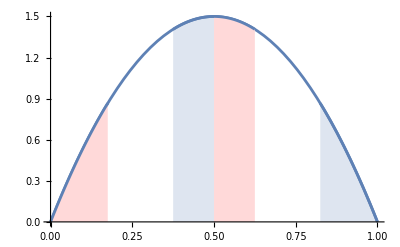

```mathematica
chat = 0.2;
pdf = PDF[BetaDistribution[2, 2], x];

plotlist = {Plot[pdf, {x, 0, 1},PlotRange->{{0,1}, {0, Automatic}}, AxesLabel->{"", ""}]};
plotlist = Append[plotlist, Plot[pdf, {x,ContributionUpperBoundary[2,2, chat],1}, Filling -> Axis, PlotRange->{{0,1}, {0, Automatic}}]];
plotlist = Append[plotlist, Plot[pdf, {x, 1/2,ContributionUpperMidBoundary[2,2,chat]}, Filling -> Axis, FillingStyle-> LightRed,PlotRange->{{0,1}, {0, Automatic}}]];

plotlist = Append[plotlist, Plot[pdf, {x, ContributionLowerMidBoundary[2,2,chat], 1/2}, Filling -> Axis,  PlotRange->{{0,1}, {0, Automatic}}]];
plotlist = Append[plotlist, Plot[pdf, {x, 0,ContributionLowerBoundary[2,2,chat]}, Filling -> Axis,FillingStyle -> LightRed, PlotRange->{{0,1}, {0, Automatic}}]];

Show[plotlist]
```

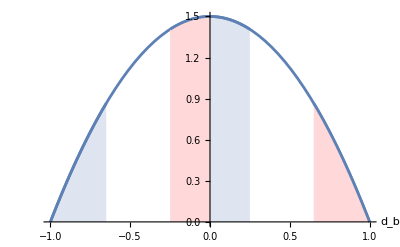

```mathematica
chat = 0.2;
pdf[x_] := PDF[BetaDistribution[2, 2], (1-x)/2];

plotlist = {Plot[pdf[x], {x, -1, 1},PlotRange->{{-1,1}, {0, Automatic}}, AxesLabel->{"d_b", ""}]};
plotlist = Append[plotlist, Plot[pdf[x], {x,-1, 1-2*ContributionUpperBoundary[2,2, chat]}, Filling -> Axis, PlotRange->{{-1,1}, {0, Automatic}}]];
plotlist = Append[plotlist, Plot[pdf[x], {x, 1-2*ContributionUpperMidBoundary[2,2,chat], 0}, Filling -> Axis, FillingStyle-> LightRed,PlotRange->{{-1,1}, {0, Automatic}}]];

plotlist = Append[plotlist, Plot[pdf[x], {x, 0,1-2*ContributionLowerMidBoundary[2,2,chat]}, Filling -> Axis,  PlotRange->{{-1,1}, {0, Automatic}}]];
plotlist = Append[plotlist, Plot[pdf[x], {x, 1-2*ContributionLowerBoundary[2,2,chat],1}, Filling -> Axis,FillingStyle -> LightRed, PlotRange->{{-1,1}, {0, Automatic}}]];

Show[plotlist]
```

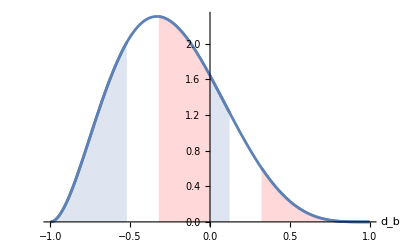

```mathematica
chat = 0.1;
alpha = 5;
beta = 3;
pdf[x_] := PDF[BetaDistribution[alpha, beta], (1-x)/2];

plotlist3 = {Plot[pdf[x], {x, -1, 1},PlotRange->{{-1,1}, {0, Automatic}}, AxesLabel->{"d_b", ""}]};
plotlist3 = Append[plotlist3, Plot[pdf[x], {x,-1, 1-2*ContributionUpperBoundary[alpha,beta, chat]}, Filling -> Axis, PlotRange->{{-1,1}, {0, Automatic}}]];
plotlist3 =Append[plotlist3, Plot[pdf[x], {x, 1-2*ContributionUpperMidBoundary[alpha,beta,chat], 0}, Filling -> Axis, FillingStyle-> LightRed,PlotRange->{{-1,1}, {0, Automatic}}]];

plotlist3 = Append[plotlist3, Plot[pdf[x], {x, 0,1-2*ContributionLowerMidBoundary[alpha,beta,chat]}, Filling -> Axis,  PlotRange->{{-1,1}, {0, Automatic}}]];
plotlist3= Append[plotlist3, Plot[pdf[x], {x, 1-2*ContributionLowerBoundary[alpha,beta,chat],1}, Filling -> Axis,FillingStyle -> LightRed, PlotRange->{{-1,1}, {0, Automatic}}]];

Show[plotlist3]
```

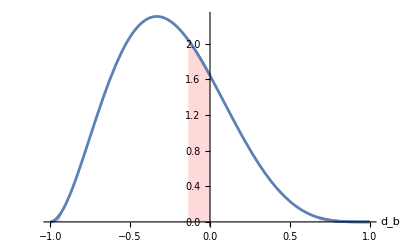

```mathematica
chat = 0.4;
alpha = 5;
beta = 3;
pdf[x_] := PDF[BetaDistribution[alpha, beta], (1-x)/2];

plotlist3 = {Plot[pdf[x], {x, -1, 1},PlotRange->{{-1,1}, {0, Automatic}}, AxesLabel->{"d_b", ""}]};
If[1-2*ContributionUpperBoundary[alpha,beta, chat] > -1, plotlist3 = Append[plotlist3, Plot[pdf[x], {x,-1, 1-2*ContributionUpperBoundary[alpha,beta, chat]}, Filling -> Axis, PlotRange->{{-1,1}, {0, Automatic}}]]];
If[1-2*ContributionUpperMidBoundary[alpha,beta,chat] < 0, plotlist3 =Append[plotlist3, Plot[pdf[x], {x, 1-2*ContributionUpperMidBoundary[alpha,beta,chat], 0}, Filling -> Axis, FillingStyle-> LightRed,PlotRange->{{-1,1}, {0, Automatic}}]]];

If[1-2*ContributionLowerMidBoundary[alpha,beta,chat]>0,plotlist3 = Append[plotlist3, Plot[pdf[x], {x, 0,1-2*ContributionLowerMidBoundary[alpha,beta,chat]}, Filling -> Axis,  PlotRange->{{-1,1}, {0, Automatic}}]]];
If[1-2*ContributionLowerBoundary[alpha,beta,chat]<1,plotlist3= Append[plotlist3, Plot[pdf[x], {x, 1-2*ContributionLowerBoundary[alpha,beta,chat],1}, Filling -> Axis,FillingStyle -> LightRed, PlotRange->{{-1,1}, {0, Automatic}}]]];

Show[plotlist3]
```

```mathematica
(* Contribution norm failure, unweighted by chat.*)
Illustration3 = Table[{Plot[PDF[BetaDistribution[2, total- 2], x], {x,0,1}],ListDensityPlot[Flatten[Table[ {a/total, chat, ContributionAreaFailure[a, total-a, chat]},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1}], 1],Frame -> False, Axes->True, AxesOrigin->{0.1,0},AxesLabel->{"", ""}, PlotRange->{{0.1,0.9}, {0,0.9}}, InterpolationOrder->0, PlotLegends ->None, ColorFunction->(bwFunc[Rescale[#,{0,0.8}]]&),ColorFunctionScaling->False]},  
{total, 4, 9}];
GraphicsRow[{GraphicsGrid[Partition[Flatten[Illustration3],4]], BarLegend[{bwFunc[Rescale[#,{0,0.8}]]&, {0,0.8}}]}]
```

-Graphics-

```mathematica
total =4;
N[Flatten[Table[ {a/total, chat, ContributionAreaFailure[a, total-a, chat]},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1}], 1]]
total =5;
N[Flatten[Table[ {a/total, chat, ContributionAreaFailure[a, total-a, chat]},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1}], 1]]
total =6;
N[Flatten[Table[ {a/total, chat, ContributionAreaFailure[a, total-a, chat]},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1}], 1]]
total =7;
N[Flatten[Table[ {a/total, chat, ContributionAreaFailure[a, total-a, chat]},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1}], 1]]
total =8;
N[Flatten[Table[ {a/total, chat, ContributionAreaFailure[a, total-a, chat]},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1}], 1]]
total =9;
N[Flatten[Table[ {a/total, chat, ContributionAreaFailure[a, total-a, chat]},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1}], 1]]
```

{{0.111111,0.1,0.54913},{0.111111,0.2,0.306609},{0.111111,0.3,0.281004},{0.111111,0.4,0.262345},{0.111111,0.5,0.245378},{0.111111,0.6,0.22971},{0.111111,0.7,0.215068},{0.111111,0.8,0.201316},{0.111111,0.9,0.188378},{0.138889,0.1,0.669231},{0.138889,0.2,0.325204},{0.138889,0.3,0.292304},{0.138889,0.4,0.270109},{0.138889,0.5,0.250053},{0.138889,0.6,0.231597},{0.138889,0.7,0.214361},{0.138889,0.8,0.198176},{0.138889,0.9,0.182962},{0.166667,0.1,0.711129},{0.166667,0.2,0.339755},{0.166667,0.3,0.298366},{0.166667,0.4,0.27268},{0.166667,0.5,0.249635},{0.166667,0.6,0.228511},{0.166667,0.7,0.208791},{0.166667,0.8,0.190269},{0.166667,0.9,0.172866},{0.194444,0.1,0.732578},{0.194444,0.2,0.351685},{0.194444,0.3,0.300418},{0.194444,0.4,0.271147},{0.194444,0.5,0.245158},{0.194444,0.6,0.221443},{0.194444,0.7,0.199299},{0.194444,0.8,0.178486},{0.194444,0.9,0.158931},{0.222222,0.1,0.744645},{0.222222,0.2,0.426554},{0.222222,0.3,0.302695},{0.222222,0.4,0.266129},{0.222222,0.5,0.237209},{0.222222,0.6,0.210954},{0.222222,0.7,0.186416},{0.222222,0.8,0.163325},{0.222222,0.9,0.141618},{0.25,0.1,0.751447},{0.25,0.2,0.474306},{0.25,0.3,0.303634},{0.25,0.4,0.258031},{0.25,0.5,0.22618},{0.25,0.6,0.197426},{0.25,0.7,0.170503},{0.25,0.8,0.145123},{0.25,0.9,0.121239},{0.277778,0.1,0.754996},{0.277778,0.2,0.499548},{0.277778,0.3,0.303741},{0.277778,0.4,0.247165},{0.277778,0.5,0.212381},{0.277778,0.6,0.181174},{0.277778,0.7,0.151867},{0.277778,0.8,0.124172},{0.277778,0.9,0.0980662},{0.305556,0.1,0.756459},{0.305556,0.2,0.513928},{0.305556,0.3,0.303427},{0.305556,0.4,0.233815},{0.305556,0.5,0.196113},{0.305556,0.6,0.162512},{0.305556,0.7,0.130823},{0.305556,0.8,0.10078},{0.305556,0.9,0.0723933},{0.333333,0.1,0.756598},{0.333333,0.2,0.522095},{0.333333,0.3,0.316442},{0.333333,0.4,0.218269},{0.333333,0.5,0.177702},{0.333333,0.6,0.141791},{0.333333,0.7,0.107724},{0.333333,0.8,0.0753014},{0.333333,0.9,0.044569},{0.361111,0.1,0.755955},{0.361111,0.2,0.526498},{0.361111,0.3,0.327502},{0.361111,0.4,0.209841},{0.361111,0.5,0.157517},{0.361111,0.6,0.119408},{0.361111,0.7,0.0829857},{0.361111,0.8,0.048157},{0.361111,0.9,0.015013},{0.388889,0.1,0.754932},{0.388889,0.2,0.528622},{0.388889,0.3,0.334088},{0.388889,0.4,0.20388},{0.388889,0.5,0.135988},{0.388889,0.6,0.0958173},{0.388889,0.7,0.0570836},{0.388889,0.8,0.0198377},{0.388889,0.9,0.},{0.416667,0.1,0.753836},{0.416667,0.2,0.529441},{0.416667,0.3,0.337793},{0.416667,0.4,0.198897},{0.416667,0.5,0.113617},{0.416667,0.6,0.0715238},{0.416667,0.7,0.0305534},{0.416667,0.8,0.},{0.416667,0.9,0.},{0.444444,0.1,0.752894},{0.444444,0.2,0.529607},{0.444444,0.3,0.339735},{0.444444,0.4,0.195841},{0.444444,0.5,0.0984724},{0.444444,0.6,0.047074},{0.444444,0.7,0.00397952},{0.444444,0.8,0.},{0.444444,0.9,0.},{0.472222,0.1,0.752267},{0.472222,0.2,0.529547},{0.472222,0.3,0.340634},{0.472222,0.4,0.19497},{0.472222,0.5,0.0948484},{0.472222,0.6,0.0230397},{0.472222,0.7,0.},{0.472222,0.8,0.},{0.472222,0.9,0.},{0.5,0.1,0.752047},{0.5,0.2,0.5295},{0.5,0.3,0.340891},{0.5,0.4,0.19475},{0.5,0.5,0.0936279},{0.5,0.6,1.77636×10^-15},{0.5,0.7,0.},{0.5,0.8,0.},{0.5,0.9,0.},{0.527778,0.1,0.752267},{0.527778,0.2,0.529547},{0.527778,0.3,0.340634},{0.527778,0.4,0.19497},{0.527778,0.5,0.0948484},{0.527778,0.6,0.0230397},{0.527778,0.7,0.},{0.527778,0.8,0.},{0.527778,0.9,0.},{0.555556,0.1,0.752894},{0.555556,0.2,0.529607},{0.555556,0.3,0.339735},{0.555556,0.4,0.195841},{0.555556,0.5,0.0984724},{0.555556,0.6,0.047074},{0.555556,0.7,0.00397952},{0.555556,0.8,0.},{0.555556,0.9,0.},{0.583333,0.1,0.753836},{0.583333,0.2,0.529441},{0.583333,0.3,0.337793},{0.583333,0.4,0.198897},{0.583333,0.5,0.113617},{0.583333,0.6,0.0715238},{0.583333,0.7,0.0305534},{0.583333,0.8,0.},{0.583333,0.9,0.},{0.611111,0.1,0.754932},{0.611111,0.2,0.528622},{0.611111,0.3,0.334088},{0.611111,0.4,0.20388},{0.611111,0.5,0.135988},{0.611111,0.6,0.0958173},{0.611111,0.7,0.0570836},{0.611111,0.8,0.0198377},{0.611111,0.9,0.},{0.638889,0.1,0.755955},{0.638889,0.2,0.526498},{0.638889,0.3,0.327502},{0.638889,0.4,0.209841},{0.638889,0.5,0.157517},{0.638889,0.6,0.119408},{0.638889,0.7,0.0829857},{0.638889,0.8,0.048157},{0.638889,0.9,0.015013},{0.666667,0.1,0.756598},{0.666667,0.2,0.522095},{0.666667,0.3,0.316442},{0.666667,0.4,0.218269},{0.666667,0.5,0.177702},{0.666667,0.6,0.141791},{0.666667,0.7,0.107724},{0.666667,0.8,0.0753013},{0.666667,0.9,0.044569},{0.694444,0.1,0.756459},{0.694444,0.2,0.513928},{0.694444,0.3,0.303427},{0.694444,0.4,0.233815},{0.694444,0.5,0.196113},{0.694444,0.6,0.162512},{0.694444,0.7,0.130823},{0.694444,0.8,0.10078},{0.694444,0.9,0.0723933},{0.722222,0.1,0.754996},{0.722222,0.2,0.499548},{0.722222,0.3,0.303741},{0.722222,0.4,0.247165},{0.722222,0.5,0.212381},{0.722222,0.6,0.181174},{0.722222,0.7,0.151867},{0.722222,0.8,0.124172},{0.722222,0.9,0.0980662},{0.75,0.1,0.751447},{0.75,0.2,0.474306},{0.75,0.3,0.303634},{0.75,0.4,0.258031},{0.75,0.5,0.22618},{0.75,0.6,0.197426},{0.75,0.7,0.170503},{0.75,0.8,0.145123},{0.75,0.9,0.121239},{0.777778,0.1,0.744645},{0.777778,0.2,0.426554},{0.777778,0.3,0.302695},{0.777778,0.4,0.266129},{0.777778,0.5,0.237209},{0.777778,0.6,0.210954},{0.777778,0.7,0.186416},{0.777778,0.8,0.163325},{0.777778,0.9,0.141619},{0.805556,0.1,0.732578},{0.805556,0.2,0.351685},{0.805556,0.3,0.300418},{0.805556,0.4,0.271147},{0.805556,0.5,0.245158},{0.805556,0.6,0.221443},{0.805556,0.7,0.199299},{0.805556,0.8,0.178486},{0.805556,0.9,0.158931},{0.833333,0.1,0.711129},{0.833333,0.2,0.339755},{0.833333,0.3,0.298366},{0.833333,0.4,0.27268},{0.833333,0.5,0.249635},{0.833333,0.6,0.228511},{0.833333,0.7,0.208791},{0.833333,0.8,0.190269},{0.833333,0.9,0.172866},{0.861111,0.1,0.669231},{0.861111,0.2,0.325204},{0.861111,0.3,0.292304},{0.861111,0.4,0.270109},{0.861111,0.5,0.250053},{0.861111,0.6,0.231597},{0.861111,0.7,0.214361},{0.861111,0.8,0.198176},{0.861111,0.9,0.182962},{0.888889,0.1,0.54913},{0.888889,0.2,0.306609},{0.888889,0.3,0.281004},{0.888889,0.4,0.262345},{0.888889,0.5,0.245378},{0.888889,0.6,0.22971},{0.888889,0.7,0.215068},{0.888889,0.8,0.201316},{0.888889,0.9,0.188378}}

{{0.111111,0.1,0.558617},{0.111111,0.2,0.310762},{0.111111,0.3,0.28668},{0.111111,0.4,0.265693},{0.111111,0.5,0.246433},{0.111111,0.6,0.228594},{0.111111,0.7,0.21198},{0.111111,0.8,0.196472},{0.111111,0.9,0.181981},{0.133333,0.1,0.64446},{0.133333,0.2,0.322997},{0.133333,0.3,0.294342},{0.133333,0.4,0.270343},{0.133333,0.5,0.248397},{0.133333,0.6,0.228112},{0.133333,0.7,0.209247},{0.133333,0.8,0.191667},{0.133333,0.9,0.175277},{0.155556,0.1,0.684077},{0.155556,0.2,0.332538},{0.155556,0.3,0.298743},{0.155556,0.4,0.271793},{0.155556,0.5,0.247245},{0.155556,0.6,0.224605},{0.155556,0.7,0.203576},{0.155556,0.8,0.184006},{0.155556,0.9,0.165799},{0.177778,0.1,0.706959},{0.177778,0.2,0.3402},{0.177778,0.3,0.300502},{0.177778,0.4,0.270613},{0.177778,0.5,0.243506},{0.177778,0.6,0.218563},{0.177778,0.7,0.195417},{0.177778,0.8,0.173901},{0.177778,0.9,0.153921},{0.2,0.1,0.721192},{0.2,0.2,0.378141},{0.2,0.3,0.299973},{0.2,0.4,0.267119},{0.2,0.5,0.237466},{0.2,0.6,0.210245},{0.2,0.7,0.185001},{0.2,0.8,0.161555},{0.2,0.9,0.139814},{0.222222,0.1,0.730171},{0.222222,0.2,0.428074},{0.222222,0.3,0.297368},{0.222222,0.4,0.261498},{0.222222,0.5,0.22929},{0.222222,0.6,0.199797},{0.222222,0.7,0.172454},{0.222222,0.8,0.147067},{0.222222,0.9,0.123556},{0.244444,0.1,0.735656},{0.244444,0.2,0.456935},{0.244444,0.3,0.292832},{0.244444,0.4,0.253872},{0.244444,0.5,0.219087},{0.244444,0.6,0.187315},{0.244444,0.7,0.157855},{0.244444,0.8,0.130499},{0.244444,0.9,0.105183},{0.266667,0.1,0.738698},{0.266667,0.2,0.474753},{0.266667,0.3,0.286477},{0.266667,0.4,0.24434},{0.266667,0.5,0.206949},{0.266667,0.6,0.172886},{0.266667,0.7,0.141277},{0.266667,0.8,0.111907},{0.266667,0.9,0.0847378},{0.288889,0.1,0.739994},{0.288889,0.2,0.485741},{0.288889,0.3,0.279367},{0.288889,0.4,0.233003},{0.288889,0.5,0.192975},{0.288889,0.6,0.156608},{0.288889,0.7,0.122812},{0.288889,0.8,0.0913728},{0.288889,0.9,0.0622823},{0.311111,0.1,0.740048},{0.311111,0.2,0.492207},{0.311111,0.3,0.286372},{0.311111,0.4,0.219978},{0.311111,0.5,0.17729},{0.311111,0.6,0.138611},{0.311111,0.7,0.102585},{0.311111,0.8,0.0690114},{0.311111,0.9,0.0379205},{0.333333,0.1,0.739249},{0.333333,0.2,0.495606},{0.333333,0.3,0.292022},{0.333333,0.4,0.205408},{0.333333,0.5,0.160052},{0.333333,0.6,0.119065},{0.333333,0.7,0.0807673},{0.333333,0.8,0.0449879},{0.333333,0.9,0.0118062},{0.355556,0.1,0.737911},{0.355556,0.2,0.496941},{0.355556,0.3,0.295218},{0.355556,0.4,0.189467},{0.355556,0.5,0.141459},{0.355556,0.6,0.0981857},{0.355556,0.7,0.0575779},{0.355556,0.8,0.0195206},{0.355556,0.9,0.},{0.377778,0.1,0.736294},{0.377778,0.2,0.496949},{0.377778,0.3,0.296545},{0.377778,0.4,0.17236},{0.377778,0.5,0.121752},{0.377778,0.6,0.076235},{0.377778,0.7,0.0332898},{0.377778,0.8,0.},{0.377778,0.9,0.},{0.4,0.1,0.734615},{0.4,0.2,0.49619},{0.4,0.3,0.296652},{0.4,0.4,0.154635},{0.4,0.5,0.101213},{0.4,0.6,0.0535215},{0.4,0.7,0.00822612},{0.4,0.8,0.},{0.4,0.9,0.},{0.422222,0.1,0.733055},{0.422222,0.2,0.495098},{0.422222,0.3,0.296093},{0.422222,0.4,0.143981},{0.422222,0.5,0.0801626},{0.422222,0.6,0.0303947},{0.422222,0.7,0.},{0.422222,0.8,0.},{0.422222,0.9,0.},{0.444444,0.1,0.731757},{0.444444,0.2,0.494001},{0.444444,0.3,0.295302},{0.444444,0.4,0.140732},{0.444444,0.5,0.0589592},{0.444444,0.6,0.00723734},{0.444444,0.7,0.},{0.444444,0.8,0.},{0.444444,0.9,0.},{0.466667,0.1,0.730831},{0.466667,0.2,0.493139},{0.466667,0.3,0.2946},{0.466667,0.4,0.138593},{0.466667,0.5,0.0379933},{0.466667,0.6,0.},{0.466667,0.7,0.},{0.466667,0.8,0.},{0.466667,0.9,0.},{0.488889,0.1,0.73035},{0.488889,0.2,0.49267},{0.488889,0.3,0.294197},{0.488889,0.4,0.13752},{0.488889,0.5,0.0176817},{0.488889,0.6,0.},{0.488889,0.7,0.},{0.488889,0.8,0.},{0.488889,0.9,0.},{0.511111,0.1,0.73035},{0.511111,0.2,0.49267},{0.511111,0.3,0.294197},{0.511111,0.4,0.13752},{0.511111,0.5,0.0176817},{0.511111,0.6,0.},{0.511111,0.7,0.},{0.511111,0.8,0.},{0.511111,0.9,0.},{0.533333,0.1,0.730831},{0.533333,0.2,0.493139},{0.533333,0.3,0.2946},{0.533333,0.4,0.138593},{0.533333,0.5,0.0379933},{0.533333,0.6,0.},{0.533333,0.7,0.},{0.533333,0.8,0.},{0.533333,0.9,0.},{0.555556,0.1,0.731757},{0.555556,0.2,0.494001},{0.555556,0.3,0.295302},{0.555556,0.4,0.140732},{0.555556,0.5,0.0589592},{0.555556,0.6,0.00723733},{0.555556,0.7,0.},{0.555556,0.8,0.},{0.555556,0.9,0.},{0.577778,0.1,0.733055},{0.577778,0.2,0.495098},{0.577778,0.3,0.296093},{0.577778,0.4,0.143981},{0.577778,0.5,0.0801626},{0.577778,0.6,0.0303947},{0.577778,0.7,0.},{0.577778,0.8,0.},{0.577778,0.9,0.},{0.6,0.1,0.734615},{0.6,0.2,0.49619},{0.6,0.3,0.296652},{0.6,0.4,0.154635},{0.6,0.5,0.101213},{0.6,0.6,0.0535215},{0.6,0.7,0.00822612},{0.6,0.8,0.},{0.6,0.9,0.},{0.622222,0.1,0.736294},{0.622222,0.2,0.496949},{0.622222,0.3,0.296545},{0.622222,0.4,0.17236},{0.622222,0.5,0.121752},{0.622222,0.6,0.076235},{0.622222,0.7,0.0332898},{0.622222,0.8,0.},{0.622222,0.9,0.},{0.644444,0.1,0.737911},{0.644444,0.2,0.496941},{0.644444,0.3,0.295218},{0.644444,0.4,0.189467},{0.644444,0.5,0.141459},{0.644444,0.6,0.0981857},{0.644444,0.7,0.0575779},{0.644444,0.8,0.0195206},{0.644444,0.9,0.},{0.666667,0.1,0.739249},{0.666667,0.2,0.495606},{0.666667,0.3,0.292022},{0.666667,0.4,0.205408},{0.666667,0.5,0.160052},{0.666667,0.6,0.119065},{0.666667,0.7,0.0807673},{0.666667,0.8,0.0449879},{0.666667,0.9,0.0118062},{0.688889,0.1,0.740048},{0.688889,0.2,0.492207},{0.688889,0.3,0.286372},{0.688889,0.4,0.219978},{0.688889,0.5,0.17729},{0.688889,0.6,0.138611},{0.688889,0.7,0.102585},{0.688889,0.8,0.0690114},{0.688889,0.9,0.0379205},{0.711111,0.1,0.739994},{0.711111,0.2,0.485741},{0.711111,0.3,0.279367},{0.711111,0.4,0.233003},{0.711111,0.5,0.192975},{0.711111,0.6,0.156608},{0.711111,0.7,0.122812},{0.711111,0.8,0.0913728},{0.711111,0.9,0.0622823},{0.733333,0.1,0.738698},{0.733333,0.2,0.474753},{0.733333,0.3,0.286477},{0.733333,0.4,0.24434},{0.733333,0.5,0.206949},{0.733333,0.6,0.172886},{0.733333,0.7,0.141277},{0.733333,0.8,0.111907},{0.733333,0.9,0.0847378},{0.755556,0.1,0.735656},{0.755556,0.2,0.456935},{0.755556,0.3,0.292832},{0.755556,0.4,0.253872},{0.755556,0.5,0.219087},{0.755556,0.6,0.187315},{0.755556,0.7,0.157855},{0.755556,0.8,0.130499},{0.755556,0.9,0.105183},{0.777778,0.1,0.730171},{0.777778,0.2,0.428074},{0.777778,0.3,0.297368},{0.777778,0.4,0.261498},{0.777778,0.5,0.22929},{0.777778,0.6,0.199797},{0.777778,0.7,0.172454},{0.777778,0.8,0.147067},{0.777778,0.9,0.123556},{0.8,0.1,0.721192},{0.8,0.2,0.378141},{0.8,0.3,0.299973},{0.8,0.4,0.267119},{0.8,0.5,0.237466},{0.8,0.6,0.210245},{0.8,0.7,0.185001},{0.8,0.8,0.161555},{0.8,0.9,0.139814},{0.822222,0.1,0.706959},{0.822222,0.2,0.3402},{0.822222,0.3,0.300502},{0.822222,0.4,0.270613},{0.822222,0.5,0.243506},{0.822222,0.6,0.218563},{0.822222,0.7,0.195417},{0.822222,0.8,0.173901},{0.822222,0.9,0.153921},{0.844444,0.1,0.684077},{0.844444,0.2,0.332538},{0.844444,0.3,0.298743},{0.844444,0.4,0.271793},{0.844444,0.5,0.247245},{0.844444,0.6,0.224605},{0.844444,0.7,0.203576},{0.844444,0.8,0.184006},{0.844444,0.9,0.165799},{0.866667,0.1,0.64446},{0.866667,0.2,0.322997},{0.866667,0.3,0.294342},{0.866667,0.4,0.270343},{0.866667,0.5,0.248397},{0.866667,0.6,0.228112},{0.866667,0.7,0.209247},{0.866667,0.8,0.191667},{0.866667,0.9,0.175277},{0.888889,0.1,0.558617},{0.888889,0.2,0.310762},{0.888889,0.3,0.28668},{0.888889,0.4,0.265693},{0.888889,0.5,0.246433},{0.888889,0.6,0.228594},{0.888889,0.7,0.21198},{0.888889,0.8,0.196472},{0.888889,0.9,0.181981}}

{{0.111111,0.1,0.550056},{0.111111,0.2,0.314721},{0.111111,0.3,0.289333},{0.111111,0.4,0.266188},{0.111111,0.5,0.244903},{0.111111,0.6,0.225228},{0.111111,0.7,0.206997},{0.111111,0.8,0.190087},{0.111111,0.9,0.174395},{0.12963,0.1,0.62007},{0.12963,0.2,0.322932},{0.12963,0.3,0.294535},{0.12963,0.4,0.268739},{0.12963,0.5,0.245077},{0.12963,0.6,0.223248},{0.12963,0.7,0.203065},{0.12963,0.8,0.184394},{0.12963,0.9,0.167126},{0.148148,0.1,0.657995},{0.148148,0.2,0.328972},{0.148148,0.3,0.297605},{0.148148,0.4,0.269223},{0.148148,0.5,0.243257},{0.148148,0.6,0.219353},{0.148148,0.7,0.197295},{0.148148,0.8,0.176943},{0.148148,0.9,0.158182},{0.166667,0.1,0.681908},{0.166667,0.2,0.333251},{0.166667,0.3,0.298909},{0.166667,0.4,0.267968},{0.166667,0.5,0.239743},{0.166667,0.6,0.21381},{0.166667,0.7,0.189926},{0.166667,0.8,0.167943},{0.166667,0.9,0.147743},{0.185185,0.1,0.697931},{0.185185,0.2,0.342522},{0.185185,0.3,0.298655},{0.185185,0.4,0.265153},{0.185185,0.5,0.234688},{0.185185,0.6,0.206752},{0.185185,0.7,0.181066},{0.185185,0.8,0.157477},{0.185185,0.9,0.135869},{0.203704,0.1,0.708885},{0.203704,0.2,0.388464},{0.203704,0.3,0.296958},{0.203704,0.4,0.260873},{0.203704,0.5,0.228167},{0.203704,0.6,0.198233},{0.203704,0.7,0.17075},{0.203704,0.8,0.145561},{0.203704,0.9,0.122553},{0.222222,0.1,0.716306},{0.222222,0.2,0.418628},{0.222222,0.3,0.293884},{0.222222,0.4,0.255172},{0.222222,0.5,0.220208},{0.222222,0.6,0.188266},{0.222222,0.7,0.158974},{0.222222,0.8,0.132173},{0.222222,0.9,0.107757},{0.240741,0.1,0.721131},{0.240741,0.2,0.438861},{0.240741,0.3,0.289468},{0.240741,0.4,0.248071},{0.240741,0.5,0.21082},{0.240741,0.6,0.176849},{0.240741,0.7,0.145721},{0.240741,0.8,0.117279},{0.240741,0.9,0.091429},{0.259259,0.1,0.723989},{0.259259,0.2,0.452413},{0.259259,0.3,0.283737},{0.259259,0.4,0.239584},{0.259259,0.5,0.200007},{0.259259,0.6,0.163975},{0.259259,0.7,0.130973},{0.259259,0.8,0.100847},{0.259259,0.9,0.0735224},{0.277778,0.1,0.725332},{0.277778,0.2,0.461214},{0.277778,0.3,0.27847},{0.277778,0.4,0.229728},{0.277778,0.5,0.187783},{0.277778,0.6,0.149652},{0.277778,0.7,0.114727},{0.277778,0.8,0.0828623},{0.277778,0.9,0.0540065},{0.296296,0.1,0.725509},{0.296296,0.2,0.466533},{0.296296,0.3,0.2779},{0.296296,0.4,0.218537},{0.296296,0.5,0.174178},{0.296296,0.6,0.133907},{0.296296,0.7,0.0970014},{0.296296,0.8,0.0633311},{0.296296,0.9,0.0328753},{0.314815,0.1,0.724804},{0.314815,0.2,0.469274},{0.314815,0.3,0.275759},{0.314815,0.4,0.206062},{0.314815,0.5,0.159246},{0.314815,0.6,0.116794},{0.314815,0.7,0.0778457},{0.314815,0.8,0.0422926},{0.314815,0.9,0.0101551},{0.333333,0.1,0.723459},{0.333333,0.2,0.470122},{0.333333,0.3,0.270966},{0.333333,0.4,0.192381},{0.333333,0.5,0.143071},{0.333333,0.6,0.0984007},{0.333333,0.7,0.0573429},{0.333333,0.8,0.0198222},{0.333333,0.9,0.},{0.351852,0.1,0.721682},{0.351852,0.2,0.469619},{0.351852,0.3,0.263538},{0.351852,0.4,0.177596},{0.351852,0.5,0.125768},{0.351852,0.6,0.0788495},{0.351852,0.7,0.0356147},{0.351852,0.8,0.},{0.351852,0.9,0.},{0.37037,0.1,0.71966},{0.37037,0.2,0.468211},{0.37037,0.3,0.261162},{0.37037,0.4,0.161908},{0.37037,0.5,0.107485},{0.37037,0.6,0.0583004},{0.37037,0.7,0.0128226},{0.37037,0.8,0.},{0.37037,0.9,0.},{0.388889,0.1,0.717558},{0.388889,0.2,0.466269},{0.388889,0.3,0.258741},{0.388889,0.4,0.146092},{0.388889,0.5,0.0884043},{0.388889,0.6,0.0369498},{0.388889,0.7,0.},{0.388889,0.8,0.},{0.388889,0.9,0.},{0.407407,0.1,0.715522},{0.407407,0.2,0.464108},{0.407407,0.3,0.256088},{0.407407,0.4,0.129946},{0.407407,0.5,0.0687369},{0.407407,0.6,0.0150292},{0.407407,0.7,0.},{0.407407,0.8,0.},{0.407407,0.9,0.},{0.425926,0.1,0.713677},{0.425926,0.2,0.461986},{0.425926,0.3,0.253499},{0.425926,0.4,0.11331},{0.425926,0.5,0.0487236},{0.425926,0.6,0.},{0.425926,0.7,0.},{0.425926,0.8,0.},{0.425926,0.9,0.},{0.444444,0.1,0.71213},{0.444444,0.2,0.460116},{0.444444,0.3,0.251221},{0.444444,0.4,0.096255},{0.444444,0.5,0.0286288},{0.444444,0.6,0.},{0.444444,0.7,0.},{0.444444,0.8,0.},{0.444444,0.9,0.},{0.462963,0.1,0.710963},{0.462963,0.2,0.458662},{0.462963,0.3,0.249453},{0.462963,0.4,0.0823383},{0.462963,0.5,0.00873628},{0.462963,0.6,0.},{0.462963,0.7,0.},{0.462963,0.8,0.},{0.462963,0.9,0.},{0.481481,0.1,0.710239},{0.481481,0.2,0.457743},{0.481481,0.3,0.248335},{0.481481,0.4,0.0803698},{0.481481,0.5,0.0000987719},{0.481481,0.6,0.},{0.481481,0.7,0.},{0.481481,0.8,0.},{0.481481,0.9,0.},{0.5,0.1,0.709993},{0.5,0.2,0.457428},{0.5,0.3,0.247952},{0.5,0.4,0.0797092},{0.5,0.5,0.000074517},{0.5,0.6,0.},{0.5,0.7,0.},{0.5,0.8,0.},{0.5,0.9,0.},{0.518519,0.1,0.710239},{0.518519,0.2,0.457743},{0.518519,0.3,0.248335},{0.518519,0.4,0.0803698},{0.518519,0.5,0.0000987719},{0.518519,0.6,0.},{0.518519,0.7,0.},{0.518519,0.8,0.},{0.518519,0.9,0.},{0.537037,0.1,0.710963},{0.537037,0.2,0.458662},{0.537037,0.3,0.249453},{0.537037,0.4,0.0823383},{0.537037,0.5,0.00873628},{0.537037,0.6,0.},{0.537037,0.7,0.},{0.537037,0.8,0.},{0.537037,0.9,0.},{0.555556,0.1,0.71213},{0.555556,0.2,0.460116},{0.555556,0.3,0.251221},{0.555556,0.4,0.096255},{0.555556,0.5,0.0286288},{0.555556,0.6,0.},{0.555556,0.7,0.},{0.555556,0.8,0.},{0.555556,0.9,0.},{0.574074,0.1,0.713677},{0.574074,0.2,0.461986},{0.574074,0.3,0.253499},{0.574074,0.4,0.11331},{0.574074,0.5,0.0487236},{0.574074,0.6,0.},{0.574074,0.7,0.},{0.574074,0.8,0.},{0.574074,0.9,0.},{0.592593,0.1,0.715522},{0.592593,0.2,0.464108},{0.592593,0.3,0.256088},{0.592593,0.4,0.129946},{0.592593,0.5,0.0687369},{0.592593,0.6,0.0150292},{0.592593,0.7,0.},{0.592593,0.8,0.},{0.592593,0.9,0.},{0.611111,0.1,0.717558},{0.611111,0.2,0.466269},{0.611111,0.3,0.258741},{0.611111,0.4,0.146092},{0.611111,0.5,0.0884043},{0.611111,0.6,0.0369498},{0.611111,0.7,0.},{0.611111,0.8,0.},{0.611111,0.9,0.},{0.62963,0.1,0.71966},{0.62963,0.2,0.468211},{0.62963,0.3,0.261162},{0.62963,0.4,0.161908},{0.62963,0.5,0.107485},{0.62963,0.6,0.0583004},{0.62963,0.7,0.0128226},{0.62963,0.8,0.},{0.62963,0.9,0.},{0.648148,0.1,0.721682},{0.648148,0.2,0.469619},{0.648148,0.3,0.263538},{0.648148,0.4,0.177596},{0.648148,0.5,0.125768},{0.648148,0.6,0.0788495},{0.648148,0.7,0.0356146},{0.648148,0.8,0.},{0.648148,0.9,0.},{0.666667,0.1,0.723459},{0.666667,0.2,0.470122},{0.666667,0.3,0.270966},{0.666667,0.4,0.192381},{0.666667,0.5,0.143071},{0.666667,0.6,0.0984007},{0.666667,0.7,0.0573429},{0.666667,0.8,0.0198222},{0.666667,0.9,0.},{0.685185,0.1,0.724804},{0.685185,0.2,0.469274},{0.685185,0.3,0.275759},{0.685185,0.4,0.206062},{0.685185,0.5,0.159246},{0.685185,0.6,0.116794},{0.685185,0.7,0.0778457},{0.685185,0.8,0.0422926},{0.685185,0.9,0.0101552},{0.703704,0.1,0.725509},{0.703704,0.2,0.466533},{0.703704,0.3,0.2779},{0.703704,0.4,0.218537},{0.703704,0.5,0.174178},{0.703704,0.6,0.133907},{0.703704,0.7,0.0970014},{0.703704,0.8,0.0633311},{0.703704,0.9,0.0328753},{0.722222,0.1,0.725332},{0.722222,0.2,0.461214},{0.722222,0.3,0.27847},{0.722222,0.4,0.229728},{0.722222,0.5,0.187783},{0.722222,0.6,0.149652},{0.722222,0.7,0.114727},{0.722222,0.8,0.0828623},{0.722222,0.9,0.0540065},{0.740741,0.1,0.723989},{0.740741,0.2,0.452413},{0.740741,0.3,0.283737},{0.740741,0.4,0.239584},{0.740741,0.5,0.200007},{0.740741,0.6,0.163975},{0.740741,0.7,0.130973},{0.740741,0.8,0.100847},{0.740741,0.9,0.0735224},{0.759259,0.1,0.721131},{0.759259,0.2,0.438861},{0.759259,0.3,0.289468},{0.759259,0.4,0.248071},{0.759259,0.5,0.21082},{0.759259,0.6,0.176849},{0.759259,0.7,0.145721},{0.759259,0.8,0.117279},{0.759259,0.9,0.091429},{0.777778,0.1,0.716306},{0.777778,0.2,0.418628},{0.777778,0.3,0.293884},{0.777778,0.4,0.255172},{0.777778,0.5,0.220208},{0.777778,0.6,0.188266},{0.777778,0.7,0.158974},{0.777778,0.8,0.132173},{0.777778,0.9,0.107757},{0.796296,0.1,0.708885},{0.796296,0.2,0.388464},{0.796296,0.3,0.296958},{0.796296,0.4,0.260873},{0.796296,0.5,0.228167},{0.796296,0.6,0.198233},{0.796296,0.7,0.17075},{0.796296,0.8,0.145561},{0.796296,0.9,0.122553},{0.814815,0.1,0.697931},{0.814815,0.2,0.342522},{0.814815,0.3,0.298655},{0.814815,0.4,0.265153},{0.814815,0.5,0.234688},{0.814815,0.6,0.206752},{0.814815,0.7,0.181066},{0.814815,0.8,0.157477},{0.814815,0.9,0.135869},{0.833333,0.1,0.681908},{0.833333,0.2,0.333251},{0.833333,0.3,0.298909},{0.833333,0.4,0.267968},{0.833333,0.5,0.239743},{0.833333,0.6,0.21381},{0.833333,0.7,0.189926},{0.833333,0.8,0.167943},{0.833333,0.9,0.147743},{0.851852,0.1,0.657995},{0.851852,0.2,0.328972},{0.851852,0.3,0.297605},{0.851852,0.4,0.269223},{0.851852,0.5,0.243257},{0.851852,0.6,0.219353},{0.851852,0.7,0.197295},{0.851852,0.8,0.176943},{0.851852,0.9,0.158182},{0.87037,0.1,0.62007},{0.87037,0.2,0.322932},{0.87037,0.3,0.294535},{0.87037,0.4,0.268739},{0.87037,0.5,0.245077},{0.87037,0.6,0.223248},{0.87037,0.7,0.203065},{0.87037,0.8,0.184394},{0.87037,0.9,0.167126},{0.888889,0.1,0.550056},{0.888889,0.2,0.314721},{0.888889,0.3,0.289333},{0.888889,0.4,0.266188},{0.888889,0.5,0.244903},{0.888889,0.6,0.225228},{0.888889,0.7,0.206997},{0.888889,0.8,0.190087},{0.888889,0.9,0.174395}}

{{0.111111,0.1,0.536562},{0.111111,0.2,0.317751},{0.111111,0.3,0.290248},{0.111111,0.4,0.265119},{0.111111,0.5,0.242038},{0.111111,0.6,0.220785},{0.111111,0.7,0.201199},{0.111111,0.8,0.183148},{0.111111,0.9,0.166514},{0.126984,0.1,0.596706},{0.126984,0.2,0.323886},{0.126984,0.3,0.293698},{0.126984,0.4,0.26619},{0.126984,0.5,0.24098},{0.126984,0.6,0.217822},{0.126984,0.7,0.196539},{0.126984,0.8,0.176992},{0.126984,0.9,0.159054},{0.142857,0.1,0.633032},{0.142857,0.2,0.328522},{0.142857,0.3,0.295698},{0.142857,0.4,0.265874},{0.142857,0.5,0.238604},{0.142857,0.6,0.213612},{0.142857,0.7,0.190707},{0.142857,0.8,0.169743},{0.142857,0.9,0.150584},{0.15873,0.1,0.657519},{0.15873,0.2,0.331928},{0.15873,0.3,0.296483},{0.15873,0.4,0.264378},{0.15873,0.5,0.235094},{0.15873,0.6,0.208315},{0.15873,0.7,0.183841},{0.15873,0.8,0.161515},{0.15873,0.9,0.141198},{0.174603,0.1,0.674882},{0.174603,0.2,0.334264},{0.174603,0.3,0.296187},{0.174603,0.4,0.261815},{0.174603,0.5,0.230542},{0.174603,0.6,0.202008},{0.174603,0.7,0.175995},{0.174603,0.8,0.152346},{0.174603,0.9,0.130914},{0.190476,0.1,0.687466},{0.190476,0.2,0.359805},{0.190476,0.3,0.294884},{0.190476,0.4,0.258241},{0.190476,0.5,0.224986},{0.190476,0.6,0.194709},{0.190476,0.7,0.167175},{0.190476,0.8,0.142222},{0.190476,0.9,0.119702},{0.206349,0.1,0.696604},{0.206349,0.2,0.387548},{0.206349,0.3,0.292607},{0.206349,0.4,0.253671},{0.206349,0.5,0.218429},{0.206349,0.6,0.186407},{0.206349,0.7,0.157352},{0.206349,0.8,0.131101},{0.206349,0.9,0.107505},{0.222222,0.1,0.703129},{0.222222,0.2,0.407457},{0.222222,0.3,0.289364},{0.222222,0.4,0.248099},{0.222222,0.5,0.210851},{0.222222,0.6,0.177071},{0.222222,0.7,0.146482},{0.222222,0.8,0.118925},{0.222222,0.9,0.0942498},{0.238095,0.1,0.707606},{0.238095,0.2,0.421622},{0.238095,0.3,0.285149},{0.238095,0.4,0.241507},{0.238095,0.5,0.202223},{0.238095,0.6,0.166659},{0.238095,0.7,0.134512},{0.238095,0.8,0.105626},{0.238095,0.9,0.0798571},{0.253968,0.1,0.710438},{0.253968,0.2,0.432365},{0.253968,0.3,0.279952},{0.253968,0.4,0.233874},{0.253968,0.5,0.192515},{0.253968,0.6,0.155133},{0.253968,0.7,0.121391},{0.253968,0.8,0.0911418},{0.253968,0.9,0.0642503},{0.269841,0.1,0.711935},{0.269841,0.2,0.439621},{0.269841,0.3,0.275444},{0.269841,0.4,0.225181},{0.269841,0.5,0.181702},{0.269841,0.6,0.142458},{0.269841,0.7,0.107075},{0.269841,0.8,0.0754163},{0.269841,0.9,0.0473615},{0.285714,0.1,0.712345},{0.285714,0.2,0.444119},{0.285714,0.3,0.273765},{0.285714,0.4,0.21542},{0.285714,0.5,0.169769},{0.285714,0.6,0.128614},{0.285714,0.7,0.0915331},{0.285714,0.8,0.0584079},{0.285714,0.9,0.0291373},{0.301587,0.1,0.711877},{0.301587,0.2,0.446428},{0.301587,0.3,0.271423},{0.301587,0.4,0.204594},{0.301587,0.5,0.156717},{0.301587,0.6,0.113596},{0.301587,0.7,0.0747536},{0.301587,0.8,0.0400941},{0.301587,0.9,0.00954338},{0.31746,0.1,0.710716},{0.31746,0.2,0.447016},{0.31746,0.3,0.267416},{0.31746,0.4,0.192725},{0.31746,0.5,0.142567},{0.31746,0.6,0.0974231},{0.31746,0.7,0.056747},{0.31746,0.8,0.0204756},{0.31746,0.9,0.},{0.333333,0.1,0.709027},{0.333333,0.2,0.446274},{0.333333,0.3,0.2615},{0.333333,0.4,0.179853},{0.333333,0.5,0.127362},{0.333333,0.6,0.0801361},{0.333333,0.7,0.0375498},{0.333333,0.8,0.},{0.333333,0.9,0.},{0.349206,0.1,0.706962},{0.349206,0.2,0.444544},{0.349206,0.3,0.253695},{0.349206,0.4,0.166044},{0.349206,0.5,0.11117},{0.349206,0.6,0.0618049},{0.349206,0.7,0.017227},{0.349206,0.8,0.},{0.349206,0.9,0.},{0.365079,0.1,0.70466},{0.365079,0.2,0.442125},{0.365079,0.3,0.244141},{0.365079,0.4,0.151706},{0.365079,0.5,0.0940831},{0.365079,0.6,0.0425271},{0.365079,0.7,0.},{0.365079,0.8,0.},{0.365079,0.9,0.},{0.380952,0.1,0.702254},{0.380952,0.2,0.439286},{0.380952,0.3,0.233032},{0.380952,0.4,0.136988},{0.380952,0.5,0.0762219},{0.380952,0.6,0.0224295},{0.380952,0.7,0.},{0.380952,0.8,0.},{0.380952,0.9,0.},{0.396825,0.1,0.699862},{0.396825,0.2,0.436265},{0.396825,0.3,0.220591},{0.396825,0.4,0.121763},{0.396825,0.5,0.0577315},{0.396825,0.6,0.00166787},{0.396825,0.7,0.},{0.396825,0.8,0.},{0.396825,0.9,0.},{0.412698,0.1,0.697594},{0.412698,0.2,0.433271},{0.412698,0.3,0.215745},{0.412698,0.4,0.106017},{0.412698,0.5,0.0387813},{0.412698,0.6,6.43767×10^-8},{0.412698,0.7,0.},{0.412698,0.8,0.},{0.412698,0.9,0.},{0.428571,0.1,0.695547},{0.428571,0.2,0.430489},{0.428571,0.3,0.211953},{0.428571,0.4,0.0898335},{0.428571,0.5,0.0195622},{0.428571,0.6,6.79895×10^-10},{0.428571,0.7,0.},{0.428571,0.8,0.},{0.428571,0.9,0.},{0.444444,0.1,0.693805},{0.444444,0.2,0.428072},{0.444444,0.3,0.208706},{0.444444,0.4,0.0733534},{0.444444,0.5,0.000284223},{0.444444,0.6,0.},{0.444444,0.7,0.},{0.444444,0.8,0.},{0.444444,0.9,0.},{0.460317,0.1,0.692437},{0.460317,0.2,0.426148},{0.460317,0.3,0.206143},{0.460317,0.4,0.0567558},{0.460317,0.5,0.000209299},{0.460317,0.6,0.},{0.460317,0.7,0.},{0.460317,0.8,0.},{0.460317,0.9,0.},{0.47619,0.1,0.691494},{0.47619,0.2,0.424811},{0.47619,0.3,0.204373},{0.47619,0.4,0.0402398},{0.47619,0.5,0.000200801},{0.47619,0.6,0.},{0.47619,0.7,0.},{0.47619,0.8,0.},{0.47619,0.9,0.},{0.492063,0.1,0.691014},{0.492063,0.2,0.424126},{0.492063,0.3,0.20347},{0.492063,0.4,0.0240129},{0.492063,0.5,0.000199206},{0.492063,0.6,0.},{0.492063,0.7,0.},{0.492063,0.8,0.},{0.492063,0.9,0.},{0.507937,0.1,0.691014},{0.507937,0.2,0.424126},{0.507937,0.3,0.20347},{0.507937,0.4,0.0240129},{0.507937,0.5,0.000199206},{0.507937,0.6,0.},{0.507937,0.7,0.},{0.507937,0.8,0.},{0.507937,0.9,0.},{0.52381,0.1,0.691494},{0.52381,0.2,0.424811},{0.52381,0.3,0.204373},{0.52381,0.4,0.0402398},{0.52381,0.5,0.000200801},{0.52381,0.6,0.},{0.52381,0.7,0.},{0.52381,0.8,0.},{0.52381,0.9,0.},{0.539683,0.1,0.692437},{0.539683,0.2,0.426148},{0.539683,0.3,0.206143},{0.539683,0.4,0.0567558},{0.539683,0.5,0.000209299},{0.539683,0.6,0.},{0.539683,0.7,0.},{0.539683,0.8,0.},{0.539683,0.9,0.},{0.555556,0.1,0.693805},{0.555556,0.2,0.428072},{0.555556,0.3,0.208706},{0.555556,0.4,0.0733534},{0.555556,0.5,0.000284223},{0.555556,0.6,0.},{0.555556,0.7,0.},{0.555556,0.8,0.},{0.555556,0.9,0.},{0.571429,0.1,0.695547},{0.571429,0.2,0.430489},{0.571429,0.3,0.211953},{0.571429,0.4,0.0898335},{0.571429,0.5,0.0195622},{0.571429,0.6,6.79895×10^-10},{0.571429,0.7,0.},{0.571429,0.8,0.},{0.571429,0.9,0.},{0.587302,0.1,0.697594},{0.587302,0.2,0.433271},{0.587302,0.3,0.215745},{0.587302,0.4,0.106017},{0.587302,0.5,0.0387813},{0.587302,0.6,6.43767×10^-8},{0.587302,0.7,0.},{0.587302,0.8,0.},{0.587302,0.9,0.},{0.603175,0.1,0.699862},{0.603175,0.2,0.436265},{0.603175,0.3,0.220591},{0.603175,0.4,0.121763},{0.603175,0.5,0.0577315},{0.603175,0.6,0.00166787},{0.603175,0.7,0.},{0.603175,0.8,0.},{0.603175,0.9,0.},{0.619048,0.1,0.702254},{0.619048,0.2,0.439286},{0.619048,0.3,0.233032},{0.619048,0.4,0.136988},{0.619048,0.5,0.0762219},{0.619048,0.6,0.0224295},{0.619048,0.7,0.},{0.619048,0.8,0.},{0.619048,0.9,0.},{0.634921,0.1,0.70466},{0.634921,0.2,0.442125},{0.634921,0.3,0.244141},{0.634921,0.4,0.151706},{0.634921,0.5,0.0940831},{0.634921,0.6,0.0425271},{0.634921,0.7,0.},{0.634921,0.8,0.},{0.634921,0.9,0.},{0.650794,0.1,0.706962},{0.650794,0.2,0.444544},{0.650794,0.3,0.253695},{0.650794,0.4,0.166044},{0.650794,0.5,0.11117},{0.650794,0.6,0.0618049},{0.650794,0.7,0.017227},{0.650794,0.8,0.},{0.650794,0.9,0.},{0.666667,0.1,0.709027},{0.666667,0.2,0.446274},{0.666667,0.3,0.2615},{0.666667,0.4,0.179853},{0.666667,0.5,0.127362},{0.666667,0.6,0.0801361},{0.666667,0.7,0.0375498},{0.666667,0.8,0.},{0.666667,0.9,0.},{0.68254,0.1,0.710716},{0.68254,0.2,0.447016},{0.68254,0.3,0.267416},{0.68254,0.4,0.192725},{0.68254,0.5,0.142567},{0.68254,0.6,0.097423},{0.68254,0.7,0.056747},{0.68254,0.8,0.0204756},{0.68254,0.9,0.},{0.698413,0.1,0.711877},{0.698413,0.2,0.446428},{0.698413,0.3,0.271423},{0.698413,0.4,0.204594},{0.698413,0.5,0.156717},{0.698413,0.6,0.113596},{0.698413,0.7,0.0747536},{0.698413,0.8,0.040094},{0.698413,0.9,0.00954336},{0.714286,0.1,0.712345},{0.714286,0.2,0.444119},{0.714286,0.3,0.273765},{0.714286,0.4,0.21542},{0.714286,0.5,0.169769},{0.714286,0.6,0.128614},{0.714286,0.7,0.0915331},{0.714286,0.8,0.0584079},{0.714286,0.9,0.0291373},{0.730159,0.1,0.711935},{0.730159,0.2,0.439621},{0.730159,0.3,0.275444},{0.730159,0.4,0.225181},{0.730159,0.5,0.181702},{0.730159,0.6,0.142458},{0.730159,0.7,0.107075},{0.730159,0.8,0.0754163},{0.730159,0.9,0.0473616},{0.746032,0.1,0.710438},{0.746032,0.2,0.432365},{0.746032,0.3,0.279952},{0.746032,0.4,0.233874},{0.746032,0.5,0.192515},{0.746032,0.6,0.155133},{0.746032,0.7,0.121391},{0.746032,0.8,0.0911418},{0.746032,0.9,0.0642503},{0.761905,0.1,0.707606},{0.761905,0.2,0.421622},{0.761905,0.3,0.285149},{0.761905,0.4,0.241507},{0.761905,0.5,0.202223},{0.761905,0.6,0.166659},{0.761905,0.7,0.134512},{0.761905,0.8,0.105626},{0.761905,0.9,0.0798571},{0.777778,0.1,0.703129},{0.777778,0.2,0.407457},{0.777778,0.3,0.289364},{0.777778,0.4,0.248099},{0.777778,0.5,0.210851},{0.777778,0.6,0.177071},{0.777778,0.7,0.146482},{0.777778,0.8,0.118925},{0.777778,0.9,0.0942498},{0.793651,0.1,0.696604},{0.793651,0.2,0.387548},{0.793651,0.3,0.292607},{0.793651,0.4,0.253671},{0.793651,0.5,0.218429},{0.793651,0.6,0.186407},{0.793651,0.7,0.157352},{0.793651,0.8,0.131101},{0.793651,0.9,0.107505},{0.809524,0.1,0.687466},{0.809524,0.2,0.359805},{0.809524,0.3,0.294884},{0.809524,0.4,0.258241},{0.809524,0.5,0.224986},{0.809524,0.6,0.194709},{0.809524,0.7,0.167175},{0.809524,0.8,0.142222},{0.809524,0.9,0.119702},{0.825397,0.1,0.674882},{0.825397,0.2,0.334264},{0.825397,0.3,0.296187},{0.825397,0.4,0.261815},{0.825397,0.5,0.230542},{0.825397,0.6,0.202008},{0.825397,0.7,0.175995},{0.825397,0.8,0.152346},{0.825397,0.9,0.130914},{0.84127,0.1,0.657519},{0.84127,0.2,0.331928},{0.84127,0.3,0.296483},{0.84127,0.4,0.264378},{0.84127,0.5,0.235094},{0.84127,0.6,0.208315},{0.84127,0.7,0.18384},{0.84127,0.8,0.161515},{0.84127,0.9,0.141198},{0.857143,0.1,0.633032},{0.857143,0.2,0.328522},{0.857143,0.3,0.295698},{0.857143,0.4,0.265874},{0.857143,0.5,0.238604},{0.857143,0.6,0.213612},{0.857143,0.7,0.190707},{0.857143,0.8,0.169743},{0.857143,0.9,0.150584},{0.873016,0.1,0.596706},{0.873016,0.2,0.323886},{0.873016,0.3,0.293698},{0.873016,0.4,0.26619},{0.873016,0.5,0.24098},{0.873016,0.6,0.217822},{0.873016,0.7,0.196539},{0.873016,0.8,0.176992},{0.873016,0.9,0.159054},{0.888889,0.1,0.536562},{0.888889,0.2,0.317751},{0.888889,0.3,0.290248},{0.888889,0.4,0.265119},{0.888889,0.5,0.242038},{0.888889,0.6,0.220785},{0.888889,0.7,0.201199},{0.888889,0.8,0.183148},{0.888889,0.9,0.166514}}

{{0.111111,0.1,0.521817},{0.111111,0.2,0.319622},{0.111111,0.3,0.290118},{0.111111,0.4,0.263165},{0.111111,0.5,0.238478},{0.111111,0.6,0.215848},{0.111111,0.7,0.195109},{0.111111,0.8,0.176115},{0.111111,0.9,0.158731},{0.125,0.1,0.574733},{0.125,0.2,0.324222},{0.125,0.3,0.292279},{0.125,0.4,0.263162},{0.125,0.5,0.236553},{0.125,0.6,0.212228},{0.125,0.7,0.190011},{0.125,0.8,0.169745},{0.125,0.9,0.151285},{0.138889,0.1,0.609376},{0.138889,0.2,0.327749},{0.138889,0.3,0.293418},{0.138889,0.4,0.262198},{0.138889,0.5,0.233733},{0.138889,0.6,0.207782},{0.138889,0.7,0.184158},{0.138889,0.8,0.162698},{0.138889,0.9,0.143245},{0.152778,0.1,0.633999},{0.152778,0.2,0.33039},{0.152778,0.3,0.293697},{0.152778,0.4,0.260414},{0.152778,0.5,0.230139},{0.152778,0.6,0.202611},{0.152778,0.7,0.177637},{0.152778,0.8,0.155044},{0.152778,0.9,0.134665},{0.166667,0.1,0.652253},{0.166667,0.2,0.332261},{0.166667,0.3,0.293212},{0.166667,0.4,0.257889},{0.166667,0.5,0.225835},{0.166667,0.6,0.196766},{0.166667,0.7,0.170481},{0.166667,0.8,0.146799},{0.166667,0.9,0.125546},{0.180556,0.1,0.666078},{0.180556,0.2,0.340832},{0.180556,0.3,0.292016},{0.180556,0.4,0.254661},{0.180556,0.5,0.220843},{0.180556,0.6,0.190255},{0.180556,0.7,0.162684},{0.180556,0.8,0.137947},{0.180556,0.9,0.115859},{0.194444,0.1,0.676623},{0.194444,0.2,0.364207},{0.194444,0.3,0.290131},{0.194444,0.4,0.250737},{0.194444,0.5,0.21516},{0.194444,0.6,0.183061},{0.194444,0.7,0.154219},{0.194444,0.8,0.128446},{0.194444,0.9,0.105549},{0.208333,0.1,0.684626},{0.208333,0.2,0.384022},{0.208333,0.3,0.287558},{0.208333,0.4,0.246106},{0.208333,0.5,0.208763},{0.208333,0.6,0.17515},{0.208333,0.7,0.145039},{0.208333,0.8,0.118238},{0.208333,0.9,0.094547},{0.222222,0.1,0.69059},{0.222222,0.2,0.3994},{0.222222,0.3,0.284283},{0.222222,0.4,0.240744},{0.222222,0.5,0.201616},{0.222222,0.6,0.166477},{0.222222,0.7,0.135087},{0.222222,0.8,0.107256},{0.222222,0.9,0.0827749},{0.236111,0.1,0.694876},{0.236111,0.2,0.41075},{0.236111,0.3,0.280285},{0.236111,0.4,0.234619},{0.236111,0.5,0.19368},{0.236111,0.6,0.156991},{0.236111,0.7,0.124303},{0.236111,0.8,0.0954262},{0.236111,0.9,0.0701494},{0.25,0.1,0.69776},{0.25,0.2,0.418561},{0.25,0.3,0.27554},{0.25,0.4,0.227697},{0.25,0.5,0.18491},{0.25,0.6,0.146639},{0.25,0.7,0.112623},{0.25,0.8,0.0826767},{0.25,0.9,0.0565871},{0.263889,0.1,0.699457},{0.263889,0.2,0.423253},{0.263889,0.3,0.271347},{0.263889,0.4,0.219944},{0.263889,0.5,0.175266},{0.263889,0.6,0.135373},{0.263889,0.7,0.0999889},{0.263889,0.8,0.0689381},{0.263889,0.9,0.042009},{0.277778,0.1,0.700148},{0.277778,0.2,0.425169},{0.277778,0.3,0.268935},{0.277778,0.4,0.211332},{0.277778,0.5,0.164713},{0.277778,0.6,0.123149},{0.277778,0.7,0.0863488},{0.277778,0.8,0.0541488},{0.277778,0.9,0.0263432},{0.291667,0.1,0.699989},{0.291667,0.2,0.426304},{0.291667,0.3,0.266354},{0.291667,0.4,0.20184},{0.291667,0.5,0.153226},{0.291667,0.6,0.109936},{0.291667,0.7,0.0716617},{0.291667,0.8,0.0382582},{0.291667,0.9,0.00952954},{0.305556,0.1,0.69912},{0.305556,0.2,0.426763},{0.305556,0.3,0.26278},{0.305556,0.4,0.19146},{0.305556,0.5,0.14079},{0.305556,0.6,0.0957142},{0.305556,0.7,0.0559007},{0.305556,0.8,0.0212298},{0.305556,0.9,0.},{0.319444,0.1,0.697669},{0.319444,0.2,0.425954},{0.319444,0.3,0.257871},{0.319444,0.4,0.180195},{0.319444,0.5,0.127409},{0.319444,0.6,0.0804811},{0.319444,0.7,0.0390554},{0.319444,0.8,0.00304425},{0.319444,0.9,0.},{0.333333,0.1,0.695757},{0.333333,0.2,0.42413},{0.333333,0.3,0.251512},{0.333333,0.4,0.168064},{0.333333,0.5,0.113101},{0.333333,0.6,0.0642523},{0.333333,0.7,0.0211351},{0.333333,0.8,0.},{0.333333,0.9,0.},{0.347222,0.1,0.693499},{0.347222,0.2,0.421526},{0.347222,0.3,0.243703},{0.347222,0.4,0.155205},{0.347222,0.5,0.0979028},{0.347222,0.6,0.0470641},{0.347222,0.7,0.00217002},{0.347222,0.8,0.},{0.347222,0.9,0.},{0.361111,0.1,0.691006},{0.361111,0.2,0.418357},{0.361111,0.3,0.234512},{0.361111,0.4,0.141857},{0.361111,0.5,0.0818738},{0.361111,0.6,0.0289746},{0.361111,0.7,0.},{0.361111,0.8,0.},{0.361111,0.9,0.},{0.375,0.1,0.688383},{0.375,0.2,0.414826},{0.375,0.3,0.224053},{0.375,0.4,0.127988},{0.375,0.5,0.0650924},{0.375,0.6,0.0100647},{0.375,0.7,0.},{0.375,0.8,0.},{0.375,0.9,0.},{0.388889,0.1,0.685731},{0.388889,0.2,0.411119},{0.388889,0.3,0.212464},{0.388889,0.4,0.113564},{0.388889,0.5,0.0476586},{0.388889,0.6,1.19082×10^-6},{0.388889,0.7,0.},{0.388889,0.8,0.},{0.388889,0.9,0.},{0.402778,0.1,0.683143},{0.402778,0.2,0.407411},{0.402778,0.3,0.199907},{0.402778,0.4,0.0986081},{0.402778,0.5,0.0296928},{0.402778,0.6,7.99997×10^-7},{0.402778,0.7,0.},{0.402778,0.8,0.},{0.402778,0.9,0.},{0.416667,0.1,0.680707},{0.416667,0.2,0.403858},{0.416667,0.3,0.186555},{0.416667,0.4,0.0831896},{0.416667,0.5,0.0113344},{0.416667,0.6,4.36589×10^-7},{0.416667,0.7,0.},{0.416667,0.8,0.},{0.416667,0.9,0.},{0.430556,0.1,0.678503},{0.430556,0.2,0.400601},{0.430556,0.3,0.172593},{0.430556,0.4,0.0674181},{0.430556,0.5,0.00020623},{0.430556,0.6,1.66844×10^-7},{0.430556,0.7,0.},{0.430556,0.8,0.},{0.430556,0.9,0.},{0.444444,0.1,0.676599},{0.444444,0.2,0.397763},{0.444444,0.3,0.168057},{0.444444,0.4,0.0514314},{0.444444,0.5,0.000212147},{0.444444,0.6,2.99694×10^-8},{0.444444,0.7,0.},{0.444444,0.8,0.},{0.444444,0.9,0.},{0.458333,0.1,0.675055},{0.458333,0.2,0.395447},{0.458333,0.3,0.164864},{0.458333,0.4,0.0353869},{0.458333,0.5,0.00022413},{0.458333,0.6,3.33158×10^-10},{0.458333,0.7,0.},{0.458333,0.8,0.},{0.458333,0.9,0.},{0.472222,0.1,0.673918},{0.472222,0.2,0.393733},{0.472222,0.3,0.162518},{0.472222,0.4,0.0194544},{0.472222,0.5,0.000238992},{0.472222,0.6,0.},{0.472222,0.7,0.},{0.472222,0.8,0.},{0.472222,0.9,0.},{0.486111,0.1,0.673222},{0.486111,0.2,0.39268},{0.486111,0.3,0.161084},{0.486111,0.4,0.00735688},{0.486111,0.5,0.000250934},{0.486111,0.6,0.},{0.486111,0.7,0.},{0.486111,0.8,0.},{0.486111,0.9,0.},{0.5,0.1,0.672987},{0.5,0.2,0.392325},{0.5,0.3,0.160602},{0.5,0.4,0.00741998},{0.5,0.5,0.000255459},{0.5,0.6,0.},{0.5,0.7,0.},{0.5,0.8,0.},{0.5,0.9,0.},{0.513889,0.1,0.673222},{0.513889,0.2,0.39268},{0.513889,0.3,0.161084},{0.513889,0.4,0.00735688},{0.513889,0.5,0.000250934},{0.513889,0.6,0.},{0.513889,0.7,0.},{0.513889,0.8,0.},{0.513889,0.9,0.},{0.527778,0.1,0.673918},{0.527778,0.2,0.393733},{0.527778,0.3,0.162518},{0.527778,0.4,0.0194544},{0.527778,0.5,0.000238992},{0.527778,0.6,0.},{0.527778,0.7,0.},{0.527778,0.8,0.},{0.527778,0.9,0.},{0.541667,0.1,0.675055},{0.541667,0.2,0.395447},{0.541667,0.3,0.164864},{0.541667,0.4,0.0353869},{0.541667,0.5,0.00022413},{0.541667,0.6,3.33158×10^-10},{0.541667,0.7,0.},{0.541667,0.8,0.},{0.541667,0.9,0.},{0.555556,0.1,0.676599},{0.555556,0.2,0.397763},{0.555556,0.3,0.168057},{0.555556,0.4,0.0514314},{0.555556,0.5,0.000212147},{0.555556,0.6,2.99694×10^-8},{0.555556,0.7,0.},{0.555556,0.8,0.},{0.555556,0.9,0.},{0.569444,0.1,0.678503},{0.569444,0.2,0.400601},{0.569444,0.3,0.172593},{0.569444,0.4,0.0674181},{0.569444,0.5,0.00020623},{0.569444,0.6,1.66844×10^-7},{0.569444,0.7,0.},{0.569444,0.8,0.},{0.569444,0.9,0.},{0.583333,0.1,0.680707},{0.583333,0.2,0.403858},{0.583333,0.3,0.186555},{0.583333,0.4,0.0831896},{0.583333,0.5,0.0113344},{0.583333,0.6,4.36589×10^-7},{0.583333,0.7,0.},{0.583333,0.8,0.},{0.583333,0.9,0.},{0.597222,0.1,0.683143},{0.597222,0.2,0.407411},{0.597222,0.3,0.199907},{0.597222,0.4,0.0986081},{0.597222,0.5,0.0296928},{0.597222,0.6,7.99997×10^-7},{0.597222,0.7,0.},{0.597222,0.8,0.},{0.597222,0.9,0.},{0.611111,0.1,0.685731},{0.611111,0.2,0.411119},{0.611111,0.3,0.212464},{0.611111,0.4,0.113564},{0.611111,0.5,0.0476586},{0.611111,0.6,1.19082×10^-6},{0.611111,0.7,0.},{0.611111,0.8,0.},{0.611111,0.9,0.},{0.625,0.1,0.688383},{0.625,0.2,0.414826},{0.625,0.3,0.224053},{0.625,0.4,0.127988},{0.625,0.5,0.0650924},{0.625,0.6,0.0100647},{0.625,0.7,0.},{0.625,0.8,0.},{0.625,0.9,0.},{0.638889,0.1,0.691006},{0.638889,0.2,0.418357},{0.638889,0.3,0.234512},{0.638889,0.4,0.141857},{0.638889,0.5,0.0818738},{0.638889,0.6,0.0289746},{0.638889,0.7,0.},{0.638889,0.8,0.},{0.638889,0.9,0.},{0.652778,0.1,0.693499},{0.652778,0.2,0.421526},{0.652778,0.3,0.243703},{0.652778,0.4,0.155205},{0.652778,0.5,0.0979028},{0.652778,0.6,0.0470641},{0.652778,0.7,0.00217002},{0.652778,0.8,0.},{0.652778,0.9,0.},{0.666667,0.1,0.695757},{0.666667,0.2,0.42413},{0.666667,0.3,0.251512},{0.666667,0.4,0.168064},{0.666667,0.5,0.113101},{0.666667,0.6,0.0642523},{0.666667,0.7,0.0211351},{0.666667,0.8,0.},{0.666667,0.9,0.},{0.680556,0.1,0.697669},{0.680556,0.2,0.425954},{0.680556,0.3,0.257871},{0.680556,0.4,0.180195},{0.680556,0.5,0.127409},{0.680556,0.6,0.0804811},{0.680556,0.7,0.0390554},{0.680556,0.8,0.00304425},{0.680556,0.9,0.},{0.694444,0.1,0.69912},{0.694444,0.2,0.426763},{0.694444,0.3,0.26278},{0.694444,0.4,0.19146},{0.694444,0.5,0.14079},{0.694444,0.6,0.0957142},{0.694444,0.7,0.0559007},{0.694444,0.8,0.0212298},{0.694444,0.9,0.},{0.708333,0.1,0.699989},{0.708333,0.2,0.426304},{0.708333,0.3,0.266354},{0.708333,0.4,0.20184},{0.708333,0.5,0.153226},{0.708333,0.6,0.109936},{0.708333,0.7,0.0716617},{0.708333,0.8,0.0382582},{0.708333,0.9,0.00952953},{0.722222,0.1,0.700148},{0.722222,0.2,0.425169},{0.722222,0.3,0.268935},{0.722222,0.4,0.211332},{0.722222,0.5,0.164713},{0.722222,0.6,0.123149},{0.722222,0.7,0.0863488},{0.722222,0.8,0.0541488},{0.722222,0.9,0.0263432},{0.736111,0.1,0.699457},{0.736111,0.2,0.423253},{0.736111,0.3,0.271346},{0.736111,0.4,0.219944},{0.736111,0.5,0.175266},{0.736111,0.6,0.135373},{0.736111,0.7,0.0999889},{0.736111,0.8,0.0689381},{0.736111,0.9,0.0420089},{0.75,0.1,0.69776},{0.75,0.2,0.418561},{0.75,0.3,0.27554},{0.75,0.4,0.227697},{0.75,0.5,0.18491},{0.75,0.6,0.146639},{0.75,0.7,0.112623},{0.75,0.8,0.0826767},{0.75,0.9,0.0565871},{0.763889,0.1,0.694876},{0.763889,0.2,0.41075},{0.763889,0.3,0.280285},{0.763889,0.4,0.234619},{0.763889,0.5,0.19368},{0.763889,0.6,0.156991},{0.763889,0.7,0.124303},{0.763889,0.8,0.0954262},{0.763889,0.9,0.0701494},{0.777778,0.1,0.69059},{0.777778,0.2,0.3994},{0.777778,0.3,0.284283},{0.777778,0.4,0.240744},{0.777778,0.5,0.201616},{0.777778,0.6,0.166477},{0.777778,0.7,0.135087},{0.777778,0.8,0.107256},{0.777778,0.9,0.0827749},{0.791667,0.1,0.684626},{0.791667,0.2,0.384022},{0.791667,0.3,0.287558},{0.791667,0.4,0.246106},{0.791667,0.5,0.208763},{0.791667,0.6,0.17515},{0.791667,0.7,0.145039},{0.791667,0.8,0.118238},{0.791667,0.9,0.094547},{0.805556,0.1,0.676623},{0.805556,0.2,0.364207},{0.805556,0.3,0.290131},{0.805556,0.4,0.250737},{0.805556,0.5,0.21516},{0.805556,0.6,0.183061},{0.805556,0.7,0.154219},{0.805556,0.8,0.128446},{0.805556,0.9,0.105549},{0.819444,0.1,0.666078},{0.819444,0.2,0.340832},{0.819444,0.3,0.292016},{0.819444,0.4,0.254661},{0.819444,0.5,0.220843},{0.819444,0.6,0.190255},{0.819444,0.7,0.162684},{0.819444,0.8,0.137947},{0.819444,0.9,0.115859},{0.833333,0.1,0.652253},{0.833333,0.2,0.332261},{0.833333,0.3,0.293212},{0.833333,0.4,0.257889},{0.833333,0.5,0.225835},{0.833333,0.6,0.196766},{0.833333,0.7,0.170481},{0.833333,0.8,0.146799},{0.833333,0.9,0.125546},{0.847222,0.1,0.633999},{0.847222,0.2,0.33039},{0.847222,0.3,0.293697},{0.847222,0.4,0.260414},{0.847222,0.5,0.230139},{0.847222,0.6,0.202611},{0.847222,0.7,0.177637},{0.847222,0.8,0.155044},{0.847222,0.9,0.134665},{0.861111,0.1,0.609376},{0.861111,0.2,0.327749},{0.861111,0.3,0.293418},{0.861111,0.4,0.262198},{0.861111,0.5,0.233733},{0.861111,0.6,0.207782},{0.861111,0.7,0.184158},{0.861111,0.8,0.162698},{0.861111,0.9,0.143245},{0.875,0.1,0.574733},{0.875,0.2,0.324222},{0.875,0.3,0.292279},{0.875,0.4,0.263162},{0.875,0.5,0.236553},{0.875,0.6,0.212228},{0.875,0.7,0.190011},{0.875,0.8,0.169745},{0.875,0.9,0.151285},{0.888889,0.1,0.521817},{0.888889,0.2,0.319622},{0.888889,0.3,0.290118},{0.888889,0.4,0.263165},{0.888889,0.5,0.238478},{0.888889,0.6,0.215848},{0.888889,0.7,0.195109},{0.888889,0.8,0.176115},{0.888889,0.9,0.158731}}

{{0.111111,0.1,0.507251},{0.111111,0.2,0.320729},{0.111111,0.3,0.289337},{0.111111,0.4,0.260702},{0.111111,0.5,0.234564},{0.111111,0.6,0.210717},{0.111111,0.7,0.188984},{0.111111,0.8,0.169202},{0.111111,0.9,0.151218},{0.123457,0.1,0.554347},{0.123457,0.2,0.324164},{0.123457,0.3,0.290526},{0.123457,0.4,0.259905},{0.123457,0.5,0.232022},{0.123457,0.6,0.206662},{0.123457,0.7,0.183636},{0.123457,0.8,0.162772},{0.123457,0.9,0.143903},{0.135802,0.1,0.587186},{0.135802,0.2,0.326808},{0.135802,0.3,0.290974},{0.135802,0.4,0.258425},{0.135802,0.5,0.228859},{0.135802,0.6,0.20205},{0.135802,0.7,0.177802},{0.135802,0.8,0.155932},{0.135802,0.9,0.13626},{0.148148,0.1,0.611558},{0.148148,0.2,0.328794},{0.148148,0.3,0.290797},{0.148148,0.4,0.256361},{0.148148,0.5,0.225159},{0.148148,0.6,0.196954},{0.148148,0.7,0.171542},{0.148148,0.8,0.148729},{0.148148,0.9,0.128322},{0.160494,0.1,0.630291},{0.160494,0.2,0.330211},{0.160494,0.3,0.290068},{0.160494,0.4,0.253774},{0.160494,0.5,0.22097},{0.160494,0.6,0.191408},{0.160494,0.7,0.164877},{0.160494,0.8,0.141172},{0.160494,0.9,0.120087},{0.17284,0.1,0.644978},{0.17284,0.2,0.331164},{0.17284,0.3,0.288829},{0.17284,0.4,0.250693},{0.17284,0.5,0.21631},{0.17284,0.6,0.18542},{0.17284,0.7,0.157804},{0.17284,0.8,0.133247},{0.17284,0.9,0.111529},{0.185185,0.1,0.656599},{0.185185,0.2,0.34584},{0.185185,0.3,0.287098},{0.185185,0.4,0.247125},{0.185185,0.5,0.211176},{0.185185,0.6,0.178975},{0.185185,0.7,0.150297},{0.185185,0.8,0.124919},{0.185185,0.9,0.102605},{0.197531,0.1,0.665802},{0.197531,0.2,0.363019},{0.197531,0.3,0.284877},{0.197531,0.4,0.243061},{0.197531,0.5,0.205548},{0.197531,0.6,0.172045},{0.197531,0.7,0.14232},{0.197531,0.8,0.116141},{0.197531,0.9,0.0932573},{0.209877,0.1,0.673032},{0.209877,0.2,0.378093},{0.209877,0.3,0.282155},{0.209877,0.4,0.238481},{0.209877,0.5,0.199398},{0.209877,0.6,0.164591},{0.209877,0.7,0.133823},{0.209877,0.8,0.106855},{0.209877,0.9,0.0834195},{0.222222,0.1,0.678615},{0.222222,0.2,0.390461},{0.222222,0.3,0.278911},{0.222222,0.4,0.233355},{0.222222,0.5,0.192687},{0.222222,0.6,0.156566},{0.222222,0.7,0.124751},{0.222222,0.8,0.0969951},{0.222222,0.9,0.0730174},{0.234568,0.1,0.682795},{0.234568,0.2,0.400144},{0.234568,0.3,0.27512},{0.234568,0.4,0.227648},{0.234568,0.5,0.185372},{0.234568,0.6,0.147919},{0.234568,0.7,0.115042},{0.234568,0.8,0.0864921},{0.234568,0.9,0.0619727},{0.246914,0.1,0.685761},{0.246914,0.2,0.407297},{0.246914,0.3,0.270753},{0.246914,0.4,0.221323},{0.246914,0.5,0.177407},{0.246914,0.6,0.138595},{0.246914,0.7,0.104635},{0.246914,0.8,0.0752746},{0.246914,0.9,0.0502058},{0.259259,0.1,0.687671},{0.259259,0.2,0.412102},{0.259259,0.3,0.26672},{0.259259,0.4,0.214342},{0.259259,0.5,0.168747},{0.259259,0.6,0.128541},{0.259259,0.7,0.0934664},{0.259259,0.8,0.063272},{0.259259,0.9,0.0376378},{0.271605,0.1,0.688655},{0.271605,0.2,0.414726},{0.271605,0.3,0.263829},{0.271605,0.4,0.206669},{0.271605,0.5,0.15935},{0.271605,0.6,0.117706},{0.271605,0.7,0.0814785},{0.271605,0.8,0.0504172},{0.271605,0.9,0.0241934},{0.283951,0.1,0.688831},{0.283951,0.2,0.415322},{0.283951,0.3,0.261016},{0.283951,0.4,0.198272},{0.283951,0.5,0.149177},{0.283951,0.6,0.106047},{0.283951,0.7,0.0686181},{0.283951,0.8,0.0366487},{0.283951,0.9,0.00980323},{0.296296,0.1,0.688305},{0.296296,0.2,0.414029},{0.296296,0.3,0.257651},{0.296296,0.4,0.189126},{0.296296,0.5,0.1382},{0.296296,0.6,0.0935264},{0.296296,0.7,0.0548405},{0.296296,0.8,0.0219134},{0.296296,0.9,0.},{0.308642,0.1,0.687175},{0.308642,0.2,0.410976},{0.308642,0.3,0.253392},{0.308642,0.4,0.179216},{0.308642,0.5,0.126396},{0.308642,0.6,0.0801168},{0.308642,0.7,0.0401111},{0.308642,0.8,0.00616857},{0.308642,0.9,0.},{0.320988,0.1,0.685536},{0.320988,0.2,0.406286},{0.320988,0.3,0.24806},{0.320988,0.4,0.168534},{0.320988,0.5,0.113756},{0.320988,0.6,0.0658038},{0.320988,0.7,0.0244079},{0.320988,0.8,0.},{0.320988,0.9,0.},{0.333333,0.1,0.68348},{0.333333,0.2,0.403598},{0.333333,0.3,0.241576},{0.333333,0.4,0.157106},{0.333333,0.5,0.100284},{0.333333,0.6,0.0505866},{0.333333,0.7,0.00772337},{0.333333,0.8,0.},{0.333333,0.9,0.},{0.345679,0.1,0.681097},{0.345679,0.2,0.400344},{0.345679,0.3,0.233926},{0.345679,0.4,0.145085},{0.345679,0.5,0.0859991},{0.345679,0.6,0.0344802},{0.345679,0.7,0.},{0.345679,0.8,0.},{0.345679,0.9,0.},{0.358025,0.1,0.678476},{0.358025,0.2,0.396602},{0.358025,0.3,0.225142},{0.358025,0.4,0.132523},{0.358025,0.5,0.0709345},{0.358025,0.6,0.0175163},{0.358025,0.7,0.},{0.358025,0.8,0.},{0.358025,0.9,0.},{0.37037,0.1,0.675703},{0.37037,0.2,0.392529},{0.37037,0.3,0.215286},{0.37037,0.4,0.119402},{0.37037,0.5,0.0551414},{0.37037,0.6,1.58712×10^-6},{0.37037,0.7,0.},{0.37037,0.8,0.},{0.37037,0.9,0.},{0.382716,0.1,0.672864},{0.382716,0.2,0.388277},{0.382716,0.3,0.204449},{0.382716,0.4,0.105717},{0.382716,0.5,0.0386877},{0.382716,0.6,1.45887×10^-6},{0.382716,0.7,0.},{0.382716,0.8,0.},{0.382716,0.9,0.},{0.395062,0.1,0.670039},{0.395062,0.2,0.383989},{0.395062,0.3,0.192738},{0.395062,0.4,0.0914955},{0.395062,0.5,0.0216583},{0.395062,0.6,1.26297×10^-6},{0.395062,0.7,0.},{0.395062,0.8,0.},{0.395062,0.9,0.},{0.407407,0.1,0.667306},{0.407407,0.2,0.379801},{0.407407,0.3,0.180277},{0.407407,0.4,0.0767921},{0.407407,0.5,0.00415495},{0.407407,0.6,1.01261×10^-6},{0.407407,0.7,0.},{0.407407,0.8,0.},{0.407407,0.9,0.},{0.419753,0.1,0.664739},{0.419753,0.2,0.375838},{0.419753,0.3,0.167202},{0.419753,0.4,0.0616902},{0.419753,0.5,0.000160715},{0.419753,0.6,7.32839×10^-7},{0.419753,0.7,0.},{0.419753,0.8,0.},{0.419753,0.9,0.},{0.432099,0.1,0.662404},{0.432099,0.2,0.372215},{0.432099,0.3,0.153658},{0.432099,0.4,0.0462954},{0.432099,0.5,0.000173896},{0.432099,0.6,4.59059×10^-7},{0.432099,0.7,0.},{0.432099,0.8,0.},{0.432099,0.9,0.},{0.444444,0.1,0.660362},{0.444444,0.2,0.369033},{0.444444,0.3,0.139795},{0.444444,0.4,0.0307311},{0.444444,0.5,0.000192146},{0.444444,0.6,2.30875×10^-7},{0.444444,0.7,0.},{0.444444,0.8,0.},{0.444444,0.9,0.},{0.45679,0.1,0.658662},{0.45679,0.2,0.36638},{0.45679,0.3,0.125765},{0.45679,0.4,0.0151341},{0.45679,0.5,0.000213657},{0.45679,0.6,7.98257×10^-8},{0.45679,0.7,0.},{0.45679,0.8,0.},{0.45679,0.9,0.},{0.469136,0.1,0.65735},{0.469136,0.2,0.364325},{0.469136,0.3,0.122725},{0.469136,0.4,0.00613882},{0.469136,0.5,0.000234615},{0.469136,0.6,1.25914×10^-8},{0.469136,0.7,0.},{0.469136,0.8,0.},{0.469136,0.9,0.},{0.481481,0.1,0.656456},{0.481481,0.2,0.362925},{0.481481,0.3,0.120789},{0.481481,0.4,0.00630287},{0.481481,0.5,0.000251109},{0.481481,0.6,1.24506×10^-10},{0.481481,0.7,0.},{0.481481,0.8,0.},{0.481481,0.9,0.},{0.493827,0.1,0.656003},{0.493827,0.2,0.362215},{0.493827,0.3,0.119812},{0.493827,0.4,0.00638451},{0.493827,0.5,0.00026015},{0.493827,0.6,0.},{0.493827,0.7,0.},{0.493827,0.8,0.},{0.493827,0.9,0.},{0.506173,0.1,0.656003},{0.506173,0.2,0.362215},{0.506173,0.3,0.119812},{0.506173,0.4,0.00638451},{0.506173,0.5,0.00026015},{0.506173,0.6,0.},{0.506173,0.7,0.},{0.506173,0.8,0.},{0.506173,0.9,0.},{0.518519,0.1,0.656456},{0.518519,0.2,0.362925},{0.518519,0.3,0.120789},{0.518519,0.4,0.00630287},{0.518519,0.5,0.000251109},{0.518519,0.6,1.24506×10^-10},{0.518519,0.7,0.},{0.518519,0.8,0.},{0.518519,0.9,0.},{0.530864,0.1,0.65735},{0.530864,0.2,0.364325},{0.530864,0.3,0.122725},{0.530864,0.4,0.00613882},{0.530864,0.5,0.000234615},{0.530864,0.6,1.25914×10^-8},{0.530864,0.7,0.},{0.530864,0.8,0.},{0.530864,0.9,0.},{0.54321,0.1,0.658662},{0.54321,0.2,0.36638},{0.54321,0.3,0.125765},{0.54321,0.4,0.0151341},{0.54321,0.5,0.000213657},{0.54321,0.6,7.98257×10^-8},{0.54321,0.7,0.},{0.54321,0.8,0.},{0.54321,0.9,0.},{0.555556,0.1,0.660362},{0.555556,0.2,0.369033},{0.555556,0.3,0.139795},{0.555556,0.4,0.0307311},{0.555556,0.5,0.000192146},{0.555556,0.6,2.30875×10^-7},{0.555556,0.7,0.},{0.555556,0.8,0.},{0.555556,0.9,0.},{0.567901,0.1,0.662404},{0.567901,0.2,0.372215},{0.567901,0.3,0.153658},{0.567901,0.4,0.0462954},{0.567901,0.5,0.000173896},{0.567901,0.6,4.59059×10^-7},{0.567901,0.7,0.},{0.567901,0.8,0.},{0.567901,0.9,0.},{0.580247,0.1,0.664739},{0.580247,0.2,0.375838},{0.580247,0.3,0.167202},{0.580247,0.4,0.0616902},{0.580247,0.5,0.000160715},{0.580247,0.6,7.32839×10^-7},{0.580247,0.7,0.},{0.580247,0.8,0.},{0.580247,0.9,0.},{0.592593,0.1,0.667306},{0.592593,0.2,0.379801},{0.592593,0.3,0.180277},{0.592593,0.4,0.0767921},{0.592593,0.5,0.00415495},{0.592593,0.6,1.01261×10^-6},{0.592593,0.7,0.},{0.592593,0.8,0.},{0.592593,0.9,0.},{0.604938,0.1,0.670039},{0.604938,0.2,0.383989},{0.604938,0.3,0.192738},{0.604938,0.4,0.0914955},{0.604938,0.5,0.0216583},{0.604938,0.6,1.26297×10^-6},{0.604938,0.7,0.},{0.604938,0.8,0.},{0.604938,0.9,0.},{0.617284,0.1,0.672864},{0.617284,0.2,0.388277},{0.617284,0.3,0.204449},{0.617284,0.4,0.105717},{0.617284,0.5,0.0386877},{0.617284,0.6,1.45887×10^-6},{0.617284,0.7,0.},{0.617284,0.8,0.},{0.617284,0.9,0.},{0.62963,0.1,0.675703},{0.62963,0.2,0.392529},{0.62963,0.3,0.215286},{0.62963,0.4,0.119402},{0.62963,0.5,0.0551414},{0.62963,0.6,1.58712×10^-6},{0.62963,0.7,0.},{0.62963,0.8,0.},{0.62963,0.9,0.},{0.641975,0.1,0.678476},{0.641975,0.2,0.396602},{0.641975,0.3,0.225142},{0.641975,0.4,0.132523},{0.641975,0.5,0.0709345},{0.641975,0.6,0.0175163},{0.641975,0.7,0.},{0.641975,0.8,0.},{0.641975,0.9,0.},{0.654321,0.1,0.681097},{0.654321,0.2,0.400344},{0.654321,0.3,0.233926},{0.654321,0.4,0.145085},{0.654321,0.5,0.0859991},{0.654321,0.6,0.0344802},{0.654321,0.7,3.02225×10^-19},{0.654321,0.8,0.},{0.654321,0.9,0.},{0.666667,0.1,0.68348},{0.666667,0.2,0.403598},{0.666667,0.3,0.241576},{0.666667,0.4,0.157106},{0.666667,0.5,0.100284},{0.666667,0.6,0.0505866},{0.666667,0.7,0.00772337},{0.666667,0.8,0.},{0.666667,0.9,0.},{0.679012,0.1,0.685536},{0.679012,0.2,0.406286},{0.679012,0.3,0.24806},{0.679012,0.4,0.168534},{0.679012,0.5,0.113756},{0.679012,0.6,0.0658038},{0.679012,0.7,0.0244079},{0.679012,0.8,0.},{0.679012,0.9,0.},{0.691358,0.1,0.687175},{0.691358,0.2,0.410976},{0.691358,0.3,0.253392},{0.691358,0.4,0.179216},{0.691358,0.5,0.126396},{0.691358,0.6,0.0801168},{0.691358,0.7,0.0401111},{0.691358,0.8,0.00616857},{0.691358,0.9,0.},{0.703704,0.1,0.688305},{0.703704,0.2,0.414029},{0.703704,0.3,0.257651},{0.703704,0.4,0.189126},{0.703704,0.5,0.1382},{0.703704,0.6,0.0935264},{0.703704,0.7,0.0548405},{0.703704,0.8,0.0219134},{0.703704,0.9,0.},{0.716049,0.1,0.688831},{0.716049,0.2,0.415322},{0.716049,0.3,0.261016},{0.716049,0.4,0.198272},{0.716049,0.5,0.149177},{0.716049,0.6,0.106047},{0.716049,0.7,0.0686181},{0.716049,0.8,0.0366487},{0.716049,0.9,0.00980323},{0.728395,0.1,0.688655},{0.728395,0.2,0.414726},{0.728395,0.3,0.263829},{0.728395,0.4,0.206669},{0.728395,0.5,0.15935},{0.728395,0.6,0.117706},{0.728395,0.7,0.0814785},{0.728395,0.8,0.0504172},{0.728395,0.9,0.0241934},{0.740741,0.1,0.687671},{0.740741,0.2,0.412102},{0.740741,0.3,0.26672},{0.740741,0.4,0.214342},{0.740741,0.5,0.168747},{0.740741,0.6,0.128541},{0.740741,0.7,0.0934664},{0.740741,0.8,0.063272},{0.740741,0.9,0.0376378},{0.753086,0.1,0.685761},{0.753086,0.2,0.407297},{0.753086,0.3,0.270753},{0.753086,0.4,0.221323},{0.753086,0.5,0.177407},{0.753086,0.6,0.138595},{0.753086,0.7,0.104635},{0.753086,0.8,0.0752746},{0.753086,0.9,0.0502058},{0.765432,0.1,0.682795},{0.765432,0.2,0.400144},{0.765432,0.3,0.27512},{0.765432,0.4,0.227648},{0.765432,0.5,0.185372},{0.765432,0.6,0.147919},{0.765432,0.7,0.115042},{0.765432,0.8,0.0864921},{0.765432,0.9,0.0619727},{0.777778,0.1,0.678615},{0.777778,0.2,0.390461},{0.777778,0.3,0.278911},{0.777778,0.4,0.233355},{0.777778,0.5,0.192687},{0.777778,0.6,0.156566},{0.777778,0.7,0.124751},{0.777778,0.8,0.0969951},{0.777778,0.9,0.0730174},{0.790123,0.1,0.673032},{0.790123,0.2,0.378093},{0.790123,0.3,0.282155},{0.790123,0.4,0.238481},{0.790123,0.5,0.199398},{0.790123,0.6,0.164591},{0.790123,0.7,0.133823},{0.790123,0.8,0.106855},{0.790123,0.9,0.0834195},{0.802469,0.1,0.665802},{0.802469,0.2,0.363019},{0.802469,0.3,0.284877},{0.802469,0.4,0.243061},{0.802469,0.5,0.205548},{0.802469,0.6,0.172045},{0.802469,0.7,0.14232},{0.802469,0.8,0.116141},{0.802469,0.9,0.0932573},{0.814815,0.1,0.656599},{0.814815,0.2,0.34584},{0.814815,0.3,0.287098},{0.814815,0.4,0.247125},{0.814815,0.5,0.211176},{0.814815,0.6,0.178975},{0.814815,0.7,0.150297},{0.814815,0.8,0.124919},{0.814815,0.9,0.102605},{0.82716,0.1,0.644978},{0.82716,0.2,0.331164},{0.82716,0.3,0.288829},{0.82716,0.4,0.250693},{0.82716,0.5,0.21631},{0.82716,0.6,0.18542},{0.82716,0.7,0.157804},{0.82716,0.8,0.133247},{0.82716,0.9,0.111529},{0.839506,0.1,0.630291},{0.839506,0.2,0.330211},{0.839506,0.3,0.290068},{0.839506,0.4,0.253774},{0.839506,0.5,0.22097},{0.839506,0.6,0.191408},{0.839506,0.7,0.164877},{0.839506,0.8,0.141172},{0.839506,0.9,0.120087},{0.851852,0.1,0.611558},{0.851852,0.2,0.328794},{0.851852,0.3,0.290797},{0.851852,0.4,0.256361},{0.851852,0.5,0.225159},{0.851852,0.6,0.196954},{0.851852,0.7,0.171542},{0.851852,0.8,0.148729},{0.851852,0.9,0.128322},{0.864198,0.1,0.587186},{0.864198,0.2,0.326808},{0.864198,0.3,0.290974},{0.864198,0.4,0.258425},{0.864198,0.5,0.228859},{0.864198,0.6,0.20205},{0.864198,0.7,0.177802},{0.864198,0.8,0.155932},{0.864198,0.9,0.13626},{0.876543,0.1,0.554347},{0.876543,0.2,0.324164},{0.876543,0.3,0.290526},{0.876543,0.4,0.259905},{0.876543,0.5,0.232022},{0.876543,0.6,0.206662},{0.876543,0.7,0.183636},{0.876543,0.8,0.162772},{0.876543,0.9,0.143903},{0.888889,0.1,0.507251},{0.888889,0.2,0.320729},{0.888889,0.3,0.289337},{0.888889,0.4,0.260702},{0.888889,0.5,0.234564},{0.888889,0.6,0.210717},{0.888889,0.7,0.188984},{0.888889,0.8,0.169202},{0.888889,0.9,0.151218}}

```mathematica
(*Contribution Norm failures, weighted by chat *)

Illustration4 = Table[{Plot[PDF[BetaDistribution[2, total- 2], x], {x,0,1}],ListDensityPlot[Flatten[Table[ {a/total, chat, ContributionAreaFailure[a, total-a, chat]*chat},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1}], 1],Frame -> False, Axes->True, AxesOrigin->{0.1,0},AxesLabel->{"", ""}, PlotRange->{{0.1,0.9}, {0,0.9}}, InterpolationOrder->0, PlotLegends ->None, ColorFunction->(bwFunc[Rescale[#,{0,0.15}]]&),ColorFunctionScaling->False]}, 
{total, 4, 9}];
GraphicsRow[{GraphicsGrid[Partition[Flatten[Illustration4],4]], BarLegend[{bwFunc[Rescale[#,{0,0.15}]]&, {0,0.15}}]}]
```

-Graphics-

## Comparisons

### Comparison according to collaboration failure

```mathematica
(* Contribution failure minus insensitve (alpha) failure, unweighted by chat *)
Illustration6 = Table[{Plot[PDF[BetaDistribution[2, total- 2], x], {x,0,1}],ListDensityPlot[Flatten[Table[ {a/total, chat, ContributionAreaFailure[a, total-a, chat] - AlphaAreaFailure[a, total -a, chat]},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1} ], 1],Frame -> False, Axes->True, AxesOrigin->{0.1,0},AxesLabel->{"", ""}, PlotRange->{{0.1,0.9}, {0,0.9}}, InterpolationOrder->0, ClippingStyle->Automatic, PlotLegends ->None, ColorFunction->(colorFunc[Rescale[#,{-0.3,0.3}]]&),ColorFunctionScaling->False]}, 
{total, 4, 9}];
GraphicsRow[{GraphicsGrid[Partition[Flatten[Illustration6],4]], BarLegend[{colorFunc[Rescale[#,{-0.3,0.3}]]&, {-0.3,0.3}}]}]
```

-Graphics-

```mathematica
(* Which norm is better, ignoring degree of difference.  + means contributino better, - means insensitive (alpha) better *)
Illustration601 = Table[{Plot[PDF[BetaDistribution[2, total- 2], x], {x,0,1}],ListDensityPlot[Flatten[Table[ {a/total, chat, Sign[ContributionAreaFailure[a, total-a, chat] - AlphaAreaFailure[a, total -a, chat]]},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1}], 1],Frame -> False, Axes->True, AxesOrigin->{0.1,0},AxesLabel->{"wa", "chat"}, PlotRange->{{0.1,0.9}, {0,0.9}}, InterpolationOrder->0, ClippingStyle->Automatic, PlotLegends ->None, ColorFunction->(colorFunc[Rescale[#,{-1,1}]]&),ColorFunctionScaling->False]}, 
{total, 4, 9}];
GraphicsRow[{GraphicsGrid[Partition[Flatten[Illustration601],4]], BarLegend[{colorFunc[Rescale[#,{-1,1}]]&, {-1,1}}]}]
```

-Graphics-

```mathematica
(* Contribution norm failure minus insensitive (alpha) norm failure, weighted by chat *)
Illustration7 = Table[{Plot[PDF[BetaDistribution[2, total- 2], x], {x,0,1}],ListDensityPlot[Flatten[Table[ {a/total, chat, (ContributionAreaFailure[a, total-a, chat] - AlphaAreaFailure[a, total -a, chat])*chat},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1}], 1],Frame -> False, Axes->True, AxesOrigin->{0.1,0},AxesLabel->{"", ""}, PlotRange->{{0.1,0.9}, {0,0.9}}, InterpolationOrder->0, ClippingStyle->Automatic, PlotLegends ->None, ColorFunction->(colorFunc[Rescale[#,{-0.1,0.1}]]&),ColorFunctionScaling->False]}, 
{total, 4,9}];
GraphicsRow[{GraphicsGrid[Partition[Flatten[Illustration7],4]], BarLegend[{colorFunc[Rescale[#,{-0.1,0.1}]]&, {-0.1,0.1}}]}]
```

-Graphics-

```mathematica
total = 4;N[Flatten[Table[ {a/total, chat, (ContributionAreaFailure[a, total-a, chat] - AlphaAreaFailure[a, total -a, chat])*chat},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1}], 1]]
total = 5;N[Flatten[Table[ {a/total, chat, (ContributionAreaFailure[a, total-a, chat] - AlphaAreaFailure[a, total -a, chat])*chat},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1}], 1]]
total = 6;
N[Flatten[Table[ {a/total, chat, (ContributionAreaFailure[a, total-a, chat] - AlphaAreaFailure[a, total -a, chat])*chat},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1}], 1]]
total = 7;
N[Flatten[Table[ {a/total, chat, (ContributionAreaFailure[a, total-a, chat] - AlphaAreaFailure[a, total -a, chat])*chat},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1}], 1]]
total = 8;
N[Flatten[Table[ {a/total, chat, (ContributionAreaFailure[a, total-a, chat] - AlphaAreaFailure[a, total -a, chat])*chat},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1}], 1]]
total = 9;
N[Flatten[Table[ {a/total, chat, (ContributionAreaFailure[a, total-a, chat] - AlphaAreaFailure[a, total -a, chat])*chat},{a, total/9,8*total/9, 1/9}, {chat, 0.1, 0.9, 0.1}], 1]]
```

{{0.111111,0.1,-0.0113163},{0.111111,0.2,0.00241341},{0.111111,0.3,0.00174112},{0.111111,0.4,0.0020289},{0.111111,0.5,0.00238257},{0.111111,0.6,0.00276706},{0.111111,0.7,0.00311241},{0.111111,0.8,0.00337784},{0.111111,0.9,0.00354988},{0.138889,0.1,-0.00676793},{0.138889,0.2,0.00296772},{0.138889,0.3,0.00140689},{0.138889,0.4,0.00143492},{0.138889,0.5,0.00156065},{0.138889,0.6,0.00173013},{0.138889,0.7,0.00182721},{0.138889,0.8,0.0017848},{0.138889,0.9,0.00157917},{0.166667,0.1,-0.00611271},{0.166667,0.2,0.00354482},{0.166667,0.3,0.000701884},{0.166667,0.4,0.000308959},{0.166667,0.5,0.0000562139},{0.166667,0.6,-0.000134715},{0.166667,0.7,-0.000446818},{0.166667,0.8,-0.000983318},{0.166667,0.9,-0.00178332},{0.194444,0.1,-0.00613276},{0.194444,0.2,-0.0317749},{0.194444,0.3,-0.000386239},{0.194444,0.4,-0.00139644},{0.194444,0.5,-0.00218744},{0.194444,0.6,-0.00289065},{0.194444,0.7,-0.00378406},{0.194444,0.8,-0.00501827},{0.194444,0.9,-0.00665489},{0.222222,0.1,-0.00640993},{0.222222,0.2,-0.0297395},{0.222222,0.3,-0.000809857},{0.222222,0.4,-0.00371023},{0.222222,0.5,-0.00520082},{0.222222,0.6,-0.00656606},{0.222222,0.7,-0.00821698},{0.222222,0.8,-0.0103637},{0.222222,0.9,-0.0131004},{0.25,0.1,-0.00681154},{0.25,0.2,-0.0279388},{0.25,0.3,-0.0231162},{0.25,0.4,-0.0066375},{0.25,0.5,-0.00898053},{0.25,0.6,-0.0111446},{0.25,0.7,-0.0137242},{0.25,0.8,-0.0170016},{0.25,0.9,-0.0211175},{0.277778,0.1,-0.00727452},{0.277778,0.2,-0.0281411},{0.277778,0.3,-0.041238},{0.277778,0.4,-0.0101558},{0.277778,0.5,-0.0134833},{0.277778,0.6,-0.0165581},{0.277778,0.7,-0.0202215},{0.277778,0.8,-0.0248422},{0.277778,0.9,-0.0306267},{0.305556,0.1,-0.00775947},{0.305556,0.2,-0.0290416},{0.305556,0.3,-0.0530031},{0.305556,0.4,-0.0301513},{0.305556,0.5,-0.0186218},{0.305556,0.6,-0.022681},{0.305556,0.7,-0.0275555},{0.305556,0.8,-0.0337177},{0.305556,0.9,-0.041466},{0.333333,0.1,-0.00823702},{0.333333,0.2,-0.0302089},{0.333333,0.3,-0.0572524},{0.333333,0.4,-0.0526789},{0.333333,0.5,-0.0242614},{0.333333,0.6,-0.0293266},{0.333333,0.7,-0.0355005},{0.333333,0.8,-0.0433802},{0.333333,0.9,-0.0533923},{0.361111,0.1,-0.00868311},{0.361111,0.2,-0.0314294},{0.361111,0.3,-0.0598278},{0.361111,0.4,-0.0676721},{0.361111,0.5,-0.0467655},{0.361111,0.6,-0.0362471},{0.361111,0.7,-0.0437585},{0.361111,0.8,-0.0535049},{0.361111,0.9,-0.0660917},{0.388889,0.1,-0.00907734},{0.388889,0.2,-0.0325713},{0.388889,0.3,-0.0621395},{0.388889,0.4,-0.0784055},{0.388889,0.5,-0.0692064},{0.388889,0.6,-0.0484829},{0.388889,0.7,-0.0519636},{0.388889,0.8,-0.0637006},{0.388889,0.9,-0.0650031},{0.416667,0.1,-0.00940258},{0.416667,0.2,-0.033544},{0.416667,0.3,-0.064086},{0.416667,0.4,-0.0862992},{0.416667,0.5,-0.0890413},{0.416667,0.6,-0.0704405},{0.416667,0.7,-0.0604881},{0.416667,0.8,-0.0662527},{0.416667,0.9,-0.0498578},{0.444444,0.1,-0.00964509},{0.444444,0.2,-0.0342829},{0.444444,0.3,-0.0655573},{0.444444,0.4,-0.0914613},{0.444444,0.5,-0.102493},{0.444444,0.6,-0.091369},{0.444444,0.7,-0.0793149},{0.444444,0.8,-0.0521286},{0.444444,0.9,-0.0344771},{0.472222,0.1,-0.00979473},{0.472222,0.2,-0.0347436},{0.472222,0.3,-0.0664724},{0.472222,0.4,-0.094073},{0.472222,0.5,-0.107711},{0.472222,0.6,-0.109673},{0.472222,0.7,-0.0841793},{0.472222,0.8,-0.0458354},{0.472222,0.9,-0.0195213},{0.5,0.1,-0.00984531},{0.5,0.2,-0.0349},{0.5,0.3,-0.0667828},{0.5,0.4,-0.0949},{0.5,0.5,-0.109436},{0.5,0.6,-0.1248},{0.5,0.7,-0.08505},{0.5,0.8,-0.0448},{0.5,0.9,-0.01305},{0.527778,0.1,-0.00979473},{0.527778,0.2,-0.0347436},{0.527778,0.3,-0.0664724},{0.527778,0.4,-0.094073},{0.527778,0.5,-0.107711},{0.527778,0.6,-0.109673},{0.527778,0.7,-0.0841793},{0.527778,0.8,-0.0458354},{0.527778,0.9,-0.0195213},{0.555556,0.1,-0.00964509},{0.555556,0.2,-0.0342829},{0.555556,0.3,-0.0655573},{0.555556,0.4,-0.0914613},{0.555556,0.5,-0.102493},{0.555556,0.6,-0.091369},{0.555556,0.7,-0.0793149},{0.555556,0.8,-0.0521286},{0.555556,0.9,-0.0344771},{0.583333,0.1,-0.00940258},{0.583333,0.2,-0.033544},{0.583333,0.3,-0.064086},{0.583333,0.4,-0.0862992},{0.583333,0.5,-0.0890413},{0.583333,0.6,-0.0704405},{0.583333,0.7,-0.0604881},{0.583333,0.8,-0.0662527},{0.583333,0.9,-0.0498578},{0.611111,0.1,-0.00907734},{0.611111,0.2,-0.0325713},{0.611111,0.3,-0.0621395},{0.611111,0.4,-0.0784055},{0.611111,0.5,-0.0692064},{0.611111,0.6,-0.0484829},{0.611111,0.7,-0.0519636},{0.611111,0.8,-0.0637006},{0.611111,0.9,-0.0650031},{0.638889,0.1,-0.00868311},{0.638889,0.2,-0.0314294},{0.638889,0.3,-0.0598278},{0.638889,0.4,-0.0676721},{0.638889,0.5,-0.0467655},{0.638889,0.6,-0.0362471},{0.638889,0.7,-0.0437585},{0.638889,0.8,-0.0535049},{0.638889,0.9,-0.0660917},{0.666667,0.1,-0.00823702},{0.666667,0.2,-0.0302089},{0.666667,0.3,-0.0572524},{0.666667,0.4,-0.0526789},{0.666667,0.5,-0.0242614},{0.666667,0.6,-0.0293266},{0.666667,0.7,-0.0355005},{0.666667,0.8,-0.0433802},{0.666667,0.9,-0.0533923},{0.694444,0.1,-0.00775947},{0.694444,0.2,-0.0290416},{0.694444,0.3,-0.0530031},{0.694444,0.4,-0.0301513},{0.694444,0.5,-0.0186218},{0.694444,0.6,-0.022681},{0.694444,0.7,-0.0275555},{0.694444,0.8,-0.0337177},{0.694444,0.9,-0.041466},{0.722222,0.1,-0.00727452},{0.722222,0.2,-0.0281411},{0.722222,0.3,-0.041238},{0.722222,0.4,-0.0101558},{0.722222,0.5,-0.0134833},{0.722222,0.6,-0.0165581},{0.722222,0.7,-0.0202215},{0.722222,0.8,-0.0248422},{0.722222,0.9,-0.0306267},{0.75,0.1,-0.00681154},{0.75,0.2,-0.0279388},{0.75,0.3,-0.0231162},{0.75,0.4,-0.0066375},{0.75,0.5,-0.00898053},{0.75,0.6,-0.0111446},{0.75,0.7,-0.0137242},{0.75,0.8,-0.0170016},{0.75,0.9,-0.0211175},{0.777778,0.1,-0.00640993},{0.777778,0.2,-0.0297395},{0.777778,0.3,-0.000809857},{0.777778,0.4,-0.00371022},{0.777778,0.5,-0.00520082},{0.777778,0.6,-0.00656606},{0.777778,0.7,-0.00821698},{0.777778,0.8,-0.0103637},{0.777778,0.9,-0.0131004},{0.805556,0.1,-0.00613276},{0.805556,0.2,-0.0317749},{0.805556,0.3,-0.000386239},{0.805556,0.4,-0.00139644},{0.805556,0.5,-0.00218744},{0.805556,0.6,-0.00289065},{0.805556,0.7,-0.00378406},{0.805556,0.8,-0.00501827},{0.805556,0.9,-0.00665489},{0.833333,0.1,-0.00611271},{0.833333,0.2,0.00354482},{0.833333,0.3,0.000701884},{0.833333,0.4,0.000308959},{0.833333,0.5,0.0000562139},{0.833333,0.6,-0.000134715},{0.833333,0.7,-0.000446818},{0.833333,0.8,-0.000983318},{0.833333,0.9,-0.00178332},{0.861111,0.1,-0.00676793},{0.861111,0.2,0.00296772},{0.861111,0.3,0.00140689},{0.861111,0.4,0.00143492},{0.861111,0.5,0.00156065},{0.861111,0.6,0.00173013},{0.861111,0.7,0.00182721},{0.861111,0.8,0.0017848},{0.861111,0.9,0.00157917},{0.888889,0.1,-0.0113163},{0.888889,0.2,0.00241341},{0.888889,0.3,0.00174112},{0.888889,0.4,0.0020289},{0.888889,0.5,0.00238257},{0.888889,0.6,0.00276706},{0.888889,0.7,0.00311241},{0.888889,0.8,0.00337784},{0.888889,0.9,0.00354988}}

{{0.111111,0.1,-0.00631636},{0.111111,0.2,0.00144909},{0.111111,0.3,0.00161667},{0.111111,0.4,0.00197631},{0.111111,0.5,0.00234759},{0.111111,0.6,0.00269137},{0.111111,0.7,0.00296684},{0.111111,0.8,0.00315132},{0.111111,0.9,0.00323398},{0.133333,0.1,-0.00470827},{0.133333,0.2,0.00171585},{0.133333,0.3,0.00155543},{0.133333,0.4,0.00180716},{0.133333,0.5,0.00207106},{0.133333,0.6,0.00228778},{0.133333,0.7,0.00239302},{0.133333,0.8,0.00235053},{0.133333,0.9,0.00214274},{0.155556,0.1,-0.00448439},{0.155556,0.2,0.00198845},{0.155556,0.3,0.00129395},{0.155556,0.4,0.00134602},{0.155556,0.5,0.00141003},{0.155556,0.6,0.00139983},{0.155556,0.7,0.00121844},{0.155556,0.8,0.00081063},{0.155556,0.9,0.000149486},{0.177778,0.1,-0.004622},{0.177778,0.2,-0.0130427},{0.177778,0.3,0.000796724},{0.177778,0.4,0.000542588},{0.177778,0.5,0.000299622},{0.177778,0.6,-0.0000530975},{0.177778,0.7,-0.000657136},{0.177778,0.8,-0.00159341},{0.177778,0.9,-0.00290161},{0.2,0.1,-0.00492633},{0.2,0.2,-0.0212269},{0.2,0.3,0.0000320835},{0.2,0.4,-0.000647706},{0.2,0.5,-0.00131712},{0.2,0.6,-0.00214149},{0.2,0.7,-0.00332218},{0.2,0.8,-0.00497409},{0.2,0.9,-0.00715403},{0.222222,0.1,-0.00532806},{0.222222,0.2,-0.0207221},{0.222222,0.3,-0.0010255},{0.222222,0.4,-0.00226031},{0.222222,0.5,-0.00348467},{0.222222,0.6,-0.00491992},{0.222222,0.7,-0.00684655},{0.222222,0.8,-0.0094235},{0.222222,0.9,-0.0127302},{0.244444,0.1,-0.00579216},{0.244444,0.2,-0.0215163},{0.244444,0.3,-0.0123707},{0.244444,0.4,-0.00431841},{0.244444,0.5,-0.00623068},{0.244444,0.6,-0.00842149},{0.244444,0.7,-0.011275},{0.244444,0.8,-0.015006},{0.244444,0.9,-0.0197237},{0.266667,0.1,-0.00629554},{0.266667,0.2,-0.022809},{0.266667,0.3,-0.0276492},{0.266667,0.4,-0.00683018},{0.266667,0.5,-0.00956216},{0.266667,0.6,-0.012653},{0.266667,0.7,-0.0166214},{0.266667,0.8,-0.0217518},{0.266667,0.9,-0.0281922},{0.288889,0.1,-0.00681976},{0.288889,0.2,-0.0243409},{0.288889,0.3,-0.0397777},{0.288889,0.4,-0.0106306},{0.288889,0.5,-0.0134623},{0.288889,0.6,-0.0175907},{0.288889,0.7,-0.022864},{0.288889,0.8,-0.0296519},{0.288889,0.9,-0.038153},{0.311111,0.1,-0.00734836},{0.311111,0.2,-0.0259779},{0.311111,0.3,-0.0453477},{0.311111,0.4,-0.024878},{0.311111,0.5,-0.0178878},{0.311111,0.6,-0.0231774},{0.311111,0.7,-0.029942},{0.311111,0.8,-0.0386545},{0.311111,0.9,-0.0495793},{0.333333,0.1,-0.00786581},{0.333333,0.2,-0.0276296},{0.333333,0.3,-0.0496487},{0.333333,0.4,-0.0397077},{0.333333,0.5,-0.0227675},{0.333333,0.6,-0.0293201},{0.333333,0.7,-0.0377535},{0.333333,0.8,-0.048664},{0.333333,0.9,-0.062401},{0.355556,0.1,-0.00835729},{0.355556,0.2,-0.0292258},{0.355556,0.3,-0.0534173},{0.355556,0.4,-0.0536545},{0.355556,0.5,-0.0346374},{0.355556,0.6,-0.0358905},{0.355556,0.7,-0.0461557},{0.355556,0.8,-0.0595417},{0.355556,0.9,-0.0622428},{0.377778,0.1,-0.00880874},{0.377778,0.2,-0.0307073},{0.377778,0.3,-0.0567435},{0.377778,0.4,-0.0666361},{0.377778,0.5,-0.0497846},{0.377778,0.6,-0.0428536},{0.377778,0.7,-0.054967},{0.377778,0.8,-0.0654188},{0.377778,0.9,-0.0514575},{0.4,0.1,-0.00920719},{0.4,0.2,-0.0320234},{0.4,0.3,-0.059612},{0.4,0.4,-0.0785826},{0.4,0.5,-0.0651437},{0.4,0.6,-0.0550858},{0.4,0.7,-0.063972},{0.4,0.8,-0.0554947},{0.4,0.9,-0.0408084},{0.422222,0.1,-0.00954106},{0.422222,0.2,-0.0331306},{0.422222,0.3,-0.0619809},{0.422222,0.4,-0.0865625},{0.422222,0.5,-0.0799175},{0.422222,0.6,-0.0702769},{0.422222,0.7,-0.0616844},{0.422222,0.8,-0.0454712},{0.422222,0.9,-0.0304908},{0.444444,0.1,-0.00980055},{0.444444,0.2,-0.0339934},{0.444444,0.3,-0.0638046},{0.444444,0.4,-0.0905566},{0.444444,0.5,-0.0937436},{0.444444,0.6,-0.0859496},{0.444444,0.7,-0.057929},{0.444444,0.8,-0.0354786},{0.444444,0.9,-0.0207893},{0.466667,0.1,-0.00997798},{0.466667,0.2,-0.0345842},{0.466667,0.3,-0.0650441},{0.466667,0.4,-0.0931654},{0.466667,0.5,-0.106379},{0.466667,0.6,-0.0917393},{0.466667,0.7,-0.0564731},{0.466667,0.8,-0.0281185},{0.466667,0.9,-0.0121291},{0.488889,0.1,-0.010068},{0.488889,0.2,-0.0348843},{0.488889,0.3,-0.0656711},{0.488889,0.4,-0.0944581},{0.488889,0.5,-0.11761},{0.488889,0.6,-0.0925255},{0.488889,0.7,-0.0559916},{0.488889,0.8,-0.0249692},{0.488889,0.9,-0.00598998},{0.511111,0.1,-0.010068},{0.511111,0.2,-0.0348843},{0.511111,0.3,-0.0656711},{0.511111,0.4,-0.0944581},{0.511111,0.5,-0.11761},{0.511111,0.6,-0.0925255},{0.511111,0.7,-0.0559916},{0.511111,0.8,-0.0249692},{0.511111,0.9,-0.00598998},{0.533333,0.1,-0.00997798},{0.533333,0.2,-0.0345842},{0.533333,0.3,-0.0650441},{0.533333,0.4,-0.0931654},{0.533333,0.5,-0.106379},{0.533333,0.6,-0.0917393},{0.533333,0.7,-0.0564731},{0.533333,0.8,-0.0281185},{0.533333,0.9,-0.0121291},{0.555556,0.1,-0.00980055},{0.555556,0.2,-0.0339934},{0.555556,0.3,-0.0638046},{0.555556,0.4,-0.0905566},{0.555556,0.5,-0.0937436},{0.555556,0.6,-0.0859496},{0.555556,0.7,-0.057929},{0.555556,0.8,-0.0354786},{0.555556,0.9,-0.0207893},{0.577778,0.1,-0.00954106},{0.577778,0.2,-0.0331306},{0.577778,0.3,-0.0619809},{0.577778,0.4,-0.0865625},{0.577778,0.5,-0.0799175},{0.577778,0.6,-0.0702769},{0.577778,0.7,-0.0616844},{0.577778,0.8,-0.0454712},{0.577778,0.9,-0.0304908},{0.6,0.1,-0.00920719},{0.6,0.2,-0.0320234},{0.6,0.3,-0.059612},{0.6,0.4,-0.0785826},{0.6,0.5,-0.0651437},{0.6,0.6,-0.0550858},{0.6,0.7,-0.063972},{0.6,0.8,-0.0554947},{0.6,0.9,-0.0408084},{0.622222,0.1,-0.00880874},{0.622222,0.2,-0.0307073},{0.622222,0.3,-0.0567435},{0.622222,0.4,-0.0666361},{0.622222,0.5,-0.0497846},{0.622222,0.6,-0.0428536},{0.622222,0.7,-0.054967},{0.622222,0.8,-0.0654188},{0.622222,0.9,-0.0514575},{0.644444,0.1,-0.00835729},{0.644444,0.2,-0.0292258},{0.644444,0.3,-0.0534173},{0.644444,0.4,-0.0536545},{0.644444,0.5,-0.0346374},{0.644444,0.6,-0.0358905},{0.644444,0.7,-0.0461557},{0.644444,0.8,-0.0595417},{0.644444,0.9,-0.0622428},{0.666667,0.1,-0.00786581},{0.666667,0.2,-0.0276296},{0.666667,0.3,-0.0496487},{0.666667,0.4,-0.0397077},{0.666667,0.5,-0.0227675},{0.666667,0.6,-0.0293201},{0.666667,0.7,-0.0377535},{0.666667,0.8,-0.048664},{0.666667,0.9,-0.062401},{0.688889,0.1,-0.00734836},{0.688889,0.2,-0.0259779},{0.688889,0.3,-0.0453477},{0.688889,0.4,-0.024878},{0.688889,0.5,-0.0178878},{0.688889,0.6,-0.0231774},{0.688889,0.7,-0.029942},{0.688889,0.8,-0.0386545},{0.688889,0.9,-0.0495793},{0.711111,0.1,-0.00681976},{0.711111,0.2,-0.0243409},{0.711111,0.3,-0.0397777},{0.711111,0.4,-0.0106306},{0.711111,0.5,-0.0134623},{0.711111,0.6,-0.0175907},{0.711111,0.7,-0.022864},{0.711111,0.8,-0.0296519},{0.711111,0.9,-0.038153},{0.733333,0.1,-0.00629554},{0.733333,0.2,-0.022809},{0.733333,0.3,-0.0276492},{0.733333,0.4,-0.00683018},{0.733333,0.5,-0.00956216},{0.733333,0.6,-0.012653},{0.733333,0.7,-0.0166214},{0.733333,0.8,-0.0217518},{0.733333,0.9,-0.0281922},{0.755556,0.1,-0.00579216},{0.755556,0.2,-0.0215163},{0.755556,0.3,-0.0123707},{0.755556,0.4,-0.00431841},{0.755556,0.5,-0.00623068},{0.755556,0.6,-0.0084215},{0.755556,0.7,-0.011275},{0.755556,0.8,-0.015006},{0.755556,0.9,-0.0197237},{0.777778,0.1,-0.00532806},{0.777778,0.2,-0.0207221},{0.777778,0.3,-0.0010255},{0.777778,0.4,-0.00226031},{0.777778,0.5,-0.00348467},{0.777778,0.6,-0.00491992},{0.777778,0.7,-0.00684655},{0.777778,0.8,-0.00942351},{0.777778,0.9,-0.0127302},{0.8,0.1,-0.00492633},{0.8,0.2,-0.0212269},{0.8,0.3,0.0000320835},{0.8,0.4,-0.000647706},{0.8,0.5,-0.00131712},{0.8,0.6,-0.00214149},{0.8,0.7,-0.00332218},{0.8,0.8,-0.00497409},{0.8,0.9,-0.00715403},{0.822222,0.1,-0.004622},{0.822222,0.2,-0.0130427},{0.822222,0.3,0.000796725},{0.822222,0.4,0.00054259},{0.822222,0.5,0.000299624},{0.822222,0.6,-0.0000530954},{0.822222,0.7,-0.000657134},{0.822222,0.8,-0.00159341},{0.822222,0.9,-0.00290161},{0.844444,0.1,-0.00448439},{0.844444,0.2,0.00198845},{0.844444,0.3,0.00129395},{0.844444,0.4,0.00134602},{0.844444,0.5,0.00141003},{0.844444,0.6,0.00139983},{0.844444,0.7,0.00121844},{0.844444,0.8,0.00081063},{0.844444,0.9,0.000149486},{0.866667,0.1,-0.00470827},{0.866667,0.2,0.00171585},{0.866667,0.3,0.00155543},{0.866667,0.4,0.00180716},{0.866667,0.5,0.00207106},{0.866667,0.6,0.00228778},{0.866667,0.7,0.00239302},{0.866667,0.8,0.00235053},{0.866667,0.9,0.00214274},{0.888889,0.1,-0.00631636},{0.888889,0.2,0.00144909},{0.888889,0.3,0.00161667},{0.888889,0.4,0.00197631},{0.888889,0.5,0.00234759},{0.888889,0.6,0.00269137},{0.888889,0.7,0.00296684},{0.888889,0.8,0.00315132},{0.888889,0.9,0.00323398}}

{{0.111111,0.1,-0.00384031},{0.111111,0.2,0.001037},{0.111111,0.3,0.00137699},{0.111111,0.4,0.00171507},{0.111111,0.5,0.00203577},{0.111111,0.6,0.00230714},{0.111111,0.7,0.00250413},{0.111111,0.8,0.00261302},{0.111111,0.9,0.00262605},{0.12963,0.1,-0.00324877},{0.12963,0.2,0.00112508},{0.12963,0.3,0.00143125},{0.12963,0.4,0.00172993},{0.12963,0.5,0.00199914},{0.12963,0.6,0.00219145},{0.12963,0.7,0.0022687},{0.12963,0.8,0.0022099},{0.12963,0.9,0.0020034},{0.148148,0.1,-0.00323174},{0.148148,0.2,0.00115622},{0.148148,0.3,0.00137838},{0.148148,0.4,0.0015844},{0.148148,0.5,0.00174432},{0.148148,0.6,0.00179015},{0.148148,0.7,0.00166585},{0.148148,0.8,0.00134057},{0.148148,0.9,0.000797555},{0.166667,0.1,-0.00341296},{0.166667,0.2,0.00111427},{0.166667,0.3,0.0011909},{0.166667,0.4,0.00123899},{0.166667,0.5,0.00121893},{0.166667,0.6,0.00103607},{0.166667,0.7,0.000610443},{0.166667,0.8,-0.000101899},{0.166667,0.9,-0.00112416},{0.185185,0.1,-0.0037028},{0.185185,0.2,-0.0133217},{0.185185,0.3,0.000841338},{0.185185,0.4,0.00065423},{0.185185,0.5,0.000370729},{0.185185,0.6,-0.000137911},{0.185185,0.7,-0.000983108},{0.185185,0.8,-0.00222585},{0.185185,0.9,-0.00389739},{0.203704,0.1,-0.00406672},{0.203704,0.2,-0.0143104},{0.203704,0.3,0.00030352},{0.203704,0.4,-0.00020736},{0.203704,0.5,-0.000849864},{0.203704,0.6,-0.00179571},{0.203704,0.7,-0.00319707},{0.203704,0.8,-0.00513678},{0.203704,0.9,-0.00765591},{0.222222,0.1,-0.00448666},{0.222222,0.2,-0.0155597},{0.222222,0.3,-0.000446024},{0.222222,0.4,-0.00137929},{0.222222,0.5,-0.00248711},{0.222222,0.6,-0.0039947},{0.222222,0.7,-0.00610648},{0.222222,0.8,-0.00893282},{0.222222,0.9,-0.0125267},{0.240741,0.1,-0.00495031},{0.240741,0.2,-0.0170457},{0.240741,0.3,-0.00551966},{0.240741,0.4,-0.00288911},{0.240741,0.5,-0.00457724},{0.240741,0.6,-0.00678235},{0.240741,0.7,-0.0097751},{0.240741,0.8,-0.0137002},{0.240741,0.9,-0.0186247},{0.259259,0.1,-0.00544741},{0.259259,0.2,-0.018693},{0.259259,0.3,-0.0159135},{0.259259,0.4,-0.00475643},{0.259259,0.5,-0.00714583},{0.259259,0.6,-0.0101929},{0.259259,0.7,-0.0142515},{0.259259,0.8,-0.0195088},{0.259259,0.9,-0.0260485},{0.277778,0.1,-0.00596817},{0.277778,0.2,-0.0204472},{0.277778,0.3,-0.0251417},{0.277778,0.4,-0.00699115},{0.277778,0.5,-0.0102053},{0.277778,0.6,-0.0142442},{0.277778,0.7,-0.0195657},{0.277778,0.8,-0.0264083},{0.277778,0.9,-0.0348753},{0.296296,0.1,-0.00650265},{0.296296,0.2,-0.0222627},{0.296296,0.3,-0.0317564},{0.296296,0.4,-0.0115741},{0.296296,0.5,-0.0137529},{0.296296,0.6,-0.018935},{0.296296,0.7,-0.0257254},{0.296296,0.8,-0.0344242},{0.296296,0.9,-0.0451577},{0.314815,0.1,-0.00704058},{0.314815,0.2,-0.0240976},{0.314815,0.3,-0.0377936},{0.314815,0.4,-0.0209069},{0.314815,0.5,-0.0177687},{0.314815,0.6,-0.024243},{0.314815,0.7,-0.032714},{0.314815,0.8,-0.0435559},{0.314815,0.9,-0.0569208},{0.333333,0.1,-0.00757134},{0.333333,0.2,-0.0259116},{0.333333,0.3,-0.043745},{0.333333,0.4,-0.0313468},{0.333333,0.5,-0.0222145},{0.333333,0.6,-0.0301226},{0.333333,0.7,-0.040489},{0.333333,0.8,-0.0537742},{0.333333,0.9,-0.0574795},{0.351852,0.1,-0.00808408},{0.351852,0.2,-0.0276652},{0.351852,0.3,-0.0497437},{0.351852,0.4,-0.0419725},{0.351852,0.5,-0.0295675},{0.351852,0.6,-0.0365049},{0.351852,0.7,-0.0489805},{0.351852,0.8,-0.0618499},{0.351852,0.9,-0.0490641},{0.37037,0.1,-0.008568},{0.37037,0.2,-0.0293202},{0.37037,0.3,-0.0535916},{0.37037,0.4,-0.0524447},{0.37037,0.5,-0.0398654},{0.37037,0.6,-0.0432971},{0.37037,0.7,-0.0580927},{0.37037,0.8,-0.0540847},{0.37037,0.9,-0.0408876},{0.388889,0.1,-0.00901257},{0.388889,0.2,-0.0308398},{0.388889,0.3,-0.0569012},{0.388889,0.4,-0.0623786},{0.388889,0.5,-0.0513858},{0.388889,0.6,-0.0512442},{0.388889,0.7,-0.0601227},{0.388889,0.8,-0.0463865},{0.388889,0.9,-0.0330391},{0.407407,0.1,-0.00940785},{0.407407,0.2,-0.0321901},{0.407407,0.3,-0.059793},{0.407407,0.4,-0.0718464},{0.407407,0.5,-0.0633531},{0.407407,0.6,-0.0619019},{0.407407,0.7,-0.0530998},{0.407407,0.8,-0.0388188},{0.407407,0.9,-0.0256284},{0.425926,0.1,-0.00974482},{0.425926,0.2,-0.0333404},{0.425926,0.3,-0.0622268},{0.425926,0.4,-0.0809252},{0.425926,0.5,-0.0753249},{0.425926,0.6,-0.069835},{0.425926,0.7,-0.0465668},{0.425926,0.8,-0.0314632},{0.425926,0.9,-0.0187913},{0.444444,0.1,-0.0100156},{0.444444,0.2,-0.0342642},{0.444444,0.3,-0.0641644},{0.444444,0.4,-0.0896069},{0.444444,0.5,-0.0870034},{0.444444,0.6,-0.0694697},{0.444444,0.7,-0.0420512},{0.444444,0.8,-0.0244259},{0.444444,0.9,-0.0126958},{0.462963,0.1,-0.0102138},{0.462963,0.2,-0.0349399},{0.462963,0.3,-0.0655734},{0.462963,0.4,-0.096487},{0.462963,0.5,-0.0981584},{0.462963,0.6,-0.0694252},{0.462963,0.7,-0.0392497},{0.462963,0.8,-0.0184785},{0.462963,0.9,-0.00754646},{0.481481,0.1,-0.0103347},{0.481481,0.2,-0.0353519},{0.481481,0.3,-0.066429},{0.481481,0.4,-0.0980564},{0.481481,0.5,-0.103217},{0.481481,0.6,-0.0694753},{0.481481,0.7,-0.0377348},{0.481481,0.8,-0.0148806},{0.481481,0.9,-0.00362829},{0.5,0.1,-0.0103753},{0.5,0.2,-0.0354903},{0.5,0.3,-0.0667159},{0.5,0.4,-0.0985803},{0.5,0.5,-0.103478},{0.5,0.6,-0.069504},{0.5,0.7,-0.0372566},{0.5,0.8,-0.013696},{0.5,0.9,-0.00208462},{0.518519,0.1,-0.0103347},{0.518519,0.2,-0.0353519},{0.518519,0.3,-0.066429},{0.518519,0.4,-0.0980564},{0.518519,0.5,-0.103217},{0.518519,0.6,-0.0694753},{0.518519,0.7,-0.0377348},{0.518519,0.8,-0.0148806},{0.518519,0.9,-0.00362829},{0.537037,0.1,-0.0102138},{0.537037,0.2,-0.0349399},{0.537037,0.3,-0.0655734},{0.537037,0.4,-0.096487},{0.537037,0.5,-0.0981584},{0.537037,0.6,-0.0694252},{0.537037,0.7,-0.0392497},{0.537037,0.8,-0.0184785},{0.537037,0.9,-0.00754646},{0.555556,0.1,-0.0100156},{0.555556,0.2,-0.0342642},{0.555556,0.3,-0.0641644},{0.555556,0.4,-0.0896069},{0.555556,0.5,-0.0870034},{0.555556,0.6,-0.0694697},{0.555556,0.7,-0.0420512},{0.555556,0.8,-0.0244259},{0.555556,0.9,-0.0126958},{0.574074,0.1,-0.00974482},{0.574074,0.2,-0.0333404},{0.574074,0.3,-0.0622268},{0.574074,0.4,-0.0809252},{0.574074,0.5,-0.0753249},{0.574074,0.6,-0.069835},{0.574074,0.7,-0.0465668},{0.574074,0.8,-0.0314632},{0.574074,0.9,-0.0187913},{0.592593,0.1,-0.00940785},{0.592593,0.2,-0.0321901},{0.592593,0.3,-0.059793},{0.592593,0.4,-0.0718464},{0.592593,0.5,-0.0633531},{0.592593,0.6,-0.0619019},{0.592593,0.7,-0.0530998},{0.592593,0.8,-0.0388188},{0.592593,0.9,-0.0256284},{0.611111,0.1,-0.00901257},{0.611111,0.2,-0.0308398},{0.611111,0.3,-0.0569012},{0.611111,0.4,-0.0623786},{0.611111,0.5,-0.0513858},{0.611111,0.6,-0.0512442},{0.611111,0.7,-0.0601227},{0.611111,0.8,-0.0463865},{0.611111,0.9,-0.0330391},{0.62963,0.1,-0.008568},{0.62963,0.2,-0.0293202},{0.62963,0.3,-0.0535916},{0.62963,0.4,-0.0524447},{0.62963,0.5,-0.0398654},{0.62963,0.6,-0.0432971},{0.62963,0.7,-0.0580927},{0.62963,0.8,-0.0540847},{0.62963,0.9,-0.0408876},{0.648148,0.1,-0.00808408},{0.648148,0.2,-0.0276652},{0.648148,0.3,-0.0497437},{0.648148,0.4,-0.0419725},{0.648148,0.5,-0.0295675},{0.648148,0.6,-0.0365049},{0.648148,0.7,-0.0489805},{0.648148,0.8,-0.0618499},{0.648148,0.9,-0.0490641},{0.666667,0.1,-0.00757134},{0.666667,0.2,-0.0259116},{0.666667,0.3,-0.043745},{0.666667,0.4,-0.0313468},{0.666667,0.5,-0.0222145},{0.666667,0.6,-0.0301226},{0.666667,0.7,-0.040489},{0.666667,0.8,-0.0537742},{0.666667,0.9,-0.0574795},{0.685185,0.1,-0.00704058},{0.685185,0.2,-0.0240976},{0.685185,0.3,-0.0377936},{0.685185,0.4,-0.0209069},{0.685185,0.5,-0.0177687},{0.685185,0.6,-0.024243},{0.685185,0.7,-0.032714},{0.685185,0.8,-0.0435559},{0.685185,0.9,-0.0569208},{0.703704,0.1,-0.00650265},{0.703704,0.2,-0.0222627},{0.703704,0.3,-0.0317564},{0.703704,0.4,-0.0115741},{0.703704,0.5,-0.0137529},{0.703704,0.6,-0.018935},{0.703704,0.7,-0.0257254},{0.703704,0.8,-0.0344242},{0.703704,0.9,-0.0451577},{0.722222,0.1,-0.00596817},{0.722222,0.2,-0.0204472},{0.722222,0.3,-0.0251417},{0.722222,0.4,-0.00699115},{0.722222,0.5,-0.0102053},{0.722222,0.6,-0.0142442},{0.722222,0.7,-0.0195657},{0.722222,0.8,-0.0264083},{0.722222,0.9,-0.0348753},{0.740741,0.1,-0.00544741},{0.740741,0.2,-0.018693},{0.740741,0.3,-0.0159135},{0.740741,0.4,-0.00475643},{0.740741,0.5,-0.00714583},{0.740741,0.6,-0.0101929},{0.740741,0.7,-0.0142515},{0.740741,0.8,-0.0195088},{0.740741,0.9,-0.0260485},{0.759259,0.1,-0.00495031},{0.759259,0.2,-0.0170457},{0.759259,0.3,-0.00551966},{0.759259,0.4,-0.00288911},{0.759259,0.5,-0.00457724},{0.759259,0.6,-0.00678235},{0.759259,0.7,-0.0097751},{0.759259,0.8,-0.0137002},{0.759259,0.9,-0.0186247},{0.777778,0.1,-0.00448666},{0.777778,0.2,-0.0155597},{0.777778,0.3,-0.000446025},{0.777778,0.4,-0.00137929},{0.777778,0.5,-0.00248711},{0.777778,0.6,-0.0039947},{0.777778,0.7,-0.00610648},{0.777778,0.8,-0.00893282},{0.777778,0.9,-0.0125267},{0.796296,0.1,-0.00406672},{0.796296,0.2,-0.0143104},{0.796296,0.3,0.000303519},{0.796296,0.4,-0.000207361},{0.796296,0.5,-0.000849866},{0.796296,0.6,-0.00179571},{0.796296,0.7,-0.00319708},{0.796296,0.8,-0.00513678},{0.796296,0.9,-0.00765591},{0.814815,0.1,-0.0037028},{0.814815,0.2,-0.0133217},{0.814815,0.3,0.000841337},{0.814815,0.4,0.000654228},{0.814815,0.5,0.000370727},{0.814815,0.6,-0.000137913},{0.814815,0.7,-0.00098311},{0.814815,0.8,-0.00222585},{0.814815,0.9,-0.00389739},{0.833333,0.1,-0.00341296},{0.833333,0.2,0.00111427},{0.833333,0.3,0.0011909},{0.833333,0.4,0.00123899},{0.833333,0.5,0.00121893},{0.833333,0.6,0.00103607},{0.833333,0.7,0.000610443},{0.833333,0.8,-0.000101899},{0.833333,0.9,-0.00112416},{0.851852,0.1,-0.00323174},{0.851852,0.2,0.00115622},{0.851852,0.3,0.00137838},{0.851852,0.4,0.00158441},{0.851852,0.5,0.00174432},{0.851852,0.6,0.00179015},{0.851852,0.7,0.00166585},{0.851852,0.8,0.00134057},{0.851852,0.9,0.000797559},{0.87037,0.1,-0.00324877},{0.87037,0.2,0.00112508},{0.87037,0.3,0.00143125},{0.87037,0.4,0.00172993},{0.87037,0.5,0.00199914},{0.87037,0.6,0.00219145},{0.87037,0.7,0.0022687},{0.87037,0.8,0.0022099},{0.87037,0.9,0.0020034},{0.888889,0.1,-0.00384031},{0.888889,0.2,0.001037},{0.888889,0.3,0.00137699},{0.888889,0.4,0.00171507},{0.888889,0.5,0.00203577},{0.888889,0.6,0.00230714},{0.888889,0.7,0.00250413},{0.888889,0.8,0.00261302},{0.888889,0.9,0.00262605}}

{{0.111111,0.1,-0.00240546},{0.111111,0.2,0.000822827},{0.111111,0.3,0.00111845},{0.111111,0.4,0.00140348},{0.111111,0.5,0.00165837},{0.111111,0.6,0.00185958},{0.111111,0.7,0.00199132},{0.111111,0.8,0.00204493},{0.111111,0.9,0.0020152},{0.126984,0.1,-0.00222258},{0.126984,0.2,0.000919518},{0.126984,0.3,0.00121442},{0.126984,0.4,0.00149097},{0.126984,0.5,0.00172144},{0.126984,0.6,0.00187154},{0.126984,0.7,0.00191795},{0.126984,0.8,0.00184799},{0.126984,0.9,0.00165447},{0.142857,0.1,-0.00229497},{0.142857,0.2,0.000988774},{0.142857,0.3,0.00125501},{0.142857,0.4,0.00149191},{0.142857,0.5,0.00166139},{0.142857,0.6,0.00171494},{0.142857,0.7,0.00161915},{0.142857,0.8,0.00135617},{0.142857,0.9,0.000916372},{0.15873,0.1,-0.00247881},{0.15873,0.2,0.00101952},{0.15873,0.3,0.00122108},{0.15873,0.4,0.00137838},{0.15873,0.5,0.0014404},{0.15873,0.6,0.00134023},{0.15873,0.7,0.00103118},{0.15873,0.8,0.000488825},{0.15873,0.9,-0.000299195},{0.174603,0.1,-0.00273436},{0.174603,0.2,-0.00416716},{0.174603,0.3,0.00109215},{0.174603,0.4,0.00112053},{0.174603,0.5,0.00101809},{0.174603,0.6,0.000694432},{0.174603,0.7,0.0000857643},{0.174603,0.8,-0.000840621},{0.174603,0.9,-0.00210002},{0.190476,0.1,-0.00304568},{0.190476,0.2,-0.00850423},{0.190476,0.3,0.000847073},{0.190476,0.4,0.000687524},{0.190476,0.5,0.000352719},{0.190476,0.6,-0.000277289},{0.190476,0.7,-0.00128812},{0.190476,0.8,-0.00272266},{0.190476,0.9,-0.00459921},{0.206349,0.1,-0.00340439},{0.206349,0.2,-0.010214},{0.206349,0.3,0.00046472},{0.206349,0.4,0.000048637},{0.206349,0.5,-0.000597343},{0.206349,0.6,-0.00162988},{0.206349,0.7,-0.00316209},{0.206349,0.8,-0.00524923},{0.206349,0.9,-0.00791243},{0.222222,0.1,-0.00380478},{0.222222,0.2,-0.0119683},{0.222222,0.3,-0.0000751183},{0.222222,0.4,-0.000825551},{0.222222,0.5,-0.00187203},{0.222222,0.6,-0.00341637},{0.222222,0.7,-0.005606},{0.222222,0.8,-0.00851099},{0.222222,0.9,-0.0121549},{0.238095,0.1,-0.00424193},{0.238095,0.2,-0.0137853},{0.238095,0.3,-0.00228268},{0.238095,0.4,-0.00196184},{0.238095,0.5,-0.00350785},{0.238095,0.6,-0.00568573},{0.238095,0.7,-0.00868536},{0.238095,0.8,-0.0125944},{0.238095,0.9,-0.0174378},{0.253968,0.1,-0.0047108},{0.253968,0.2,-0.0154787},{0.253968,0.3,-0.00880026},{0.253968,0.4,-0.00338307},{0.253968,0.5,-0.00553607},{0.253968,0.6,-0.00848063},{0.253968,0.7,-0.0124587},{0.253968,0.8,-0.0175787},{0.253968,0.9,-0.0238655},{0.269841,0.1,-0.00520592},{0.269841,0.2,-0.017247},{0.269841,0.3,-0.0154564},{0.269841,0.4,-0.00510678},{0.269841,0.5,-0.00798095},{0.269841,0.6,-0.0118352},{0.269841,0.7,-0.0169751},{0.269841,0.8,-0.0235328},{0.269841,0.9,-0.0315314},{0.285714,0.1,-0.00572114},{0.285714,0.2,-0.0190734},{0.285714,0.3,-0.0209007},{0.285714,0.4,-0.00714396},{0.285714,0.5,-0.010858},{0.285714,0.6,-0.0157729},{0.285714,0.7,-0.0222711},{0.285714,0.8,-0.0305126},{0.285714,0.9,-0.0405151},{0.301587,0.1,-0.00624962},{0.301587,0.2,-0.0209365},{0.301587,0.3,-0.0260361},{0.301587,0.4,-0.011443},{0.301587,0.5,-0.0141725},{0.301587,0.6,-0.0203045},{0.301587,0.7,-0.0283693},{0.301587,0.8,-0.0385582},{0.301587,0.9,-0.0508798},{0.31746,0.1,-0.00678387},{0.31746,0.2,-0.0228113},{0.31746,0.3,-0.0311553},{0.31746,0.4,-0.018082},{0.31746,0.5,-0.0179179},{0.31746,0.6,-0.0254265},{0.31746,0.7,-0.0352754},{0.31746,0.8,-0.0476918},{0.31746,0.9,-0.0523814},{0.333333,0.1,-0.00731583},{0.333333,0.2,-0.0246706},{0.333333,0.3,-0.0363636},{0.333333,0.4,-0.0257952},{0.333333,0.5,-0.0220752},{0.333333,0.6,-0.0311194},{0.333333,0.7,-0.0429775},{0.333333,0.8,-0.0575796},{0.333333,0.9,-0.0455138},{0.349206,0.1,-0.00783699},{0.349206,0.2,-0.026486},{0.349206,0.3,-0.0416951},{0.349206,0.4,-0.0340469},{0.349206,0.5,-0.0275397},{0.349206,0.6,-0.0373475},{0.349206,0.7,-0.0514443},{0.349206,0.8,-0.0511829},{0.349206,0.9,-0.0389077},{0.365079,0.1,-0.00833863},{0.365079,0.2,-0.028228},{0.365079,0.3,-0.0471483},{0.365079,0.4,-0.0424323},{0.365079,0.5,-0.0349856},{0.365079,0.6,-0.0440577},{0.365079,0.7,-0.0577373},{0.365079,0.8,-0.044913},{0.365079,0.9,-0.0326097},{0.380952,0.1,-0.00881197},{0.380952,0.2,-0.0298672},{0.380952,0.3,-0.0527004},{0.380952,0.4,-0.0507698},{0.380952,0.5,-0.0437528},{0.380952,0.6,-0.0512265},{0.380952,0.7,-0.0519832},{0.380952,0.8,-0.0388057},{0.380952,0.9,-0.0266725},{0.396825,0.1,-0.00924844},{0.396825,0.2,-0.031375},{0.396825,0.3,-0.0583147},{0.396825,0.4,-0.0590482},{0.396825,0.5,-0.0533483},{0.396825,0.6,-0.0596058},{0.396825,0.7,-0.0462633},{0.396825,0.8,-0.0329029},{0.396825,0.9,-0.0211557},{0.412698,0.1,-0.00963986},{0.412698,0.2,-0.0327243},{0.412698,0.3,-0.0613391},{0.412698,0.4,-0.0672404},{0.412698,0.5,-0.0634198},{0.412698,0.6,-0.0576687},{0.412698,0.7,-0.0406047},{0.412698,0.8,-0.0272538},{0.412698,0.9,-0.0161258},{0.428571,0.1,-0.00997872},{0.428571,0.2,-0.0338903},{0.428571,0.3,-0.0637557},{0.428571,0.4,-0.0752986},{0.428571,0.5,-0.0737007},{0.428571,0.6,-0.0556331},{0.428571,0.7,-0.0353462},{0.428571,0.8,-0.0219164},{0.428571,0.9,-0.0116563},{0.444444,0.1,-0.0102584},{0.444444,0.2,-0.0348512},{0.444444,0.3,-0.0657347},{0.444444,0.4,-0.0831596},{0.444444,0.5,-0.0839749},{0.444444,0.6,-0.0542621},{0.444444,0.7,-0.0311439},{0.444444,0.8,-0.0169592},{0.444444,0.9,-0.00782549},{0.460317,0.1,-0.0104732},{0.460317,0.2,-0.0355886},{0.460317,0.3,-0.0672464},{0.460317,0.4,-0.09075},{0.460317,0.5,-0.0845396},{0.460317,0.6,-0.0533755},{0.460317,0.7,-0.0280916},{0.460317,0.8,-0.0126187},{0.460317,0.9,-0.00471175},{0.47619,0.1,-0.010619},{0.47619,0.2,-0.0360883},{0.47619,0.3,-0.0682676},{0.47619,0.4,-0.09799},{0.47619,0.5,-0.0849175},{0.47619,0.6,-0.0528485},{0.47619,0.7,-0.0261215},{0.47619,0.8,-0.00950366},{0.47619,0.9,-0.00238373},{0.492063,0.1,-0.0106926},{0.492063,0.2,-0.0363406},{0.492063,0.3,-0.0687822},{0.492063,0.4,-0.104797},{0.492063,0.5,-0.0851113},{0.492063,0.6,-0.0526035},{0.492063,0.7,-0.0251581},{0.492063,0.8,-0.00790384},{0.492063,0.9,-0.00102906},{0.507937,0.1,-0.0106926},{0.507937,0.2,-0.0363406},{0.507937,0.3,-0.0687822},{0.507937,0.4,-0.104797},{0.507937,0.5,-0.0851113},{0.507937,0.6,-0.0526035},{0.507937,0.7,-0.0251581},{0.507937,0.8,-0.00790384},{0.507937,0.9,-0.00102906},{0.52381,0.1,-0.010619},{0.52381,0.2,-0.0360883},{0.52381,0.3,-0.0682676},{0.52381,0.4,-0.09799},{0.52381,0.5,-0.0849175},{0.52381,0.6,-0.0528485},{0.52381,0.7,-0.0261215},{0.52381,0.8,-0.00950366},{0.52381,0.9,-0.00238373},{0.539683,0.1,-0.0104732},{0.539683,0.2,-0.0355886},{0.539683,0.3,-0.0672464},{0.539683,0.4,-0.09075},{0.539683,0.5,-0.0845396},{0.539683,0.6,-0.0533755},{0.539683,0.7,-0.0280916},{0.539683,0.8,-0.0126187},{0.539683,0.9,-0.00471175},{0.555556,0.1,-0.0102584},{0.555556,0.2,-0.0348512},{0.555556,0.3,-0.0657347},{0.555556,0.4,-0.0831596},{0.555556,0.5,-0.0839749},{0.555556,0.6,-0.0542621},{0.555556,0.7,-0.0311439},{0.555556,0.8,-0.0169592},{0.555556,0.9,-0.00782549},{0.571429,0.1,-0.00997872},{0.571429,0.2,-0.0338903},{0.571429,0.3,-0.0637557},{0.571429,0.4,-0.0752986},{0.571429,0.5,-0.0737007},{0.571429,0.6,-0.0556331},{0.571429,0.7,-0.0353462},{0.571429,0.8,-0.0219164},{0.571429,0.9,-0.0116563},{0.587302,0.1,-0.00963986},{0.587302,0.2,-0.0327243},{0.587302,0.3,-0.0613391},{0.587302,0.4,-0.0672404},{0.587302,0.5,-0.0634198},{0.587302,0.6,-0.0576687},{0.587302,0.7,-0.0406047},{0.587302,0.8,-0.0272538},{0.587302,0.9,-0.0161258},{0.603175,0.1,-0.00924844},{0.603175,0.2,-0.031375},{0.603175,0.3,-0.0583147},{0.603175,0.4,-0.0590482},{0.603175,0.5,-0.0533483},{0.603175,0.6,-0.0596058},{0.603175,0.7,-0.0462633},{0.603175,0.8,-0.0329029},{0.603175,0.9,-0.0211557},{0.619048,0.1,-0.00881197},{0.619048,0.2,-0.0298672},{0.619048,0.3,-0.0527004},{0.619048,0.4,-0.0507698},{0.619048,0.5,-0.0437528},{0.619048,0.6,-0.0512265},{0.619048,0.7,-0.0519832},{0.619048,0.8,-0.0388057},{0.619048,0.9,-0.0266725},{0.634921,0.1,-0.00833863},{0.634921,0.2,-0.028228},{0.634921,0.3,-0.0471483},{0.634921,0.4,-0.0424323},{0.634921,0.5,-0.0349856},{0.634921,0.6,-0.0440577},{0.634921,0.7,-0.0577373},{0.634921,0.8,-0.044913},{0.634921,0.9,-0.0326097},{0.650794,0.1,-0.00783699},{0.650794,0.2,-0.026486},{0.650794,0.3,-0.0416951},{0.650794,0.4,-0.0340469},{0.650794,0.5,-0.0275397},{0.650794,0.6,-0.0373475},{0.650794,0.7,-0.0514443},{0.650794,0.8,-0.0511829},{0.650794,0.9,-0.0389077},{0.666667,0.1,-0.00731583},{0.666667,0.2,-0.0246706},{0.666667,0.3,-0.0363636},{0.666667,0.4,-0.0257952},{0.666667,0.5,-0.0220752},{0.666667,0.6,-0.0311194},{0.666667,0.7,-0.0429775},{0.666667,0.8,-0.0575796},{0.666667,0.9,-0.0455138},{0.68254,0.1,-0.00678387},{0.68254,0.2,-0.0228113},{0.68254,0.3,-0.0311553},{0.68254,0.4,-0.018082},{0.68254,0.5,-0.0179179},{0.68254,0.6,-0.0254265},{0.68254,0.7,-0.0352754},{0.68254,0.8,-0.0476918},{0.68254,0.9,-0.0523814},{0.698413,0.1,-0.00624962},{0.698413,0.2,-0.0209365},{0.698413,0.3,-0.0260361},{0.698413,0.4,-0.011443},{0.698413,0.5,-0.0141725},{0.698413,0.6,-0.0203045},{0.698413,0.7,-0.0283693},{0.698413,0.8,-0.0385583},{0.698413,0.9,-0.0508798},{0.714286,0.1,-0.00572114},{0.714286,0.2,-0.0190734},{0.714286,0.3,-0.0209007},{0.714286,0.4,-0.00714396},{0.714286,0.5,-0.010858},{0.714286,0.6,-0.0157729},{0.714286,0.7,-0.0222711},{0.714286,0.8,-0.0305126},{0.714286,0.9,-0.0405151},{0.730159,0.1,-0.00520592},{0.730159,0.2,-0.017247},{0.730159,0.3,-0.0154564},{0.730159,0.4,-0.00510677},{0.730159,0.5,-0.00798094},{0.730159,0.6,-0.0118352},{0.730159,0.7,-0.016975},{0.730159,0.8,-0.0235328},{0.730159,0.9,-0.0315313},{0.746032,0.1,-0.0047108},{0.746032,0.2,-0.0154787},{0.746032,0.3,-0.00880026},{0.746032,0.4,-0.00338307},{0.746032,0.5,-0.00553607},{0.746032,0.6,-0.00848063},{0.746032,0.7,-0.0124587},{0.746032,0.8,-0.0175787},{0.746032,0.9,-0.0238655},{0.761905,0.1,-0.00424193},{0.761905,0.2,-0.0137853},{0.761905,0.3,-0.00228268},{0.761905,0.4,-0.00196184},{0.761905,0.5,-0.00350785},{0.761905,0.6,-0.00568573},{0.761905,0.7,-0.00868537},{0.761905,0.8,-0.0125944},{0.761905,0.9,-0.0174378},{0.777778,0.1,-0.00380478},{0.777778,0.2,-0.0119683},{0.777778,0.3,-0.0000751184},{0.777778,0.4,-0.000825551},{0.777778,0.5,-0.00187203},{0.777778,0.6,-0.00341637},{0.777778,0.7,-0.005606},{0.777778,0.8,-0.00851099},{0.777778,0.9,-0.0121549},{0.793651,0.1,-0.00340439},{0.793651,0.2,-0.010214},{0.793651,0.3,0.00046472},{0.793651,0.4,0.0000486366},{0.793651,0.5,-0.000597343},{0.793651,0.6,-0.00162988},{0.793651,0.7,-0.00316209},{0.793651,0.8,-0.00524923},{0.793651,0.9,-0.00791243},{0.809524,0.1,-0.00304568},{0.809524,0.2,-0.00850423},{0.809524,0.3,0.000847072},{0.809524,0.4,0.000687523},{0.809524,0.5,0.000352718},{0.809524,0.6,-0.00027729},{0.809524,0.7,-0.00128812},{0.809524,0.8,-0.00272266},{0.809524,0.9,-0.00459921},{0.825397,0.1,-0.00273436},{0.825397,0.2,-0.00416716},{0.825397,0.3,0.00109215},{0.825397,0.4,0.00112053},{0.825397,0.5,0.00101809},{0.825397,0.6,0.00069443},{0.825397,0.7,0.000085762},{0.825397,0.8,-0.000840624},{0.825397,0.9,-0.00210002},{0.84127,0.1,-0.00247881},{0.84127,0.2,0.00101951},{0.84127,0.3,0.00122108},{0.84127,0.4,0.00137838},{0.84127,0.5,0.0014404},{0.84127,0.6,0.00134023},{0.84127,0.7,0.00103118},{0.84127,0.8,0.000488821},{0.84127,0.9,-0.000299199},{0.857143,0.1,-0.00229497},{0.857143,0.2,0.000988774},{0.857143,0.3,0.00125501},{0.857143,0.4,0.00149191},{0.857143,0.5,0.00166139},{0.857143,0.6,0.00171494},{0.857143,0.7,0.00161915},{0.857143,0.8,0.00135617},{0.857143,0.9,0.000916372},{0.873016,0.1,-0.00222258},{0.873016,0.2,0.000919519},{0.873016,0.3,0.00121442},{0.873016,0.4,0.00149097},{0.873016,0.5,0.00172144},{0.873016,0.6,0.00187154},{0.873016,0.7,0.00191795},{0.873016,0.8,0.001848},{0.873016,0.9,0.00165448},{0.888889,0.1,-0.00240546},{0.888889,0.2,0.000822827},{0.888889,0.3,0.00111845},{0.888889,0.4,0.00140348},{0.888889,0.5,0.00165837},{0.888889,0.6,0.00185958},{0.888889,0.7,0.00199132},{0.888889,0.8,0.00204493},{0.888889,0.9,0.0020152}}

{{0.111111,0.1,-0.0015257},{0.111111,0.2,0.000639029},{0.111111,0.3,0.000881469},{0.111111,0.4,0.0011085},{0.111111,0.5,0.00130208},{0.111111,0.6,0.00144563},{0.111111,0.7,0.00152905},{0.111111,0.8,0.00154676},{0.111111,0.9,0.00149557},{0.125,0.1,-0.00150833},{0.125,0.2,0.000728918},{0.125,0.3,0.000984387},{0.125,0.4,0.00121602},{0.125,0.5,0.00139846},{0.125,0.6,0.00150797},{0.125,0.7,0.00153005},{0.125,0.8,0.00145696},{0.125,0.9,0.00128461},{0.138889,0.1,-0.0016097},{0.138889,0.2,0.000807316},{0.138889,0.3,0.00106058},{0.138889,0.4,0.00127853},{0.138889,0.5,0.00142646},{0.138889,0.6,0.00147124},{0.138889,0.7,0.00139259},{0.138889,0.8,0.00118013},{0.138889,0.9,0.000828923},{0.152778,0.1,-0.00177569},{0.152778,0.2,0.000867084},{0.152778,0.3,0.00109747},{0.152778,0.4,0.00127734},{0.152778,0.5,0.00136021},{0.152778,0.6,0.00130082},{0.152778,0.7,0.00107151},{0.152778,0.8,0.000658706},{0.152778,0.9,0.0000567876},{0.166667,0.1,-0.00199},{0.166667,0.2,0.000900142},{0.166667,0.3,0.00108094},{0.166667,0.4,0.00119149},{0.166667,0.5,0.00117075},{0.166667,0.6,0.00095806},{0.166667,0.7,0.000516395},{0.166667,0.8,-0.000171534},{0.166667,0.9,-0.00111166},{0.180556,0.1,-0.00224618},{0.180556,0.2,-0.00395615},{0.180556,0.3,0.000995523},{0.180556,0.4,0.000998118},{0.180556,0.5,0.000826554},{0.180556,0.6,0.000400859},{0.180556,0.7,-0.000327668},{0.180556,0.8,-0.00138057},{0.180556,0.9,-0.00276343},{0.194444,0.1,-0.00254116},{0.194444,0.2,-0.00570517},{0.194444,0.3,0.000824822},{0.194444,0.4,0.000672973},{0.194444,0.5,0.000294162},{0.194444,0.6,-0.000415492},{0.194444,0.7,-0.00151912},{0.194444,0.8,-0.00304301},{0.194444,0.9,-0.00499139},{0.208333,0.1,-0.002873},{0.208333,0.2,-0.00717833},{0.208333,0.3,0.000551911},{0.208333,0.4,0.000191048},{0.208333,0.5,-0.00046095},{0.208333,0.6,-0.00153727},{0.208333,0.7,-0.00311869},{0.208333,0.8,-0.00523665},{0.208333,0.9,-0.00789252},{0.222222,0.1,-0.00323997},{0.222222,0.2,-0.00869092},{0.222222,0.3,0.00015986},{0.222222,0.4,-0.000472684},{0.222222,0.5,-0.00147341},{0.222222,0.6,-0.00301109},{0.222222,0.7,-0.00518792},{0.222222,0.8,-0.00804075},{0.222222,0.9,-0.0115661},{0.236111,0.1,-0.00364012},{0.236111,0.2,-0.0103237},{0.236111,0.3,-0.00083865},{0.236111,0.4,-0.00134242},{0.236111,0.5,-0.00277682},{0.236111,0.6,-0.00488256},{0.236111,0.7,-0.00778755},{0.236111,0.8,-0.0115342},{0.236111,0.9,-0.0161113},{0.25,0.1,-0.00407102},{0.25,0.2,-0.0121101},{0.25,0.3,-0.00466732},{0.25,0.4,-0.00244064},{0.25,0.5,-0.0044026},{0.25,0.6,-0.00719472},{0.25,0.7,-0.0109757},{0.25,0.8,-0.0157934},{0.25,0.9,-0.0216252},{0.263889,0.1,-0.0045296},{0.263889,0.2,-0.0140668},{0.263889,0.3,-0.00924167},{0.263889,0.4,-0.00378713},{0.263889,0.5,-0.00637865},{0.263889,0.6,-0.00998653},{0.263889,0.7,-0.0148061},{0.263889,0.8,-0.0208901},{0.263889,0.9,-0.0281999},{0.277778,0.1,-0.00501211},{0.277778,0.2,-0.0162017},{0.277778,0.3,-0.0134379},{0.277778,0.4,-0.00539805},{0.277778,0.5,-0.00872815},{0.277778,0.6,-0.0132913},{0.277778,0.7,-0.019326},{0.277778,0.8,-0.0268892},{0.277778,0.9,-0.0359203},{0.291667,0.1,-0.00551408},{0.291667,0.2,-0.0181753},{0.291667,0.3,-0.0175725},{0.291667,0.4,-0.0074298},{0.291667,0.5,-0.0114682},{0.291667,0.6,-0.0171349},{0.291667,0.7,-0.0245745},{0.291667,0.8,-0.0338468},{0.291667,0.9,-0.0448615},{0.305556,0.1,-0.00603033},{0.305556,0.2,-0.0200131},{0.305556,0.3,-0.0217874},{0.305556,0.4,-0.011068},{0.305556,0.5,-0.0146089},{0.305556,0.6,-0.0215347},{0.305556,0.7,-0.0305808},{0.305556,0.8,-0.0418079},{0.305556,0.9,-0.0474559},{0.319444,0.1,-0.00655506},{0.319444,0.2,-0.0218701},{0.319444,0.3,-0.0261451},{0.319444,0.4,-0.0160871},{0.319444,0.5,-0.0181517},{0.319444,0.6,-0.0264978},{0.319444,0.7,-0.0373623},{0.319444,0.8,-0.0508044},{0.319444,0.9,-0.0417055},{0.333333,0.1,-0.00708184},{0.333333,0.2,-0.0237248},{0.333333,0.3,-0.0306709},{0.333333,0.4,-0.0220196},{0.333333,0.5,-0.0220892},{0.333333,0.6,-0.03202},{0.333333,0.7,-0.0449238},{0.333333,0.8,-0.0478157},{0.333333,0.9,-0.0362107},{0.347222,0.1,-0.0076038},{0.347222,0.2,-0.0255544},{0.347222,0.3,-0.0353683},{0.347222,0.4,-0.0285296},{0.347222,0.5,-0.0267315},{0.347222,0.6,-0.0380851},{0.347222,0.7,-0.0532557},{0.347222,0.8,-0.0425389},{0.347222,0.9,-0.0309974},{0.361111,0.1,-0.00811372},{0.361111,0.2,-0.0273348},{0.361111,0.3,-0.0402262},{0.361111,0.4,-0.0353481},{0.361111,0.5,-0.0326045},{0.361111,0.6,-0.0446641},{0.361111,0.7,-0.0498834},{0.361111,0.8,-0.0374309},{0.361111,0.9,-0.0260931},{0.375,0.1,-0.0086042},{0.375,0.2,-0.0290412},{0.375,0.3,-0.0452229},{0.375,0.4,-0.0423796},{0.375,0.5,-0.0395735},{0.375,0.6,-0.0517148},{0.375,0.7,-0.0450592},{0.375,0.8,-0.0325153},{0.375,0.9,-0.021527},{0.388889,0.1,-0.0090678},{0.388889,0.2,-0.0306489},{0.388889,0.3,-0.0503282},{0.388889,0.4,-0.0495675},{0.388889,0.5,-0.0474055},{0.388889,0.6,-0.0535895},{0.388889,0.7,-0.0403188},{0.388889,0.8,-0.0278187},{0.388889,0.9,-0.01733},{0.402778,0.1,-0.00949723},{0.402778,0.2,-0.032134},{0.402778,0.3,-0.0555053},{0.402778,0.4,-0.0568583},{0.402778,0.5,-0.0558818},{0.402778,0.6,-0.0499784},{0.402778,0.7,-0.0356816},{0.402778,0.8,-0.0233703},{0.402778,0.9,-0.0135338},{0.416667,0.1,-0.00988551},{0.416667,0.2,-0.0334735},{0.416667,0.3,-0.0607122},{0.416667,0.4,-0.0641942},{0.416667,0.5,-0.0648093},{0.416667,0.6,-0.047026},{0.416667,0.7,-0.0311726},{0.416667,0.8,-0.0192023},{0.416667,0.9,-0.0101702},{0.430556,0.1,-0.0102262},{0.430556,0.2,-0.0346463},{0.430556,0.3,-0.0659027},{0.430556,0.4,-0.0715123},{0.430556,0.5,-0.0702841},{0.430556,0.6,-0.0446931},{0.430556,0.7,-0.0269769},{0.430556,0.8,-0.01535},{0.430556,0.9,-0.00726953},{0.444444,0.1,-0.0105134},{0.444444,0.2,-0.0356335},{0.444444,0.3,-0.068073},{0.444444,0.4,-0.0787449},{0.444444,0.5,-0.0702855},{0.444444,0.6,-0.042907},{0.444444,0.7,-0.0233986},{0.444444,0.8,-0.0118516},{0.444444,0.9,-0.00485781},{0.458333,0.1,-0.0107423},{0.458333,0.2,-0.0364188},{0.458333,0.3,-0.0696545},{0.458333,0.4,-0.0858208},{0.458333,0.5,-0.070328},{0.458333,0.6,-0.0415963},{0.458333,0.7,-0.0205768},{0.458333,0.8,-0.0087841},{0.458333,0.9,-0.00295279},{0.472222,0.1,-0.0109087},{0.472222,0.2,-0.0369894},{0.472222,0.3,-0.0708003},{0.472222,0.4,-0.0926669},{0.472222,0.5,-0.070378},{0.472222,0.6,-0.0407025},{0.472222,0.7,-0.0185569},{0.472222,0.8,-0.00638912},{0.472222,0.9,-0.00155753},{0.486111,0.1,-0.0110098},{0.486111,0.2,-0.0373357},{0.486111,0.3,-0.0714944},{0.486111,0.4,-0.0977909},{0.486111,0.5,-0.0704153},{0.486111,0.6,-0.0401831},{0.486111,0.7,-0.017347},{0.486111,0.8,-0.00487922},{0.486111,0.9,-0.000665292},{0.5,0.1,-0.0110437},{0.5,0.2,-0.0374517},{0.5,0.3,-0.0717268},{0.5,0.4,-0.0978608},{0.5,0.5,-0.0704289},{0.5,0.6,-0.0400128},{0.5,0.7,-0.0169444},{0.5,0.8,-0.0043648},{0.5,0.9,-0.000348441},{0.513889,0.1,-0.0110098},{0.513889,0.2,-0.0373357},{0.513889,0.3,-0.0714944},{0.513889,0.4,-0.0977909},{0.513889,0.5,-0.0704153},{0.513889,0.6,-0.0401831},{0.513889,0.7,-0.017347},{0.513889,0.8,-0.00487922},{0.513889,0.9,-0.000665292},{0.527778,0.1,-0.0109087},{0.527778,0.2,-0.0369894},{0.527778,0.3,-0.0708003},{0.527778,0.4,-0.0926669},{0.527778,0.5,-0.070378},{0.527778,0.6,-0.0407025},{0.527778,0.7,-0.0185569},{0.527778,0.8,-0.00638912},{0.527778,0.9,-0.00155753},{0.541667,0.1,-0.0107423},{0.541667,0.2,-0.0364188},{0.541667,0.3,-0.0696545},{0.541667,0.4,-0.0858208},{0.541667,0.5,-0.070328},{0.541667,0.6,-0.0415963},{0.541667,0.7,-0.0205768},{0.541667,0.8,-0.0087841},{0.541667,0.9,-0.00295279},{0.555556,0.1,-0.0105134},{0.555556,0.2,-0.0356335},{0.555556,0.3,-0.068073},{0.555556,0.4,-0.0787449},{0.555556,0.5,-0.0702855},{0.555556,0.6,-0.042907},{0.555556,0.7,-0.0233986},{0.555556,0.8,-0.0118516},{0.555556,0.9,-0.00485781},{0.569444,0.1,-0.0102262},{0.569444,0.2,-0.0346463},{0.569444,0.3,-0.0659027},{0.569444,0.4,-0.0715123},{0.569444,0.5,-0.0702841},{0.569444,0.6,-0.0446931},{0.569444,0.7,-0.0269769},{0.569444,0.8,-0.01535},{0.569444,0.9,-0.00726953},{0.583333,0.1,-0.00988551},{0.583333,0.2,-0.0334735},{0.583333,0.3,-0.0607122},{0.583333,0.4,-0.0641942},{0.583333,0.5,-0.0648093},{0.583333,0.6,-0.047026},{0.583333,0.7,-0.0311726},{0.583333,0.8,-0.0192023},{0.583333,0.9,-0.0101702},{0.597222,0.1,-0.00949723},{0.597222,0.2,-0.032134},{0.597222,0.3,-0.0555053},{0.597222,0.4,-0.0568583},{0.597222,0.5,-0.0558818},{0.597222,0.6,-0.0499784},{0.597222,0.7,-0.0356816},{0.597222,0.8,-0.0233703},{0.597222,0.9,-0.0135338},{0.611111,0.1,-0.0090678},{0.611111,0.2,-0.0306489},{0.611111,0.3,-0.0503282},{0.611111,0.4,-0.0495675},{0.611111,0.5,-0.0474055},{0.611111,0.6,-0.0535895},{0.611111,0.7,-0.0403188},{0.611111,0.8,-0.0278187},{0.611111,0.9,-0.01733},{0.625,0.1,-0.0086042},{0.625,0.2,-0.0290412},{0.625,0.3,-0.0452229},{0.625,0.4,-0.0423796},{0.625,0.5,-0.0395735},{0.625,0.6,-0.0517148},{0.625,0.7,-0.0450592},{0.625,0.8,-0.0325153},{0.625,0.9,-0.021527},{0.638889,0.1,-0.00811372},{0.638889,0.2,-0.0273348},{0.638889,0.3,-0.0402262},{0.638889,0.4,-0.0353481},{0.638889,0.5,-0.0326045},{0.638889,0.6,-0.0446641},{0.638889,0.7,-0.0498834},{0.638889,0.8,-0.0374309},{0.638889,0.9,-0.0260931},{0.652778,0.1,-0.0076038},{0.652778,0.2,-0.0255544},{0.652778,0.3,-0.0353683},{0.652778,0.4,-0.0285296},{0.652778,0.5,-0.0267315},{0.652778,0.6,-0.0380851},{0.652778,0.7,-0.0532557},{0.652778,0.8,-0.0425389},{0.652778,0.9,-0.0309974},{0.666667,0.1,-0.00708184},{0.666667,0.2,-0.0237248},{0.666667,0.3,-0.0306709},{0.666667,0.4,-0.0220196},{0.666667,0.5,-0.0220892},{0.666667,0.6,-0.03202},{0.666667,0.7,-0.0449238},{0.666667,0.8,-0.0478157},{0.666667,0.9,-0.0362107},{0.680556,0.1,-0.00655506},{0.680556,0.2,-0.0218701},{0.680556,0.3,-0.0261451},{0.680556,0.4,-0.0160871},{0.680556,0.5,-0.0181517},{0.680556,0.6,-0.0264978},{0.680556,0.7,-0.0373623},{0.680556,0.8,-0.0508044},{0.680556,0.9,-0.0417055},{0.694444,0.1,-0.00603033},{0.694444,0.2,-0.0200131},{0.694444,0.3,-0.0217874},{0.694444,0.4,-0.011068},{0.694444,0.5,-0.0146089},{0.694444,0.6,-0.0215347},{0.694444,0.7,-0.0305808},{0.694444,0.8,-0.0418079},{0.694444,0.9,-0.0474559},{0.708333,0.1,-0.00551408},{0.708333,0.2,-0.0181753},{0.708333,0.3,-0.0175725},{0.708333,0.4,-0.00742981},{0.708333,0.5,-0.0114682},{0.708333,0.6,-0.0171349},{0.708333,0.7,-0.0245745},{0.708333,0.8,-0.0338468},{0.708333,0.9,-0.0448615},{0.722222,0.1,-0.00501211},{0.722222,0.2,-0.0162017},{0.722222,0.3,-0.0134379},{0.722222,0.4,-0.00539806},{0.722222,0.5,-0.00872816},{0.722222,0.6,-0.0132913},{0.722222,0.7,-0.019326},{0.722222,0.8,-0.0268892},{0.722222,0.9,-0.0359203},{0.736111,0.1,-0.0045296},{0.736111,0.2,-0.0140668},{0.736111,0.3,-0.00924168},{0.736111,0.4,-0.00378714},{0.736111,0.5,-0.00637866},{0.736111,0.6,-0.00998655},{0.736111,0.7,-0.0148061},{0.736111,0.8,-0.0208901},{0.736111,0.9,-0.0281999},{0.75,0.1,-0.00407102},{0.75,0.2,-0.0121101},{0.75,0.3,-0.00466732},{0.75,0.4,-0.00244064},{0.75,0.5,-0.0044026},{0.75,0.6,-0.00719472},{0.75,0.7,-0.0109757},{0.75,0.8,-0.0157934},{0.75,0.9,-0.0216252},{0.763889,0.1,-0.00364013},{0.763889,0.2,-0.0103237},{0.763889,0.3,-0.000838636},{0.763889,0.4,-0.0013424},{0.763889,0.5,-0.0027768},{0.763889,0.6,-0.00488253},{0.763889,0.7,-0.00778752},{0.763889,0.8,-0.0115342},{0.763889,0.9,-0.0161113},{0.777778,0.1,-0.00323997},{0.777778,0.2,-0.00869092},{0.777778,0.3,0.00015986},{0.777778,0.4,-0.000472684},{0.777778,0.5,-0.00147341},{0.777778,0.6,-0.00301109},{0.777778,0.7,-0.00518793},{0.777778,0.8,-0.00804075},{0.777778,0.9,-0.0115661},{0.791667,0.1,-0.002873},{0.791667,0.2,-0.00717833},{0.791667,0.3,0.000551911},{0.791667,0.4,0.000191047},{0.791667,0.5,-0.000460951},{0.791667,0.6,-0.00153727},{0.791667,0.7,-0.00311869},{0.791667,0.8,-0.00523665},{0.791667,0.9,-0.00789252},{0.805556,0.1,-0.00254116},{0.805556,0.2,-0.00570517},{0.805556,0.3,0.000824822},{0.805556,0.4,0.000672973},{0.805556,0.5,0.000294161},{0.805556,0.6,-0.000415492},{0.805556,0.7,-0.00151912},{0.805556,0.8,-0.00304301},{0.805556,0.9,-0.00499139},{0.819444,0.1,-0.00224618},{0.819444,0.2,-0.00395615},{0.819444,0.3,0.000995522},{0.819444,0.4,0.000998117},{0.819444,0.5,0.000826553},{0.819444,0.6,0.000400858},{0.819444,0.7,-0.000327669},{0.819444,0.8,-0.00138057},{0.819444,0.9,-0.00276343},{0.833333,0.1,-0.00199},{0.833333,0.2,0.000900141},{0.833333,0.3,0.00108094},{0.833333,0.4,0.00119149},{0.833333,0.5,0.00117075},{0.833333,0.6,0.000958059},{0.833333,0.7,0.000516394},{0.833333,0.8,-0.000171536},{0.833333,0.9,-0.00111166},{0.847222,0.1,-0.00177569},{0.847222,0.2,0.000867083},{0.847222,0.3,0.00109747},{0.847222,0.4,0.00127734},{0.847222,0.5,0.00136021},{0.847222,0.6,0.00130082},{0.847222,0.7,0.0010715},{0.847222,0.8,0.000658702},{0.847222,0.9,0.0000567841},{0.861111,0.1,-0.0016097},{0.861111,0.2,0.000807314},{0.861111,0.3,0.00106058},{0.861111,0.4,0.00127853},{0.861111,0.5,0.00142646},{0.861111,0.6,0.00147123},{0.861111,0.7,0.00139259},{0.861111,0.8,0.00118013},{0.861111,0.9,0.000828919},{0.875,0.1,-0.00150833},{0.875,0.2,0.000728918},{0.875,0.3,0.000984387},{0.875,0.4,0.00121602},{0.875,0.5,0.00139846},{0.875,0.6,0.00150797},{0.875,0.7,0.00153005},{0.875,0.8,0.00145696},{0.875,0.9,0.00128461},{0.888889,0.1,-0.0015257},{0.888889,0.2,0.000639031},{0.888889,0.3,0.000881472},{0.888889,0.4,0.00110851},{0.888889,0.5,0.00130208},{0.888889,0.6,0.00144564},{0.888889,0.7,0.00152905},{0.888889,0.8,0.00154677},{0.888889,0.9,0.00149557}}

{{0.111111,0.1,-0.000973032},{0.111111,0.2,0.000488639},{0.111111,0.3,0.000680369},{0.111111,0.4,0.000855052},{0.111111,0.5,0.000997922},{0.111111,0.6,0.00109757},{0.111111,0.7,0.00114744},{0.111111,0.8,0.001144},{0.111111,0.9,0.00108547},{0.123457,0.1,-0.00101626},{0.123457,0.2,0.00056583},{0.123457,0.3,0.000774827},{0.123457,0.4,0.000958694},{0.123457,0.5,0.00109687},{0.123457,0.6,0.00117327},{0.123457,0.7,0.00117876},{0.123457,0.8,0.0011087},{0.123457,0.9,0.000961082},{0.135802,0.1,-0.00111734},{0.135802,0.2,0.000639871},{0.135802,0.3,0.000858128},{0.135802,0.4,0.00104046},{0.135802,0.5,0.00115888},{0.135802,0.6,0.00119122},{0.135802,0.7,0.00112506},{0.135802,0.8,0.000954494},{0.135802,0.9,0.000677507},{0.148148,0.1,-0.00125738},{0.148148,0.2,0.000706383},{0.148148,0.3,0.00092235},{0.148148,0.4,0.00108829},{0.148148,0.5,0.00116682},{0.148148,0.6,0.00112797},{0.148148,0.7,0.000955248},{0.148148,0.8,0.000641375},{0.148148,0.9,0.000184693},{0.160494,0.1,-0.0014307},{0.160494,0.2,0.000760169},{0.160494,0.3,0.000958194},{0.160494,0.4,0.00108808},{0.160494,0.5,0.00110076},{0.160494,0.6,0.000956448},{0.160494,0.7,0.000633578},{0.160494,0.8,0.000123503},{0.160494,0.9,-0.000574489},{0.17284,0.1,-0.00163552},{0.17284,0.2,-0.000831354},{0.17284,0.3,0.000955054},{0.17284,0.4,0.00102384},{0.17284,0.5,0.000938196},{0.17284,0.6,0.000646088},{0.17284,0.7,0.000119808},{0.17284,0.8,-0.000650571},{0.17284,0.9,-0.00166395},{0.185185,0.1,-0.00187145},{0.185185,0.2,-0.00269447},{0.185185,0.3,0.000901137},{0.185185,0.4,0.00087783},{0.185185,0.5,0.000654217},{0.185185,0.6,0.000163153},{0.185185,0.7,-0.000630429},{0.185185,0.8,-0.00173748},{0.185185,0.9,-0.00315386},{0.197531,0.1,-0.00213855},{0.197531,0.2,-0.00391926},{0.197531,0.3,0.00078365},{0.197531,0.4,0.000630859},{0.197531,0.5,0.000221887},{0.197531,0.6,-0.000528827},{0.197531,0.7,-0.00166509},{0.197531,0.8,-0.00319841},{0.197531,0.9,-0.00511991},{0.209877,0.1,-0.00243689},{0.209877,0.2,-0.00509189},{0.209877,0.3,0.000589052},{0.209877,0.4,0.000262622},{0.209877,0.5,-0.000387275},{0.209877,0.6,-0.00146846},{0.209877,0.7,-0.003035},{0.209877,0.8,-0.00509823},{0.209877,0.9,-0.0076423},{0.222222,0.1,-0.00276633},{0.222222,0.2,-0.00632349},{0.222222,0.3,0.000303367},{0.222222,0.4,-0.000247836},{0.222222,0.5,-0.0012027},{0.222222,0.6,-0.00269574},{0.222222,0.7,-0.00479298},{0.222222,0.8,-0.00750446},{0.222222,0.9,-0.0108045},{0.234568,0.1,-0.00312633},{0.234568,0.2,-0.00765923},{0.234568,0.3,-0.000210755},{0.234568,0.4,-0.000921592},{0.234568,0.5,-0.00225408},{0.234568,0.6,-0.00425119},{0.234568,0.7,-0.00699275},{0.234568,0.8,-0.0104861},{0.234568,0.9,-0.0146918},{0.246914,0.1,-0.00351589},{0.246914,0.2,-0.00912345},{0.246914,0.3,-0.00235408},{0.246914,0.4,-0.00177924},{0.246914,0.5,-0.00357055},{0.246914,0.6,-0.00617484},{0.246914,0.7,-0.00968782},{0.246914,0.8,-0.014112},{0.246914,0.9,-0.0193898},{0.259259,0.1,-0.00393343},{0.259259,0.2,-0.0107312},{0.259259,0.3,-0.00536953},{0.259259,0.4,-0.00284025},{0.259259,0.5,-0.00517983},{0.259259,0.6,-0.00850518},{0.259259,0.7,-0.0129301},{0.259259,0.8,-0.0184498},{0.259259,0.9,-0.0249824},{0.271605,0.1,-0.00437678},{0.271605,0.2,-0.012492},{0.271605,0.3,-0.00844578},{0.271605,0.4,-0.00412224},{0.271605,0.5,-0.0071073},{0.271605,0.6,-0.011278},{0.271605,0.7,-0.0167687},{0.271605,0.8,-0.0235638},{0.271605,0.9,-0.0315503},{0.283951,0.1,-0.00484314},{0.283951,0.2,-0.0144117},{0.283951,0.3,-0.0116314},{0.283951,0.4,-0.00564029},{0.283951,0.5,-0.00937506},{0.283951,0.6,-0.0145251},{0.283951,0.7,-0.0212482},{0.283951,0.8,-0.0295138},{0.283951,0.9,-0.0391688},{0.296296,0.1,-0.00532908},{0.296296,0.2,-0.0164925},{0.296296,0.3,-0.0149755},{0.296296,0.4,-0.00764096},{0.296296,0.5,-0.012001},{0.296296,0.6,-0.0182735},{0.296296,0.7,-0.0264077},{0.296296,0.8,-0.036353},{0.296296,0.9,-0.0428715},{0.308642,0.1,-0.00583052},{0.308642,0.2,-0.0187338},{0.308642,0.3,-0.0185059},{0.308642,0.4,-0.0106845},{0.308642,0.5,-0.0149977},{0.308642,0.6,-0.0225435},{0.308642,0.7,-0.0322789},{0.308642,0.8,-0.0441268},{0.308642,0.9,-0.037977},{0.320988,0.1,-0.00634279},{0.320988,0.2,-0.0211317},{0.320988,0.3,-0.0222363},{0.320988,0.4,-0.0146646},{0.320988,0.5,-0.0183719},{0.320988,0.6,-0.0273486},{0.320988,0.7,-0.0388853},{0.320988,0.8,-0.0443783},{0.320988,0.9,-0.0333221},{0.333333,0.1,-0.00686072},{0.333333,0.2,-0.0229758},{0.333333,0.3,-0.0261696},{0.333333,0.4,-0.0193846},{0.333333,0.5,-0.0221235},{0.333333,0.6,-0.0326937},{0.333333,0.7,-0.0462407},{0.333333,0.8,-0.0398459},{0.333333,0.9,-0.0289209},{0.345679,0.1,-0.00737862},{0.345679,0.2,-0.0247943},{0.345679,0.3,-0.0303},{0.345679,0.4,-0.0246333},{0.345679,0.5,-0.0263566},{0.345679,0.6,-0.0385746},{0.345679,0.7,-0.0473945},{0.345679,0.8,-0.0354777},{0.345679,0.9,-0.024788},{0.358025,0.1,-0.00789048},{0.358025,0.2,-0.026584},{0.358025,0.3,-0.0346149},{0.358025,0.4,-0.0302797},{0.358025,0.5,-0.0313726},{0.358025,0.6,-0.0449775},{0.358025,0.7,-0.0432232},{0.358025,0.8,-0.0312879},{0.358025,0.9,-0.0209383},{0.37037,0.1,-0.00838998},{0.37037,0.2,-0.0283238},{0.37037,0.3,-0.0390952},{0.37037,0.4,-0.0362503},{0.37037,0.5,-0.0372208},{0.37037,0.6,-0.051724},{0.37037,0.7,-0.0391439},{0.37037,0.8,-0.0272915},{0.37037,0.9,-0.0173863},{0.382716,0.1,-0.00887067},{0.382716,0.2,-0.0299923},{0.382716,0.3,-0.0437165},{0.382716,0.4,-0.0424879},{0.382716,0.5,-0.0438284},{0.382716,0.6,-0.0479914},{0.382716,0.7,-0.0351689},{0.382716,0.8,-0.0235045},{0.382716,0.9,-0.0141467},{0.395062,0.1,-0.00932608},{0.395062,0.2,-0.0315681},{0.395062,0.3,-0.0484494},{0.395062,0.4,-0.0489396},{0.395062,0.5,-0.0510867},{0.395062,0.6,-0.0444414},{0.395062,0.7,-0.0313113},{0.395062,0.8,-0.0199439},{0.395062,0.9,-0.011233},{0.407407,0.1,-0.00974987},{0.407407,0.2,-0.0330302},{0.407407,0.3,-0.0532604},{0.407407,0.4,-0.0555513},{0.407407,0.5,-0.0588778},{0.407407,0.6,-0.0412484},{0.407407,0.7,-0.0275858},{0.407407,0.8,-0.0166273},{0.407407,0.9,-0.00865727},{0.419753,0.1,-0.0101359},{0.419753,0.2,-0.0343589},{0.419753,0.3,-0.0581124},{0.419753,0.4,-0.0622669},{0.419753,0.5,-0.0601505},{0.419753,0.6,-0.0384837},{0.419753,0.7,-0.0240129},{0.419753,0.8,-0.013573},{0.419753,0.9,-0.00642904},{0.432099,0.1,-0.0104786},{0.432099,0.2,-0.0355357},{0.432099,0.3,-0.0629654},{0.432099,0.4,-0.069027},{0.432099,0.5,-0.0596057},{0.432099,0.6,-0.0361623},{0.432099,0.7,-0.0206886},{0.432099,0.8,-0.0107997},{0.432099,0.9,-0.00455406},{0.444444,0.1,-0.0107727},{0.444444,0.2,-0.0365437},{0.444444,0.3,-0.0677777},{0.444444,0.4,-0.0757698},{0.444444,0.5,-0.0592041},{0.444444,0.6,-0.0342735},{0.444444,0.7,-0.0177626},{0.444444,0.8,-0.00832512},{0.444444,0.9,-0.00303252},{0.45679,0.1,-0.0110137},{0.45679,0.2,-0.0373685},{0.45679,0.3,-0.0725061},{0.45679,0.4,-0.0824315},{0.45679,0.5,-0.0589147},{0.45679,0.6,-0.032797},{0.45679,0.7,-0.0153412},{0.45679,0.8,-0.00617441},{0.45679,0.9,-0.00185684},{0.469136,0.1,-0.0111978},{0.469136,0.2,-0.037998},{0.469136,0.3,-0.0738056},{0.469136,0.4,-0.0863518},{0.469136,0.5,-0.0587152},{0.469136,0.6,-0.0317116},{0.469136,0.7,-0.0134877},{0.469136,0.8,-0.00443073},{0.469136,0.9,-0.00100893},{0.481481,0.1,-0.0113223},{0.481481,0.2,-0.0384229},{0.481481,0.3,-0.0746436},{0.481481,0.4,-0.0865033},{0.481481,0.5,-0.0585903},{0.481481,0.6,-0.0309989},{0.481481,0.7,-0.0122374},{0.481481,0.8,-0.00320244},{0.481481,0.9,-0.000457625},{0.493827,0.1,-0.011385},{0.493827,0.2,-0.038637},{0.493827,0.3,-0.0750653},{0.493827,0.4,-0.0865799},{0.493827,0.5,-0.0585301},{0.493827,0.6,-0.0306459},{0.493827,0.7,-0.0116085},{0.493827,0.8,-0.00256851},{0.493827,0.9,-0.000179181},{0.506173,0.1,-0.011385},{0.506173,0.2,-0.038637},{0.506173,0.3,-0.0750653},{0.506173,0.4,-0.0865799},{0.506173,0.5,-0.0585301},{0.506173,0.6,-0.0306459},{0.506173,0.7,-0.0116085},{0.506173,0.8,-0.00256851},{0.506173,0.9,-0.000179181},{0.518519,0.1,-0.0113223},{0.518519,0.2,-0.0384229},{0.518519,0.3,-0.0746436},{0.518519,0.4,-0.0865033},{0.518519,0.5,-0.0585903},{0.518519,0.6,-0.0309989},{0.518519,0.7,-0.0122374},{0.518519,0.8,-0.00320244},{0.518519,0.9,-0.000457625},{0.530864,0.1,-0.0111978},{0.530864,0.2,-0.037998},{0.530864,0.3,-0.0738056},{0.530864,0.4,-0.0863518},{0.530864,0.5,-0.0587152},{0.530864,0.6,-0.0317116},{0.530864,0.7,-0.0134877},{0.530864,0.8,-0.00443073},{0.530864,0.9,-0.00100893},{0.54321,0.1,-0.0110137},{0.54321,0.2,-0.0373685},{0.54321,0.3,-0.0725061},{0.54321,0.4,-0.0824315},{0.54321,0.5,-0.0589147},{0.54321,0.6,-0.032797},{0.54321,0.7,-0.0153412},{0.54321,0.8,-0.00617441},{0.54321,0.9,-0.00185684},{0.555556,0.1,-0.0107727},{0.555556,0.2,-0.0365437},{0.555556,0.3,-0.0677777},{0.555556,0.4,-0.0757698},{0.555556,0.5,-0.0592041},{0.555556,0.6,-0.0342735},{0.555556,0.7,-0.0177626},{0.555556,0.8,-0.00832512},{0.555556,0.9,-0.00303252},{0.567901,0.1,-0.0104786},{0.567901,0.2,-0.0355357},{0.567901,0.3,-0.0629654},{0.567901,0.4,-0.069027},{0.567901,0.5,-0.0596057},{0.567901,0.6,-0.0361623},{0.567901,0.7,-0.0206886},{0.567901,0.8,-0.0107997},{0.567901,0.9,-0.00455406},{0.580247,0.1,-0.0101359},{0.580247,0.2,-0.0343589},{0.580247,0.3,-0.0581124},{0.580247,0.4,-0.0622669},{0.580247,0.5,-0.0601505},{0.580247,0.6,-0.0384837},{0.580247,0.7,-0.0240129},{0.580247,0.8,-0.013573},{0.580247,0.9,-0.00642904},{0.592593,0.1,-0.00974987},{0.592593,0.2,-0.0330302},{0.592593,0.3,-0.0532604},{0.592593,0.4,-0.0555513},{0.592593,0.5,-0.0588778},{0.592593,0.6,-0.0412484},{0.592593,0.7,-0.0275858},{0.592593,0.8,-0.0166273},{0.592593,0.9,-0.00865727},{0.604938,0.1,-0.00932608},{0.604938,0.2,-0.0315681},{0.604938,0.3,-0.0484494},{0.604938,0.4,-0.0489396},{0.604938,0.5,-0.0510867},{0.604938,0.6,-0.0444414},{0.604938,0.7,-0.0313113},{0.604938,0.8,-0.0199439},{0.604938,0.9,-0.011233},{0.617284,0.1,-0.00887067},{0.617284,0.2,-0.0299923},{0.617284,0.3,-0.0437165},{0.617284,0.4,-0.0424879},{0.617284,0.5,-0.0438284},{0.617284,0.6,-0.0479914},{0.617284,0.7,-0.0351689},{0.617284,0.8,-0.0235045},{0.617284,0.9,-0.0141467},{0.62963,0.1,-0.00838998},{0.62963,0.2,-0.0283238},{0.62963,0.3,-0.0390952},{0.62963,0.4,-0.0362503},{0.62963,0.5,-0.0372208},{0.62963,0.6,-0.051724},{0.62963,0.7,-0.0391439},{0.62963,0.8,-0.0272915},{0.62963,0.9,-0.0173863},{0.641975,0.1,-0.00789048},{0.641975,0.2,-0.026584},{0.641975,0.3,-0.0346149},{0.641975,0.4,-0.0302797},{0.641975,0.5,-0.0313726},{0.641975,0.6,-0.0449775},{0.641975,0.7,-0.0432232},{0.641975,0.8,-0.0312879},{0.641975,0.9,-0.0209383},{0.654321,0.1,-0.00737862},{0.654321,0.2,-0.0247943},{0.654321,0.3,-0.0303},{0.654321,0.4,-0.0246333},{0.654321,0.5,-0.0263566},{0.654321,0.6,-0.0385746},{0.654321,0.7,-0.0473945},{0.654321,0.8,-0.0354777},{0.654321,0.9,-0.024788},{0.666667,0.1,-0.00686072},{0.666667,0.2,-0.0229758},{0.666667,0.3,-0.0261696},{0.666667,0.4,-0.0193846},{0.666667,0.5,-0.0221235},{0.666667,0.6,-0.0326937},{0.666667,0.7,-0.0462407},{0.666667,0.8,-0.0398459},{0.666667,0.9,-0.0289209},{0.679012,0.1,-0.00634279},{0.679012,0.2,-0.0211317},{0.679012,0.3,-0.0222363},{0.679012,0.4,-0.0146646},{0.679012,0.5,-0.0183719},{0.679012,0.6,-0.0273486},{0.679012,0.7,-0.0388853},{0.679012,0.8,-0.0443783},{0.679012,0.9,-0.0333221},{0.691358,0.1,-0.00583052},{0.691358,0.2,-0.0187338},{0.691358,0.3,-0.0185059},{0.691358,0.4,-0.0106845},{0.691358,0.5,-0.0149977},{0.691358,0.6,-0.0225435},{0.691358,0.7,-0.0322789},{0.691358,0.8,-0.0441268},{0.691358,0.9,-0.037977},{0.703704,0.1,-0.00532908},{0.703704,0.2,-0.0164925},{0.703704,0.3,-0.0149755},{0.703704,0.4,-0.00764096},{0.703704,0.5,-0.012001},{0.703704,0.6,-0.0182735},{0.703704,0.7,-0.0264077},{0.703704,0.8,-0.036353},{0.703704,0.9,-0.0428715},{0.716049,0.1,-0.00484314},{0.716049,0.2,-0.0144117},{0.716049,0.3,-0.0116315},{0.716049,0.4,-0.0056403},{0.716049,0.5,-0.00937506},{0.716049,0.6,-0.0145251},{0.716049,0.7,-0.0212482},{0.716049,0.8,-0.0295138},{0.716049,0.9,-0.0391688},{0.728395,0.1,-0.00437678},{0.728395,0.2,-0.012492},{0.728395,0.3,-0.00844578},{0.728395,0.4,-0.00412224},{0.728395,0.5,-0.0071073},{0.728395,0.6,-0.011278},{0.728395,0.7,-0.0167687},{0.728395,0.8,-0.0235638},{0.728395,0.9,-0.0315503},{0.740741,0.1,-0.00393343},{0.740741,0.2,-0.0107312},{0.740741,0.3,-0.00536953},{0.740741,0.4,-0.00284026},{0.740741,0.5,-0.00517984},{0.740741,0.6,-0.00850519},{0.740741,0.7,-0.0129301},{0.740741,0.8,-0.0184498},{0.740741,0.9,-0.0249824},{0.753086,0.1,-0.00351589},{0.753086,0.2,-0.00912345},{0.753086,0.3,-0.00235408},{0.753086,0.4,-0.00177924},{0.753086,0.5,-0.00357055},{0.753086,0.6,-0.00617484},{0.753086,0.7,-0.00968782},{0.753086,0.8,-0.014112},{0.753086,0.9,-0.0193898},{0.765432,0.1,-0.00312633},{0.765432,0.2,-0.00765923},{0.765432,0.3,-0.000210758},{0.765432,0.4,-0.000921595},{0.765432,0.5,-0.00225409},{0.765432,0.6,-0.00425119},{0.765432,0.7,-0.00699276},{0.765432,0.8,-0.0104861},{0.765432,0.9,-0.0146918},{0.777778,0.1,-0.00276633},{0.777778,0.2,-0.00632349},{0.777778,0.3,0.000303367},{0.777778,0.4,-0.000247836},{0.777778,0.5,-0.0012027},{0.777778,0.6,-0.00269574},{0.777778,0.7,-0.00479298},{0.777778,0.8,-0.00750446},{0.777778,0.9,-0.0108045},{0.790123,0.1,-0.00243689},{0.790123,0.2,-0.00509189},{0.790123,0.3,0.000589052},{0.790123,0.4,0.000262622},{0.790123,0.5,-0.000387275},{0.790123,0.6,-0.00146846},{0.790123,0.7,-0.003035},{0.790123,0.8,-0.00509823},{0.790123,0.9,-0.0076423},{0.802469,0.1,-0.00213855},{0.802469,0.2,-0.00391926},{0.802469,0.3,0.00078365},{0.802469,0.4,0.000630859},{0.802469,0.5,0.000221887},{0.802469,0.6,-0.000528827},{0.802469,0.7,-0.00166509},{0.802469,0.8,-0.00319841},{0.802469,0.9,-0.00511991},{0.814815,0.1,-0.00187145},{0.814815,0.2,-0.00269447},{0.814815,0.3,0.000901137},{0.814815,0.4,0.00087783},{0.814815,0.5,0.000654217},{0.814815,0.6,0.000163153},{0.814815,0.7,-0.000630429},{0.814815,0.8,-0.00173748},{0.814815,0.9,-0.00315386},{0.82716,0.1,-0.00163552},{0.82716,0.2,-0.000831354},{0.82716,0.3,0.000955054},{0.82716,0.4,0.00102384},{0.82716,0.5,0.000938196},{0.82716,0.6,0.000646088},{0.82716,0.7,0.000119808},{0.82716,0.8,-0.000650571},{0.82716,0.9,-0.00166395},{0.839506,0.1,-0.0014307},{0.839506,0.2,0.000760169},{0.839506,0.3,0.000958194},{0.839506,0.4,0.00108808},{0.839506,0.5,0.00110076},{0.839506,0.6,0.000956447},{0.839506,0.7,0.000633577},{0.839506,0.8,0.000123502},{0.839506,0.9,-0.000574491},{0.851852,0.1,-0.00125738},{0.851852,0.2,0.000706382},{0.851852,0.3,0.000922349},{0.851852,0.4,0.00108829},{0.851852,0.5,0.00116681},{0.851852,0.6,0.00112797},{0.851852,0.7,0.000955246},{0.851852,0.8,0.000641373},{0.851852,0.9,0.00018469},{0.864198,0.1,-0.00111734},{0.864198,0.2,0.000639871},{0.864198,0.3,0.000858128},{0.864198,0.4,0.00104046},{0.864198,0.5,0.00115888},{0.864198,0.6,0.00119122},{0.864198,0.7,0.00112506},{0.864198,0.8,0.000954493},{0.864198,0.9,0.000677506},{0.876543,0.1,-0.00101626},{0.876543,0.2,0.00056583},{0.876543,0.3,0.000774827},{0.876543,0.4,0.000958693},{0.876543,0.5,0.00109687},{0.876543,0.6,0.00117327},{0.876543,0.7,0.00117876},{0.876543,0.8,0.0011087},{0.876543,0.9,0.000961081},{0.888889,0.1,-0.000973032},{0.888889,0.2,0.000488639},{0.888889,0.3,0.000680369},{0.888889,0.4,0.000855052},{0.888889,0.5,0.000997922},{0.888889,0.6,0.00109757},{0.888889,0.7,0.00114744},{0.888889,0.8,0.001144},{0.888889,0.9,0.00108547}}

### Comparison according to preference for norm

```mathematica
Illustration8 = Table[{Plot[PDF[BetaDistribution[2, total- 2], x], {x,0,1}],ListDensityPlot[Flatten[Table[ {a/total, chat,NumContributionAdamsExAnte[a, total -a, chat] - NumAlphaAdamsExAnte[a, total-a, chat]},{a, total/9,8*total/9, 1/9}, {chat, 0, 0.9, 0.1}], 1],Frame -> False, Axes->True, AxesOrigin->{0.1,0},AxesLabel->{, }, PlotRange->{{0.1,0.9}, {0,0.9}}, InterpolationOrder->0, ClippingStyle->Automatic, PlotLegends ->None, ColorFunction->(colorFunc[Rescale[#,{-0.07,0.07}]]&),ColorFunctionScaling->False]}, 
{total, 4,9}];
GraphicsRow[{GraphicsGrid[Partition[Flatten[Illustration8],4]], BarLegend[{colorFunc[Rescale[#,{-0.07,0.07}]]&, {-0.07,0.07}}]}]
```

-Graphics-

```mathematica
Illustration9 = Table[{Plot[PDF[BetaDistribution[2, total- 2], x], {x,0,1}],ListDensityPlot[Flatten[Table[ {a/total, chat,NumContributionBabbishExAnte[a, total -a, chat] - NumAlphaBabbishExAnte[a, total-a, chat]},{a, total/9,8*total/9, 1/9}, {chat, 0, 0.9, 0.1}], 1],Frame -> False, Axes->True, AxesOrigin->{0.1,0},AxesLabel->{, }, PlotRange->{{0.1,0.9}, {0,0.9}}, InterpolationOrder->0, ClippingStyle->Automatic, PlotLegends ->None, ColorFunction->(colorFunc[Rescale[#,{-0.1,0.1}]]&),ColorFunctionScaling->False]}, 
{total, 4,9}];
GraphicsRow[{GraphicsGrid[Partition[Flatten[Illustration9],4]], BarLegend[{colorFunc[Rescale[#,{-0.1,0.1}]]&, {-0.1,0.1}}]}]
```

-Graphics-

```mathematica
Illustration10 = Table[{Plot[PDF[BetaDistribution[2, total- 2], x], {x,0,1}],ListDensityPlot[Flatten[Table[ {a/total, chat,Sign[(NumContributionBabbishExAnte[a, total -a, chat] - NumAlphaBabbishExAnte[a, total-a, chat])*(NumContributionAdamsExAnte[a, total -a, chat] - NumAlphaAdamsExAnte[a, total-a, chat])]},{a, total/9,8*total/9, 1/9}, {chat, 0, 0.9, 0.1}], 1],Frame -> False, Axes->True, AxesOrigin->{0.1,0},AxesLabel->{, }, PlotRange->{{0.1,0.9}, {0,0.9}}, InterpolationOrder->0, ClippingStyle->Automatic, PlotLegends ->None, ColorFunction->(colorFunc[Rescale[#,{-1,1}]]&),ColorFunctionScaling->False]}, 
{total, 4,9}];
GraphicsRow[{GraphicsGrid[Partition[Flatten[Illustration10],4]], BarLegend[{colorFunc[Rescale[#,{-1,1}]]&, {-1,1}}]}]
```

-Graphics-